# Lab 4: Simple Harmonic Motion with a Cart and 2 Springs Christopher Greene, Nevin Selman, Matthew Laing

## Data Sets

```mathematica
cart465data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.0333,0.43904,0.773667000334,0.840467539055},{0.0666,0.4631872,0.816356022689,0.186011058328},{0.0999,0.4941944,0.818255855856,-0.790193764001},{0.1332,0.519988,0.759475475475,-1.65116796253},{0.1665,0.544684,0.692637971305,-2.11594738994},{0.1998,0.5663616,0.613440106773,-2.356127343},{0.2331,0.5855696,0.533555555556,-2.48886691162},{0.2664,0.6020336,0.448177510844,-2.63168796647},{0.2997,0.6154792,0.359366032699,-2.80314960718},{0.333,0.6261808,0.263001001001,-3.0093618254},{0.3663,0.6333152,0.156793460127,-3.14550007688},{0.3996,0.636608,0.0498992325659,-3.16573942422},{0.4329,0.636608,-0.0560794127461,-3.10884012697},{0.4662,0.6327664,-0.158395729062,-3.00286995927},{0.4995,0.6259064,-0.25567634301,-2.89499041918},{0.5328,0.6157536,-0.351812479146,-2.7598068539},{0.5661,0.602308,-0.44153953954,-2.56657836794},{0.5994,0.5861184,-0.523484150817,-2.35253772291},{0.6327,0.5671848,-0.596501835169,-2.18164889392},{0.666,0.5463304,-0.667688355022,-2.00254976364},{0.6993,0.522732,-0.733610276944,-1.6829208254},{0.7326,0.4974872,-0.793123123123,-1.05206418742},{0.7659,0.467852,-0.799303303303,-0.567274537356},{0.7992,0.4442536,-0.803652318986,-0.749810537932},{0.8325,0.4165392,-0.858587253921,-0.669616897511},{0.8658,0.3858064,-0.87804337671,0.190937239097},{0.8991,0.3561712,-0.8441668335,1.05951073975},{0.9324,0.32928,-0.79174974975,1.50916793782},{0.9657,0.3034864,-0.735899232566,1.66669116007},{0.999,0.2801624,-0.678217550884,1.72225389665},{1.0323,0.2584848,-0.623282615949,1.86927557075},{1.0656,0.238728,-0.564456456456,2.30442153866},{1.0989,0.2197944,-0.474958291625,2.84763798389},{1.1322,0.2060744,-0.357534868202,2.94215191724},{1.1655,0.1972936,-0.270325658992,2.80085836031},{1.1988,0.1882384,-0.185634300968,2.99485059523},{1.2321,0.183848,-0.0743910577244,3.25777117346},{1.2654,0.1830248,0.0444057390724,3.1705128552},{1.2987,0.1874152,0.146035368702,2.82338895452},{1.332,0.193452,0.228437771104,2.56810586585},{1.3653,0.2027816,0.304431097764,2.6406620167},{1.3986,0.21266,0.406289622956,2.6889691382},{1.4319,0.230496,0.493041041041,2.48199317102},{1.4652,0.2458624,0.568347681014,2.30671278552},{1.4985,0.2678144,0.652352352352,1.97295449158},{1.5318,0.2905896,0.701564898232,1.59909937743},{1.5651,0.3144624,0.750090757424,1.42591930157},{1.5984,0.340256,0.801363363363,1.10056224615},{1.6317,0.3685192,0.831348682015,0.525459281994},{1.665,0.3959592,0.842564564565,-0.209076276811},{1.6983,0.4258688,0.817386052719,-0.874683492301},{1.7316,0.4516624,0.758788788789,-0.865327567585},{1.7649,0.4741632,0.752837504171,-0.678972822227},{1.7982,0.5018776,0.742308308308,-1.21646115028},{1.8315,0.5257504,0.6756996997,-1.88722367123},{1.8648,0.5468792,0.601995328662,-2.2055160488},{1.8981,0.5658128,0.52371304638,-2.33649899482},{1.9314,0.581728,0.446575241909,-2.42681230892},{1.9647,0.5957224,0.363943943944,-2.56218681144},{1.998,0.6061496,0.275361361361,-2.68438664446},{2.0313,0.6141072,0.184260927594,-2.78271932259},{2.0646,0.6184976,0.0897270603937,-2.85985796719},{2.0979,0.620144,-0.00663797130464,-2.90568290457},{2.1312,0.6182232,-0.106894227561,-2.85813953204},{2.1645,0.6127352,-0.199596930264,-2.72601096258},{2.1978,0.6047776,-0.286806139473,-2.61545830114},{2.2311,0.5938016,-0.37584651318,-2.45277977343},{2.2644,0.5792584,-0.451382048715,-2.26451565568},{2.2977,0.5636176,-0.522339673006,-2.17859389809},{2.331,0.544684,-0.597875208542,-2.02049786412},{2.3643,0.5235552,-0.662652652653,-1.67089177933},{2.3976,0.5005056,-0.719647647648,-1.0690576017},{2.4309,0.4738888,-0.730405739072,-0.59171450396},{2.4642,0.4516624,-0.73429696363,-0.742363985607},{2.4975,0.4269664,-0.784882882883,-0.752865533758},{2.5308,0.3984288,-0.808688021355,-0.119526711674},{2.5641,0.371812,-0.795183183183,0.632384135888},{2.5974,0.3449208,-0.758330997664,1.18572025479},{2.6307,0.321048,-0.708889556223,1.49255639802},{2.664,0.297724,-0.657388054721,1.70564235685},{2.6973,0.2768696,-0.593983983984,1.8587740226},{2.7306,0.2582104,-0.531495495495,1.97333636606},{2.7639,0.241472,-0.465115782449,2.17744827466},{2.7972,0.2272032,-0.39438705372,2.57096992443},{2.8305,0.214032,-0.292070737404,2.89957291292},{2.8638,0.2077208,-0.186778778779,2.83618174954},{2.8971,0.2025072,-0.103460794127,2.73498501282},{2.9304,0.200312,-0.00892692692693,2.70806286211},{2.9637,0.2019584,0.081029029029,2.60591143919},{2.997,0.2060744,0.16434701368,2.53984715446},{3.0303,0.2132088,0.240569235903,2.69049663611},{3.0636,0.220892,0.345632298966,2.76114341457},{3.0969,0.2365328,0.441768435102,2.37067676062},{3.1302,0.2516248,0.502654654655,1.96684449993},{3.1635,0.2697352,0.565372038705,1.7405838716},{3.1968,0.289492,0.618704704705,1.55422912625},{3.2301,0.3111696,0.666772772773,1.44138521794},{3.2634,0.3339448,0.712780780781,1.32835037239},{3.2967,0.3583664,0.76199332666,0.958314003025},{3.33,0.3849832,0.794038705372,0.111507347632},{3.3633,0.412972,0.774811478145,-0.812437952356},{3.3966,0.4382168,0.712094094094,-0.970915860806},{3.4299,0.4587968,0.687144477811,-0.517630855191},{3.4632,0.4823952,0.700878211545,-0.637348504104},{3.4965,0.5073656,0.666543877211,-1.33885192054},{3.5298,0.5279456,0.599248581915,-1.78335381316},{3.5631,0.5468792,0.534700033367,-1.90478989723},{3.5964,0.5630688,0.479078411745,-2.16618297755},{3.6297,0.5795328,0.401253920587,-2.68343195826},{3.663,0.5907832,0.294817484151,-3.02559149072},{3.6963,0.5992896,0.184032032032,-2.91503882929},{3.7296,0.602308,0.0927027027027,-2.552258075},{3.7629,0.6047776,0.0217450784117,-2.36838551375},{3.7962,0.6042288,-0.0579105772439,-2.4086732712},{3.8295,0.600936,-0.13962629296,-2.47874723795},{3.8628,0.5946248,-0.217908575242,-2.6425713891},{3.8961,0.5874904,-0.319309309309,-2.66567479503},{3.9294,0.5732216,-0.415674341008,-2.18470388974},{3.9627,0.5575808,-0.455731064398,-1.91968300188},{3.996,0.5441352,-0.525315315315,-2.07816091033},{4.0293,0.5232808,-0.608633299967,-1.83624342839},{4.0626,0.5027008,-0.66448381715,-1.14505062286},{4.0959,0.4780048,-0.68806006006,-0.396767582843},{4.1292,0.4552296,-0.667459459459,-0.290797415144},{4.1625,0.4351984,-0.687144477811,-0.719260579677},{4.1958,0.4107768,-0.738645979313,-0.550662997554},{4.2291,0.38416,-0.742994994995,0.169361331079},{4.2624,0.3605616,-0.721249916583,0.803272964879},{4.2957,0.3358656,-0.684168835502,1.27851575299},{4.329,0.3144624,-0.629920587254,1.53532633958},{4.3623,0.2941568,-0.579792459126,1.70697891752},{4.3956,0.2754976,-0.5175328662,1.8816864913},{4.4289,0.2595824,-0.452984317651,2.00388632432},{4.4622,0.2450392,-0.3799666333,2.04455595625},{4.4955,0.2348864,-0.319538204872,2.16923797338},{4.5288,0.2233616,-0.246520520521,2.569824301},{4.5621,0.2173248,-0.142830830831,2.82338895452},{4.5954,0.2143064,-0.0485258591925,2.81422396704},{4.6287,0.2143064,0.043032365699,2.79341180798},{4.662,0.2170504,0.135048381715,2.78023713848},{4.6953,0.2228128,0.236678011345,2.53870153103},{4.7286,0.2337888,0.311526860194,2.10622868447},{4.7619,0.244216,0.367148481815,1.92006487635},{4.7952,0.2576616,0.434214881548,1.88359586369},{4.8285,0.2733024,0.496245578912,1.77628913531},{4.8618,0.290864,0.553927260594,1.62563965367},{4.8951,0.3103464,0.605657657658,1.42630117605},{4.9284,0.3314752,0.64800333667,1.23039956874},{4.9617,0.3534272,0.689891224558,0.938456530159},{4.995,0.3778488,0.716443109776,0.436673465814},{5.0283,0.4014472,0.725598932266,-0.231415933785},{5.0616,0.4272408,0.703167167167,-0.88766722456},{5.0949,0.4497416,0.642280947614,-0.90026908234},{5.1282,0.467852,0.632896229563,-0.644985993668},{5.1615,0.4917248,0.626258258258,-1.0768860285},{5.1948,0.5114816,0.567660994328,-1.68845800533},{5.2281,0.529592,0.503112445779,-2.00827788082},{5.2614,0.5457816,0.416818818819,-1.84846341169},{5.2947,0.55566,0.374702035369,-1.54964663251},{5.328,0.5704776,0.337620954288,-1.89447928632},{5.3613,0.5798072,0.256134134134,-2.47034599943},{5.3946,0.5877648,0.163660326994,-2.81346021809},{5.4279,0.5910576,0.0585972639306,-2.84611048597},{5.4612,0.5910576,-0.0306720053387,-2.70004349806},{5.4945,0.5888624,-0.115363363363,-2.66109230129},{5.5278,0.5839232,-0.210812812813,-2.52819998288},{5.5611,0.5743192,-0.29161294628,-2.19482356341},{5.5944,0.563892,-0.354559225893,-1.91949206464},{5.6277,0.5507208,-0.414300967634,-1.79595567094},{5.661,0.5361776,-0.471295962629,-1.75566791349},{5.6943,0.5194392,-0.530808808809,-1.6663092856},{5.7276,0.5013288,-0.59558625292,-1.20519585318},{5.7609,0.4785536,-0.624655989323,-0.449657198072},{5.7942,0.4576992,-0.602453119786,-0.311991448684},{5.8275,0.4401376,-0.620993660327,-0.796399224272},{5.8608,0.4179112,-0.677988655322,-0.711432152874},{5.8941,0.3932152,-0.690577911245,-0.00210030963005},{5.9274,0.3709888,-0.672724057391,0.648613801211},{5.9607,0.3482136,-0.640449783116,1.1041900537},{5.994,0.327908,-0.593983983984,1.36233720095},{6.0273,0.3087,-0.546602602603,1.50821325162},{6.0606,0.2914128,-0.494872205539,1.67547427307},{6.0939,0.2754976,-0.435588254922,1.86201995567},{6.1272,0.2623264,-0.371268601935,2.05677593955},{6.1605,0.2505272,-0.299166499833,2.24656755521},{6.1938,0.2420208,-0.216535201869,2.29296530431},{6.2271,0.2365328,-0.14374641308,2.2572600406},{6.2604,0.2324168,-0.0698131464798,2.29353811603},{6.2937,0.2315936,0.0100714047381,2.30117560559},{6.327,0.23324,0.0865225225225,2.24217599871},{6.3603,0.2376304,0.156793460127,2.23873912841},{6.3936,0.2433928,0.233473473473,2.27158033353},{6.4269,0.2529968,0.313815815816,2.14594363021},{6.4602,0.264796,0.380195528862,1.90631739514},{6.4935,0.278516,0.439021688355,1.69876861624},{6.5268,0.2941568,0.49189656323,1.53895414712},{6.5601,0.311444,0.539964631298,1.42210055679},{6.5934,0.3301032,0.586201534868,1.29550916727},{6.6267,0.3504088,0.632209542876,0.98065366},{6.66,0.3729096,0.656701368035,0.46913279646},{6.6933,0.3943128,0.667459459459,-0.158096033972},{6.7266,0.4181856,0.650521187855,-0.809955768247},{6.7599,0.4393144,0.592152819486,-0.856353517348},{6.7932,0.4560528,0.572467801134,-0.377864796172},{6.8265,0.4758096,0.591695028362,-0.539015825969},{6.8598,0.4974872,0.559878545212,-1.34897159422},{6.8931,0.5142256,0.490523189857,-1.89906178005},{6.9264,0.5298664,0.422541207875,-2.06899592285},{6.9597,0.543312,0.335331998665,-1.72893670002},{6.993,0.550172,0.300997664331,-1.2712601379},{7.0263,0.56252,0.284746079413,-1.72473608076},{7.0596,0.5718496,0.198452452452,-2.53411903729},{7.0929,0.57624,0.0940760760761,-2.82396176624},{7.1262,0.5773376,0.0016022689356,-2.81995208422},{7.1595,0.57624,-0.0883536870204,-2.79761242724},{7.1928,0.5723984,-0.193416750083,-2.48103848482},{7.2261,0.5627944,-0.27833700367,-1.58420627278},{7.2594,0.5507208,-0.282914914915,-1.14275937599},{7.2927,0.5452328,-0.316791458125,-1.70067798863},{7.326,0.5317872,-0.406747414081,-2.03787315288},{7.3593,0.5169696,-0.472211544878,-1.80703003081},{7.3926,0.5005056,-0.53607340674,-1.23479112524},{7.4259,0.4802,-0.563083083083,-0.470851231612},{7.4592,0.4612664,-0.54637370704,-0.31065488801},{7.4925,0.4450768,-0.560336336336,-0.757257090257},{7.5258,0.4255944,-0.61412679346,-0.775205190732},{7.5591,0.4028192,-0.635185185185,-0.158668845689},{7.5924,0.3819648,-0.617789122456,0.371754804521},{7.6257,0.362208,-0.604513179847,0.756684278539},{7.659,0.3410792,-0.571094427761,1.17350027149},{7.6923,0.3235176,-0.519821821822,1.39517840608},{7.7256,0.3067792,-0.473356022689,1.48491890845},{7.7589,0.2919616,-0.423914581248,1.62563965367},{7.7922,0.2782416,-0.366690690691,1.80130191364},{7.8255,0.2672656,-0.300768768769,1.90899051649},{7.8588,0.2584848,-0.239424758091,2.00961444149},{7.8921,0.251076,-0.170527193861,2.18222170563},{7.9254,0.2466856,-0.0904137470804,2.25134098619},{7.9587,0.2453136,-0.0157937937938,2.19100481863},{7.992,0.2458624,0.0533326659993,2.16198235829},{8.0253,0.2486064,0.127265932599,2.14575269297},{8.0586,0.2543688,0.200054721388,2.03367253362},{8.0919,0.2623264,0.262314314314,1.91586425709},{8.1252,0.271656,0.327091758425,1.79729223162},{8.1585,0.2842784,0.385460126793,1.59298938578},{8.1918,0.297724,0.432154821488,1.42381899194},{8.2251,0.3130904,0.477247247247,1.32987787031},{8.2584,0.3295544,0.519364030697,1.25579422154},{8.2917,0.3473904,0.566287620954,1.0304882794},{8.325,0.3679704,0.593983983984,0.612526663022},{8.3583,0.3874528,0.604055388722,0.206021280985},{8.3916,0.4077584,0.615500166834,-0.387602595366},{8.4249,0.4299848,0.583225892559,-1.01082174378},{8.4582,0.4478208,0.521881881882,-0.916498747663},{8.4915,0.4629128,0.505401401401,-0.400204453146},{8.5248,0.4802,0.520737404071,-0.542643633512},{8.5581,0.499408,0.490065398732,-1.27546075716},{8.5914,0.5139512,0.425516850184,-1.82421438233},{8.6247,0.5273968,0.359823823824,-2.11863960501},{8.658,0.5380984,0.286577243911,-2.34451835887},{8.6913,0.547428,0.193187854521,-2.23568413258},{8.7246,0.550172,0.122001334668,-1.73600137787},{8.7579,0.5540136,0.0897270603937,-1.54811913459},{8.7912,0.557032,0.0368521855189,-1.80703003081},{8.8245,0.5575808,-0.040972305639,-1.84368998072},{8.8578,0.5534648,-0.100485151818,-1.55079225594},{8.8911,0.5496232,-0.129325992659,-1.6267852771},{8.9244,0.5463304,-0.195019019019,-2.05868531194},{8.9577,0.5372752,-0.278565899233,-2.20036074335},{8.991,0.5271224,-0.349752419086,-2.07739716137},{9.0243,0.5139512,-0.41796329663,-1.80397503498},{9.0576,0.499408,-0.479765098432,-1.23326362732},{9.0909,0.4810232,-0.510894894895,-0.44163783403},{9.1242,0.4634616,-0.490523189857,-0.19647441903},{9.1575,0.4494672,-0.498305638972,-0.653960043906},{9.1908,0.4316312,-0.541338004671,-0.936929032247},{9.2241,0.4132464,-0.582081414748,-0.615772596086},{9.2574,0.3918432,-0.592839506173,0.0737017742912},{9.2907,0.3729096,-0.573154487821,0.69520248755},{9.324,0.3534272,-0.540651317985,1.12137440521},{9.3573,0.3364144,-0.492354354354,1.32625006276},{9.3906,0.3207736,-0.446804137471,1.35374502519},{9.4239,0.3067792,-0.403085085085,1.39441465712},{9.4572,0.2938824,-0.357763763764,1.53971789607},{9.4905,0.282632,-0.302371037704,1.74573917706},{9.5238,0.2735768,-0.24034034034,1.91586425709},{9.5571,0.2664424,-0.172358358358,2.00254976364},{9.5904,0.262052,-0.103003003003,1.9691357468},{9.6237,0.2598568,-0.0407434100767,1.91414582194},{9.657,0.259308,0.021973973974,1.92063768807},{9.6903,0.2612288,0.0867514180848,1.94087703542},{9.7236,0.2650704,0.152215548882,1.9324757969},{9.7569,0.2713816,0.216992992993,1.86832088456},{9.7902,0.2796136,0.27833700367,1.74134762056},{9.8235,0.2900408,0.334645311979,1.55842974551},{9.8568,0.3021144,0.382942275609,1.36176438924},{9.8901,0.3158344,0.423227894561,1.22600801224},{9.9234,0.3303776,0.460308975642,1.18457463135},{9.9567,0.3460184,0.50631698365,1.03067921664},{9.99,0.3646776,0.536760093427,0.660642847274},{10.0233,0.3825136,0.545458124791,0.355334201959},{10.0566,0.4003496,0.56376976977,-0.0716014646612},{10.0899,0.4209296,0.552553887221,-0.757257090257},{10.1232,0.4384912,0.504485819152,-1.13321251404},{10.1565,0.4546808,0.453442108775,-0.857690078022},{10.1898,0.4673032,0.438563897231,-0.360680444653},{10.2231,0.4826696,0.454586586587,-0.53882488873},{10.2564,0.499408,0.422770103437,-1.28500761912},{10.2897,0.5120304,0.355017017017,-1.71137047402},{10.323,0.5224576,0.295961961962,-1.76044134447},{10.3563,0.5317872,0.236906906907,-1.7293185745},{10.3896,0.5380984,0.181285285285,-1.71308890917},{10.4229,0.5435864,0.131614948282,-1.9359126672},{10.4562,0.5479768,0.051959292626,-2.1556814294},{10.4895,0.5466048,-0.018998331665,-2.16427360516},{10.5228,0.5468792,-0.0931604938272,-2.09553619908},{10.5561,0.540568,-0.1684671338,-1.76044134447},{10.5894,0.5342568,-0.206921588255,-1.52253354456},{10.6227,0.5273968,-0.258651985319,-1.5857337707},{10.656,0.517244,-0.315646980314,-1.58592470794},{10.6893,0.5059936,-0.365088421755,-1.50611294199},{10.7226,0.4936456,-0.425745745746,-1.11946503282},{10.7559,0.4766328,-0.455273273273,-0.375573549303},{10.7892,0.4612664,-0.431697030364,-0.170697891752},{10.8225,0.4491928,-0.440852852853,-0.649377550167},{10.8558,0.4332776,-0.485029696363,-0.880793483952},{10.8891,0.4165392,-0.52165298632,-0.509038679431},{10.9224,0.3973312,-0.525086419753,0.0975689291784},{10.9557,0.3808672,-0.503799132466,0.450420947029},{10.989,0.3644032,-0.492583249917,0.706658721896},{11.0223,0.3473904,-0.461911244578,1.05072762675},{11.0556,0.3331216,-0.416818818819,1.23937361898},{11.0889,0.3199504,-0.376304304304,1.34095223017},{11.1222,0.3078768,-0.329838505172,1.47460829754},{11.1555,0.297724,-0.276734734735,1.56759473298},{11.1888,0.289492,-0.223402068735,1.61265592141},{11.2221,0.2829064,-0.170527193861,1.68368457435},{11.2554,0.2779672,-0.112845512179,1.79194598892},{11.2887,0.2752232,-0.0498992325659,1.86259276739},{11.322,0.2746744,0.013047047047,1.86717526112},{11.3553,0.2760464,0.0764511177845,1.79901066677},{11.3886,0.279888,0.13550617284,1.65351649058},{11.4219,0.285376,0.185634300968,1.53017103412},{11.4552,0.292236,0.235075742409,1.46639799626},{11.4885,0.3010168,0.283601601602,1.39766059019},{11.5218,0.3111696,0.329838505172,1.29455448107},{11.5551,0.3232432,0.369666333,1.18782056442},{11.5884,0.3358656,0.406060727394,1.1286300203},{11.6217,0.34986,0.450008675342,0.933683099182},{11.655,0.3665984,0.473813813814,0.589423257091},{11.6883,0.3819648,0.48159626293,0.39103946567},{11.7216,0.39788,0.503570236904,0.0599542930763},{11.7549,0.4162648,0.499450116783,-0.59591512322},{11.7882,0.4324544,0.458706706707,-1.04748169368},{11.8215,0.447272,0.406518518519,-0.85158008637},{11.8548,0.458248,0.388435769102,-0.301298963294},{11.8881,0.4716936,0.40766299633,-0.324211431986},{11.9214,0.4867856,0.390495829162,-1.0060483128},{11.9547,0.4991336,0.332585251919,-1.52826166173},{11.988,0.5087376,0.273301301301,-1.63404089219},{12.0213,0.5169696,0.221570904238,-1.61571091723},{12.0546,0.5235552,0.169382716049,-1.65733523536},{12.0879,0.5284944,0.111243243243,-1.70144173759},{12.1212,0.530964,0.0528748748749,-1.67031896762},{12.1545,0.5317872,0,-1.63976900936},{12.1878,0.530964,-0.0531037704371,-1.68521207227},{12.2211,0.5284944,-0.112158825492,-1.72549982972},{12.2544,0.5235552,-0.172358358358,-1.65103430647},{12.2877,0.5166952,-0.22385985986,-1.52673416382},{12.321,0.5084632,-0.270783450117,-1.4587605067},{12.3543,0.4988592,-0.320911578245,-1.33942473226},{12.3876,0.4873344,-0.371268601935,-0.916880622141},{12.4209,0.4730656,-0.390724724725,-0.315810193466},{12.4542,0.4598944,-0.373099766433,-0.254901214194},{12.4875,0.4494672,-0.387749082416,-0.731480562979},{12.5208,0.4351984,-0.43238371705,-0.931009977835},{12.5541,0.4203808,-0.469922589256,-0.565747039443},{12.5874,0.4028192,-0.477018351685,0.0439155649922},{12.6207,0.3877272,-0.455502168836,0.389511967757},{12.654,0.373184,-0.446346346346,0.585795449548},{12.6873,0.3575432,-0.422998998999,0.904278764361},{12.7206,0.344372,-0.382255588922,1.10819973572},{12.7539,0.3322984,-0.344487821154,1.18438369412},{12.7872,0.3213224,-0.302828828829,1.23116331769},{12.8205,0.3122672,-0.264145478812,1.31708507529},{12.8538,0.3034864,-0.217908575242,1.47460829754},{12.8871,0.2974496,-0.163202535869,1.56148474133},{12.9204,0.2927848,-0.111472138805,1.58153315144},{12.9537,0.2900408,-0.0592839506173,1.61876591306},{12.987,0.2886688,-0.00343343343343,1.63461370391},{13.0203,0.2897664,0.0531037704371,1.5559475614},{13.0536,0.2925104,0.101400734067,1.44272177861},{13.0869,0.2966264,0.146264264264,1.40014277429},{13.1202,0.3021144,0.193645645646,1.38486779517},{13.1535,0.3095232,0.240569235903,1.31975819664},{13.1868,0.318304,0.28245712379,1.23269081561},{13.2201,0.3284568,0.321369369369,1.16586278192},{13.2534,0.3397072,0.358908241575,1.09941662272},{13.2867,0.3520552,0.401025025025,0.854444144957},{13.32,0.3671472,0.421854521188,0.463595616526},{13.3533,0.3808672,0.423456790123,0.277240871168},{13.3866,0.3948616,0.433985985986,0.225305942134},{13.4199,0.4094048,0.450008675342,-0.134801690802},{13.4532,0.4258688,0.435130463797,-0.745418981433},{13.4865,0.4393144,0.39232699366,-1.10037130891},{13.5198,0.4522112,0.343343343343,-0.908288446382},{13.5531,0.4612664,0.320911578245,-0.406505382036},{13.5864,0.4725168,0.328236236236,-0.256810586585},{13.6197,0.4834928,0.324573907241,-0.712386839069},{13.653,0.495292,0.287035035035,-1.3737934353},{13.6863,0.503524,0.220426426426,-1.69685924385},{13.7196,0.5095608,0.161600266934,-1.64244213071},{13.7529,0.5139512,0.111243243243,-1.53685383749},{13.7862,0.5169696,0.0629462796129,-1.50592200475},{13.8195,0.5183416,0.0105291958625,-1.47556298374},{13.8528,0.5175184,-0.0377677677678,-1.39689684123},{13.8861,0.5155976,-0.0803423423423,-1.38295842278},{13.9194,0.5123048,-0.126121454788,-1.48014547748},{13.9527,0.5073656,-0.178309642976,-1.58630658241},{13.986,0.5005056,-0.233244577911,-1.59203469959},{14.0193,0.4922736,-0.2957330664,-1.23612768591},{14.0526,0.4799256,-0.329151818485,-0.526032093711},{14.0859,0.4689496,-0.322971638305,-0.0670189709229},{14.1192,0.458248,-0.310840173507,-0.259674645171},{14.1525,0.4494672,-0.330982982983,-0.753629282714},{14.1858,0.4368448,-0.372641975309,-0.94036590255},{14.2191,0.4242224,-0.404458458458,-0.754583968909},{14.2524,0.4099536,-0.431925925926,-0.270367130561},{14.2857,0.3943128,-0.425745745746,0.302444586729},{14.319,0.3808672,-0.397591591592,0.510757114583},{14.3523,0.3687936,-0.388664664665,0.616154470564},{14.3856,0.3545248,-0.366461795128,0.934828722617},{14.4189,0.3435488,-0.322284951618,1.14295031323},{14.4522,0.333396,-0.283830497164,1.17693714179},{14.4855,0.3246152,-0.243773773774,1.17999213762},{14.5188,0.3172064,-0.205777110444,1.19278493264},{14.5521,0.3108952,-0.16640707374,1.26858701656},{14.5854,0.305956,-0.122001334668,1.36348282439},{14.6187,0.3026632,-0.0741621621622,1.41828181201},{14.652,0.3010168,-0.0258651985319,1.42305524299},{14.6853,0.3010168,0.0208294961628,1.41083525968},{14.7186,0.3023888,0.0675241908575,1.40014277429},{14.7519,0.3054072,0.11605005005,1.33350567785},{14.7852,0.3103464,0.1581668335,1.21894333439},{14.8185,0.3161088,0.195247914581,1.15287904966},{14.8518,0.3232432,0.233702369036,1.12748439686},{14.8851,0.3317496,0.270783450117,1.09139725868},{14.9184,0.3413536,0.305575575576,1.04748169368},{14.9517,0.3517808,0.345632298966,0.854444144957},{14.985,0.364952,0.368521855189,0.515148671082},{15.0183,0.3770256,0.372870870871,0.351706394416},{15.0516,0.3893736,0.385231231231,0.334140168419},{15.0849,0.4022704,0.404229562896,0.0738927115303},{15.1182,0.417088,0.401025025025,-0.480016219089},{15.1515,0.4299848,0.366461795128,-0.883848479778},{15.1848,0.4412352,0.334187520854,-1.00872143415},{15.2181,0.45276,0.290468468468,-0.827140119766},{15.2514,0.4598944,0.268494494494,-0.371563867282},{15.2847,0.4694984,0.276505839173,-0.243254042609},{15.318,0.478828,0.270554554555,-0.642885684038},{15.3513,0.488432,0.237593593594,-1.19087556024},{15.3846,0.495292,0.182658658659,-1.50878606334},{15.4179,0.5005056,0.127494828161,-1.52406104247},{15.4512,0.503524,0.078968968969,-1.43164741875},{15.4845,0.5057192,0.0334187520854,-1.35527252311},{15.5178,0.5057192,-0.0107580914248,-1.30257384512},{15.5511,0.504896,-0.0517303970637,-1.30620165266},{15.5844,0.5024264,-0.0968228228228,-1.35164471556},{15.6177,0.4983104,-0.140312979646,-1.42095493336},{15.651,0.4933712,-0.191127794461,-1.44405833929},{15.6843,0.4859624,-0.248580580581,-1.10189880683},{15.7176,0.4758096,-0.274903570237,-0.48402590111},{15.7509,0.4667544,-0.27421688355,-0.0815302010942},{15.7842,0.4571504,-0.262085418752,-0.217286578092},{15.8175,0.4502904,-0.276963630297,-0.712004964591},{15.8508,0.4395888,-0.319080413747,-0.951249325179},{15.8841,0.4286128,-0.351812479146,-0.8072826469},{15.9174,0.4162648,-0.382713380047,-0.333185482223},{15.9507,0.401996,-0.379051051051,0.27475868706},{15.984,0.3901968,-0.350896896897,0.501210252628},{16.0173,0.3792208,-0.33578978979,0.436482528575},{16.0506,0.3679704,-0.324116116116,0.417579741904},{16.0839,0.3578176,-0.316104771438,0.62761070491},{16.1172,0.3462928,-0.289323990657,1.03449796142},{16.1505,0.3377864,-0.24034034034,1.26209515043},{16.1838,0.330652,-0.197994661328,1.27412419649},{16.2171,0.3246152,-0.155877877878,1.25884921736},{16.2504,0.3202248,-0.113761094428,1.225817075},{16.2837,0.3172064,-0.0755355355355,1.23135425493},{16.317,0.3150112,-0.0327320653987,1.26152233871},{16.3503,0.3150112,0.0103003003003,1.24796579473},{16.3836,0.3158344,0.0503570236904,1.22963581978},{16.4169,0.318304,0.0915582248916,1.21283334274},{16.4502,0.3218712,0.133217217217,1.13588563539},{16.4835,0.3273592,0.169382716049,1.00413894041},{16.5168,0.333396,0.19822355689,0.928336856487},{16.5501,0.3405304,0.22797997998,0.93826559292},{16.5834,0.348488,0.25979646313,0.955640881678},{16.6167,0.3575432,0.297335335335,0.810528579965},{16.65,0.3687936,0.319995995996,0.504647122932},{16.6833,0.3794952,0.325489489489,0.328984862963},{16.7166,0.3901968,0.335560894228,0.294234285448},{16.7499,0.4014472,0.35227027027,0.0710286529439},{16.7832,0.414344,0.349294627961,-0.382638227149},{16.8165,0.4255944,0.321140473807,-0.704749349505},{16.8498,0.4354728,0.294588588589,-0.805564211748},{16.8831,0.4450768,0.269867867868,-0.896641274797},{16.9164,0.454132,0.230268935602,-0.828094805962},{16.9497,0.4598944,0.205090423757,-0.510184302866},{16.983,0.4670288,0.201428094761,-0.342541406939},{17.0163,0.4736144,0.190898898899,-0.453285005615},{17.0496,0.4796512,0.179454120787,-0.828285743201},{17.0829,0.4865112,0.139397397397,-1.30047353549},{17.1162,0.4895296,0.0817157157157,-1.4631520632},{17.1495,0.4914504,0.0347921254588,-1.40911682453},{17.1828,0.4917248,-0.00961361361361,-1.37436624702},{17.2161,0.4909016,-0.0544771438105,-1.36787438089},{17.2494,0.488432,-0.106207540874,-1.21283334274},{17.2827,0.4832184,-0.140999666333,-0.900078145101},{17.316,0.4785536,-0.161371371371,-0.687564997986},{17.3493,0.4727912,-0.185176509843,-0.528896152297},{17.3826,0.4659312,-0.200054721388,-0.33814985044},{17.4159,0.4587968,-0.199596930264,-0.385502285736},{17.4492,0.4533088,-0.216306306306,-0.6847009394},{17.4825,0.4450768,-0.251785118452,-0.83057699007},{17.5158,0.4360216,-0.277421421421,-0.793535165685},{17.5491,0.426692,-0.304202202202,-0.690810931051},{17.5824,0.4159904,-0.331898565232,-0.33604954081},{17.6157,0.4036424,-0.332356356356,0.16477883734},{17.649,0.3932152,-0.312442442442,0.429990662445},{17.6823,0.3830624,-0.296190857524,0.466268737874},{17.7156,0.3734584,-0.279023690357,0.427317541098},{17.7489,0.364952,-0.272843510177,0.529087089537},{17.7822,0.3547992,-0.252242909576,0.853298521522},{17.8155,0.3473904,-0.210812812813,1.04614513301},{17.8488,0.3410792,-0.175334000667,1.04519044681},{17.8821,0.3358656,-0.142601935269,1.05378262257},{17.9154,0.3314752,-0.10780980981,1.116410037},{17.9487,0.3284568,-0.0670663997331,1.15039686556},{17.982,0.3270848,-0.0279252585919,1.09693443861},{18.0153,0.3268104,0.00549349349349,1.04824544264},{18.0486,0.3273592,0.0405145145145,1.03468889866},{18.0819,0.3295544,0.0743910577244,1.02456922499},{18.1152,0.3322984,0.108496496496,1.01769548438},{18.1485,0.3366888,0.143975308642,0.970724923567},{18.1818,0.3421768,0.173045045045,0.923181551032},{18.2151,0.3482136,0.201656990324,0.944184647332},{18.2484,0.3550736,0.241484818151,0.807473584139},{18.2817,0.364952,0.263001001001,0.478488721176},{18.315,0.373184,0.267350016683,0.311800511445},{18.3483,0.3825136,0.276963630297,0.331276109832},{18.3816,0.3915688,0.287950617284,0.378628545128},{18.4149,0.4011728,0.310382382382,0.190555364618},{18.4482,0.412972,0.311069069069,-0.277622745646},{18.4815,0.4228504,0.284974974975,-0.576057650354},{18.5148,0.4316312,0.263687687688,-0.64460411919},{18.5481,0.4401376,0.245604938272,-0.763939893625},{18.5814,0.4483696,0.218137470804,-0.967669927741},{18.6147,0.455504,0.170756089423,-0.88976753419},{18.648,0.4587968,0.1478665332,-0.530232712971},{18.6813,0.4645592,0.146035368702,-0.441255959552},{18.7146,0.469224,0.128181514848,-0.63181132417},{18.7479,0.47334,0.102316316316,-0.827712931483},{18.7812,0.476084,0.0716443109776,-0.989818647476},{18.8145,0.4782792,0.0354788121455,-1.10094412063},{18.8478,0.4785536,-0.00389122455789,-1.13168501612},{18.8811,0.4780048,-0.0428034701368,-1.06447510796},{18.9144,0.4755352,-0.0764511177845,-0.93196466403},{18.9477,0.4727912,-0.105520854188,-0.7608848978},{18.981,0.4684008,-0.12841041041,-0.561546420183},{19.0143,0.4640104,-0.14374641308,-0.383974787823},{19.0476,0.458248,-0.145577577578,-0.453094068376},{19.0809,0.4549552,-0.164575909243,-0.768140512885},{19.1142,0.4480952,-0.205090423757,-0.86857350065},{19.1475,0.4406864,-0.231184517851,-0.72708900648},{19.1808,0.4324544,-0.251327327327,-0.596106060459},{19.2141,0.423948,-0.268265598932,-0.494718386499},{19.2474,0.4148928,-0.290010677344,-0.239053423349},{19.2807,0.4039168,-0.290697364031,0.180626628185},{19.314,0.3948616,-0.271470136803,0.423307859077},{19.3473,0.3860808,-0.255447447447,0.449657198072},{19.3806,0.3778488,-0.240111444778,0.407460068232},{19.4139,0.3701656,-0.227751084418,0.369463557652},{19.4472,0.3630312,-0.222028695362,0.524313658559},{19.4805,0.3547992,-0.199825825826,0.863609132434},{19.5138,0.3490368,-0.1581668335,1.03850764345},{19.5471,0.3446464,-0.124061394728,1.02094141745},{19.5804,0.3408048,-0.0906426426426,0.981226471717},{19.6137,0.3386096,-0.0588261594928,0.938074655681},{19.647,0.3369632,-0.0288408408408,0.923754362749},{19.6803,0.3366888,0.00137337337337,0.945712145245},{19.7136,0.3369632,0.0338765432099,0.973779919392},{19.7469,0.338884,0.067981981982,0.955068069961},{19.7802,0.341628,0.0981961961962,0.919744680728},{19.8135,0.3454696,0.127952619286,0.90867032086},{19.8468,0.3501344,0.157480146813,0.903324078166},{19.8801,0.3556224,0.193416750083,0.748473977258},{19.9134,0.36358,0.213330663997,0.442783457465},{19.9467,0.37044,0.216306306306,0.311036762488},{19.98,0.3775744,0.227751084418,0.361826068088},{20.0133,0.385532,0.241942609276,0.390084779474},{20.0466,0.393764,0.254989656323,0.356097950915},{20.0799,0.4022704,0.271470136803,0.137474812149},{20.1132,0.4124232,0.270325658992,-0.24726372463},{20.1465,0.4209296,0.249725058392,-0.489944955522},{20.1798,0.4288872,0.231184517851,-0.548371750685},{20.2131,0.436296,0.212643977311,-0.583504202679},{20.2464,0.4428816,0.196392392392,-0.71429621146},{20.2797,0.4497416,0.169611611612,-0.931200915074},{20.313,0.4549552,0.12429029029,-0.870864747519},{20.3463,0.4571504,0.101400734067,-0.545889566577},{20.3796,0.460992,0.0975095095095,-0.460540620701},{20.4129,0.4642848,0.0791978645312,-0.615199784369},{20.4462,0.46648,0.0542482482482,-0.750765224127},{20.4795,0.467852,0.0274674674675,-0.839741977546},{20.5128,0.4684008,-0.00206006006006,-0.886712538364},{20.5461,0.467852,-0.0343343343343,-0.842224161655},{20.5794,0.4659312,-0.0618018018018,-0.682027818053},{20.6127,0.4634616,-0.0794267600934,-0.523740846842},{20.646,0.4607176,-0.0970517183851,-0.394858210452},{20.6793,0.4563272,-0.0993406740073,-0.461113432418},{20.7126,0.4546808,-0.117652318986,-0.781697056861},{20.7459,0.4494672,-0.160913580247,-0.850625400175},{20.7792,0.443156,-0.184718718719,-0.633147884844},{20.8125,0.4368448,-0.199368034701,-0.47543372535},{20.8458,0.4299848,-0.213101768435,-0.40994225234},{20.8791,0.422576,-0.22591991992,-0.379201356846},{20.9124,0.4148928,-0.237135802469,-0.349987959264},{20.9457,0.4072096,-0.256134134134,-0.120290460631},{20.979,0.3970568,-0.252700700701,0.304735833598},{21.0123,0.389648,-0.228208875542,0.530041775732},{21.0456,0.3822392,-0.210355021688,0.547035190011},{21.0789,0.3756536,-0.192272272272,0.52832334058},{21.1122,0.3693424,-0.174418418418,0.483644026631},{21.1455,0.3641288,-0.158624624625,0.43533690514},{21.1788,0.3591896,-0.151528862196,0.561546420183},{21.2121,0.3534272,-0.127723723724,0.859599450412},{21.2454,0.3501344,-0.0881247914581,0.999747383909},{21.2787,0.3479392,-0.0560794127461,0.981226471717},{21.312,0.3462928,-0.0222028695362,0.912107191164},{21.3453,0.3465672,0.0070957624291,0.77978768447},{21.3786,0.347116,0.027009676343,0.737017742913},{21.4119,0.3482136,0.0517303970637,0.811865140638},{21.4452,0.3504088,0.0803423423423,0.886330663886},{21.4785,0.3531528,0.11811011011,0.755347717866},{21.5118,0.3589152,0.138024024024,0.431709097597},{21.5451,0.3630312,0.139168501835,0.307599892185},{21.5784,0.367696,0.151071071071,0.391994151865},{21.6117,0.3729096,0.167551551552,0.449466260833},{21.645,0.3789464,0.183345345345,0.455958126962},{21.6783,0.3852576,0.196621287955,0.469323733699},{21.7116,0.3918432,0.214017350684,0.458249373832},{21.7449,0.399252,0.235304637971,0.217095640853},{21.7782,0.4083072,0.234389055722,-0.183299749533},{21.8115,0.4154416,0.21561961962,-0.391612277387},{21.8448,0.4223016,0.203259259259,-0.439155649922},{21.8781,0.4291616,0.186320987654,-0.451566570463},{21.9114,0.4346496,0.171671671672,-0.425599105946},{21.9447,0.440412,0.160684684685,-0.480016219089},{21.978,0.4456256,0.142144144144,-0.602788863828},{22.0113,0.450016,0.119483483483,-0.71219590183},{22.0446,0.4535832,0.0940760760761,-0.795062663598},{22.0779,0.4563272,0.0672952952953,-0.857690078022},{22.1112,0.4585224,0.0306720053387,-0.739499927021},{22.1445,0.4576992,0.0116736736737,-0.447747825681},{22.1778,0.4587968,0.00801134467801,-0.339104536635},{22.2111,0.4587968,-0.00824024024024,-0.33814985044},{22.2444,0.4576992,-0.0121314647981,-0.436291591336},{22.2777,0.4585224,-0.0315875875876,-0.684319064922},{22.311,0.4560528,-0.0636329662996,-0.770049885276},{22.3443,0.4538576,-0.0862936269603,-0.740454613216},{22.3776,0.4505648,-0.114676676677,-0.627419767671},{22.4109,0.4459,-0.131386052719,-0.438010026487},{22.4442,0.4415096,-0.140999666333,-0.350178896503},{22.4775,0.436296,-0.14580647314,-0.485171524544},{22.5108,0.4327288,-0.173273940607,-0.613481349217},{22.5441,0.4247712,-0.200512512513,-0.392566963582},{22.5774,0.4181856,-0.198452452452,-0.174134762056},{22.6107,0.4118744,-0.202114781448,-0.172034452426},{22.644,0.4052888,-0.216077410744,-0.0189027866705},{22.6773,0.3967824,-0.211728395062,0.332039858789},{22.7106,0.3904712,-0.187236569903,0.514766796604},{22.7439,0.3847088,-0.170298298298,0.496054947173},{22.7772,0.3792208,-0.155420086753,0.476770286024},{22.8105,0.3742816,-0.139855188522,0.487462771413},{22.8438,0.3698912,-0.123374708041,0.52412272132},{22.8771,0.3660496,-0.10574974975,0.589232319852},{22.9104,0.3627568,-0.0849202535869,0.675726889163},{22.9437,0.3602872,-0.0604284284284,0.745418981433},{22.977,0.3586408,-0.0334187520854,0.753629282714},{23.0103,0.358092,-0.00755355355355,0.684128127683},{23.0436,0.3583664,0.0121314647981,0.610235416152},{23.0769,0.3589152,0.0306720053387,0.599542930763},{23.1102,0.3602872,0.051959292626,0.600306679719},{23.1435,0.3624824,0.070957624291,0.594005750829},{23.1768,0.364952,0.0913293293293,0.581594830288},{23.2101,0.3685192,0.11192992993,0.505601809128},{23.2434,0.3726352,0.126121454788,0.401350076581},{23.2767,0.3770256,0.136650650651,0.355716076437},{23.31,0.3816904,0.1478665332,0.379201356846},{23.3433,0.386904,0.159997997998,0.45003907255},{23.3766,0.3921176,0.177851851852,0.487653708652},{23.4099,0.3984288,0.201199199199,0.289842728949},{23.4432,0.4063864,0.202114781448,-0.0399058829711},{23.4765,0.4124232,0.187694361028,-0.118190151001},{23.5098,0.4179112,0.193874541208,-0.180244753707},{23.5431,0.4258688,0.185634300968,-0.468559984743},{23.5764,0.4310824,0.157022355689,-0.62551039528},{23.6097,0.4357472,0.138939606273,-0.647086303298},{23.643,0.440412,0.118339005672,-0.726325257523},{23.6763,0.4442536,0.0846913580247,-0.63620288067},{23.7096,0.4453512,0.0691264597931,-0.379392294085},{23.7429,0.4483696,0.0668375041708,-0.313328009357},{23.7762,0.4502904,0.0535615615616,-0.404786946885},{23.8095,0.4519368,0.0391411411411,-0.504265248454},{23.8428,0.4530344,0.0194561227895,-0.586750135744},{23.8761,0.4533088,-0.00228895562229,-0.592860127395},{23.9094,0.45276,-0.0210583917251,-0.559255173314},{23.9427,0.4519368,-0.0398278278278,-0.509611491149},{23.976,0.450016,-0.0556216216216,-0.44583845329},{24.0093,0.4480952,-0.0682108775442,-0.406887256515},{24.0426,0.4456256,-0.0826312979646,-0.371563867282},{24.0759,0.4426072,-0.0965939272606,-0.28105961595},{24.1092,0.4384912,-0.0954494494495,-0.356670762632},{24.1425,0.4368448,-0.110327660994,-0.662934094143},{24.1758,0.43218,-0.150842175509,-0.662361282426},{24.2091,0.4258688,-0.167551551552,-0.308363641141},{24.2424,0.4203808,-0.165949282616,-0.0765658328777},{24.2757,0.4148928,-0.164118118118,-0.071219590183},{24.309,0.4096792,-0.167780447114,-0.146830736865},{24.3423,0.4041912,-0.182200867534,-0.00362780754287},{24.3756,0.3967824,-0.175791791792,0.344068904852},{24.4089,0.3918432,-0.151299966633,0.489754018283},{24.4422,0.3871784,-0.136650650651,0.448702511877},{24.4755,0.382788,-0.123145812479,0.421971298403},{24.5088,0.3789464,-0.110098765432,0.432854721032},{24.5421,0.3753792,-0.0947627627628,0.470278419895},{24.5754,0.3726352,-0.0785111778445,0.504265248454},{24.6087,0.3701656,-0.0622595929263,0.559255173314},{24.642,0.3682448,-0.0398278278278,0.573002654529},{24.6753,0.367696,-0.021973973974,0.532142085362},{24.7086,0.3668728,-0.00618018018018,0.533096771557},{24.7419,0.3671472,0.0125892559226,0.557727675401},{24.7752,0.367696,0.032045378712,0.556391114727},{24.8085,0.3693424,0.0501281281281,0.53252395984},{24.8418,0.3709888,0.0684397731064,0.476770286024},{24.8751,0.3740072,0.0833179846513,0.38664790917},{24.9084,0.3767512,0.0924738071405,0.343687030374},{24.9417,0.380044,0.104147480814,0.358771072262},{24.975,0.3836112,0.117194527861,0.371754804521},{25.0083,0.3880016,0.12841041041,0.395431022169},{25.0416,0.3921176,0.140770770771,0.451184695985},{25.0749,0.3967824,0.165720387054,0.299962402621},{25.1082,0.4039168,0.169611611612,-0.0746564604867},{25.1415,0.408856,0.15198665332,-0.215950017418},{25.1748,0.4135208,0.146493159826,-0.119335774435},{25.2081,0.41846,0.145348682015,-0.0639639750973},{25.2414,0.4228504,0.151071071071,-0.252037155607},{25.2747,0.4291616,0.138024024024,-0.666370964447},{25.308,0.4332776,0.0936182849516,-0.725370571328},{25.3413,0.4343752,0.0743910577244,-0.371372930043},{25.3746,0.4373936,0.0775955955956,-0.210985649202},{25.4079,0.4401376,0.0688975642309,-0.287169607601},{25.4412,0.4420584,0.0574527861195,-0.383401976106},{25.4745,0.4439792,0.043032365699,-0.474860913633},{25.5078,0.4450768,0.0247207207207,-0.520685851016},{25.5411,0.4456256,0.00618018018018,-0.502164938824},{25.5744,0.4453512,-0.00892692692693,-0.467796235786},{25.6077,0.4450768,-0.0244918251585,-0.440110336117},{25.641,0.4437048,-0.0391411411411,-0.392185089104},{25.6743,0.4423328,-0.0501281281281,-0.35934388398},{25.7076,0.440412,-0.062030697364,-0.35285201785},{25.7409,0.4382168,-0.0739332665999,-0.339677348353},{25.7742,0.4354728,-0.0853780447114,-0.308172703902},{25.8075,0.4324544,-0.0945338672005,-0.273231189147},{25.8408,0.4291616,-0.103003003003,-0.252609967325},{25.8741,0.4255944,-0.111243243243,-0.233898117893},{25.9074,0.4217528,-0.119025692359,-0.203730034116},{25.9407,0.4176368,-0.125434768101,-0.165160711818},{25.974,0.4132464,-0.128868201535,-0.149885732691},{26.0073,0.4091304,-0.133446112779,-0.16057821808},{26.0406,0.40474,-0.14580647314,-0.000572811717322},{26.0739,0.3987032,-0.138481815148,0.286214921406},{26.1072,0.395136,-0.119941274608,0.394285398734},{26.1405,0.39102,-0.107580914248,0.364881063913},{26.1738,0.3880016,-0.0961361361361,0.326693616094},{26.2071,0.3847088,-0.0878958958959,0.343496093135},{26.2404,0.3819648,-0.0743910577244,0.400013515907},{26.2737,0.3797696,-0.0606573239907,0.441255959552},{26.307,0.3778488,-0.0446346346346,0.466268737874},{26.3403,0.3767512,-0.0276963630297,0.439346587161},{26.3736,0.3762024,-0.0155648982316,0.416434118469},{26.4069,0.3756536,-0.00206006006006,0.445265641573},{26.4402,0.375928,0.0148782115449,0.455003440767},{26.4735,0.3767512,0.0292986319653,0.433809407227},{26.5068,0.3778488,0.0441768435102,0.393521649778},{26.5401,0.3797696,0.0563083083083,0.330130486398},{26.5734,0.3816904,0.0656930263597,0.280868678711},{26.6067,0.38416,0.0741621621622,0.258147147258},{26.64,0.3866296,0.0824024024024,0.256810586585},{26.6733,0.389648,0.0906426426426,0.28315992558},{26.7066,0.3926664,0.100256256256,0.328984862963},{26.7399,0.3962336,0.112158825492,0.35285201785},{26.7732,0.3998008,0.13047047047,0.183299749533},{26.8065,0.4055632,0.130699366033,-0.150267607169},{26.8398,0.4091304,0.113303303303,-0.296143657839},{26.8731,0.4126976,0.104376376376,-0.250509657695},{26.9064,0.4159904,0.097967300634,-0.209840025767},{26.9397,0.4192832,0.0915582248916,-0.203157222399},{26.973,0.4220272,0.0856069402736,-0.24096279574},{27.0063,0.4250456,0.0775955955956,-0.328984862963},{27.0396,0.4275152,0.0613440106773,-0.353424829568},{27.0729,0.4288872,0.051043710377,-0.297480218512},{27.1062,0.430808,0.0434901568235,-0.287551482079},{27.1395,0.4319056,0.0331898565232,-0.314282695553},{27.1728,0.4330032,0.0228895562229,-0.355334201959},{27.2061,0.433552,0.00892692692693,-0.376337298259},{27.2394,0.433552,-0.00366232899566,-0.350369833742},{27.2727,0.4332776,-0.0151071071071,-0.301680837772},{27.306,0.4324544,-0.0238051384718,-0.249936845977},{27.3393,0.4316312,-0.0304431097764,-0.233707180654},{27.3726,0.4305336,-0.0393700367034,-0.225878753851},{27.4059,0.4288872,-0.0455502168836,-0.222441883547},{27.4392,0.4275152,-0.0524170837504,-0.259292770693},{27.4725,0.4255944,-0.0640907574241,-0.255283088672},{27.5058,0.4231248,-0.0721021021021,-0.178908193033},{27.5391,0.4206552,-0.0762222222222,-0.0973779919392},{27.5724,0.4179112,-0.0762222222222,-0.0824848872897},{27.6057,0.415716,-0.0794267600934,-0.142248243127},{27.639,0.4126976,-0.0860647313981,-0.191891925292},{27.6723,0.4099536,-0.0922449115782,-0.207930653376},{27.7056,0.4069352,-0.105978645312,-0.0429608787967},{27.7389,0.4022704,-0.10162962963,0.286596795884},{27.7722,0.3995264,-0.0796556556557,0.417006930187},{27.8055,0.3973312,-0.0656930263597,0.312564260401},{27.8388,0.3954104,-0.0590550550551,0.186354745358},{27.8721,0.3934896,-0.0565372038705,0.148167297539},{27.9054,0.3915688,-0.051959292626,0.204302845833},{27.9387,0.3899224,-0.0437190523857,0.291752101339},{27.972,0.3885504,-0.0318164831498,0.354570453002},{28.0053,0.3877272,-0.0178538538539,0.345787340004},{28.0386,0.3874528,-0.00663797130464,0.273613063625},{28.0719,0.3874528,-0.000228895562229,0.217095640853},{28.1052,0.3874528,0.00549349349349,0.226451565568},{28.1385,0.3877272,0.0137337337337,0.268648695409},{28.1718,0.388276,0.0244918251585,0.27895930632},{28.2051,0.3893736,0.0345632298966,0.22606969109},{28.2384,0.3907456,0.0400567233901,0.15637759882},{28.2717,0.3921176,0.043032365699,0.136138251476},{28.305,0.3934896,0.0485258591925,0.14167543141},{28.3383,0.3954104,0.0528748748749,0.149312920973},{28.3716,0.3970568,0.0565372038705,0.211749398158},{28.4049,0.3989776,0.0663797130464,0.278386494603},{28.4382,0.4014472,0.0769089089089,0.268648695409},{28.4715,0.4039168,0.0901848515182,0.089167690658},{28.5048,0.4080328,0.086980313647,-0.192464737009},{28.5381,0.410228,0.0693553553554,-0.255474025911},{28.5714,0.4121488,0.0638618618619,-0.142821054844},{28.6047,0.414344,0.0622595929263,-0.0761839583995},{28.638,0.4162648,0.0624884884885,-0.110361724198},{28.6713,0.4187344,0.0563083083083,-0.193992234922},{28.7046,0.4201064,0.0471524858192,-0.216331891896},{28.7379,0.4217528,0.0407434100767,-0.201247850008},{28.7712,0.4228504,0.0338765432099,-0.184445372967},{28.8045,0.423948,0.0288408408408,-0.184254435728},{28.8378,0.4247712,0.0231184517851,-0.227406251764},{28.8711,0.4255944,0.0144204204204,-0.285069297971},{28.9044,0.4258688,0.00206006006006,-0.28315992558},{28.9377,0.4255944,-0.00663797130464,-0.216522829135},{28.971,0.42532,-0.0119025692359,-0.159814469124},{29.0043,0.4247712,-0.016022689356,-0.142057305888},{29.0376,0.4242224,-0.0194561227895,-0.179099130273},{29.0709,0.4236736,-0.0281541541542,-0.210794711963},{29.1042,0.4223016,-0.0357077077077,-0.180626628185},{29.1375,0.421204,-0.0407434100767,-0.127737012956},{29.1708,0.4195576,-0.0441768435102,-0.0727470880958},{29.2041,0.4181856,-0.0450924257591,-0.037614636102},{29.2374,0.4165392,-0.0455502168835,-0.0408605691667},{29.2707,0.4151672,-0.0466946946947,-0.0784752052687},{29.304,0.4135208,-0.0505859192526,-0.119335774435},{29.3373,0.4118744,-0.0560794127461,-0.125636703325},{29.3706,0.4096792,-0.059970637304,-0.098905489852},{29.4039,0.4077584,-0.0604284284284,-0.103106109112},{29.4372,0.406112,-0.0704998331665,-0.00400968202104},{29.4705,0.4025448,-0.0663797130464,0.23237061998},{29.5038,0.4011728,-0.0485258591925,0.30015333986},{29.5371,0.3998008,-0.0416589923257,0.235998427523},{29.5704,0.3984288,-0.0354788121455,0.214995331223},{29.6037,0.3973312,-0.0281541541542,0.209649088528},{29.637,0.396508,-0.0196850183517,0.167261021449},{29.6703,0.3962336,-0.0167093760427,0.120290460631},{29.7036,0.3954104,-0.0141915248582,0.138811372823},{29.7369,0.395136,-0.00801134467801,0.175280385491},{29.7702,0.3948616,-0.00114447781114,0.181581314381},{29.8035,0.395136,0.00434901568235,0.17547132273},{29.8368,0.395136,0.00984250917584,0.178908193033},{29.8701,0.3956848,0.0176249582916,0.1479763603},{29.9034,0.396508,0.0203717050384,0.100814862243},{29.9367,0.3970568,0.0224317650984,0.101960485678},{29.97,0.39788,0.0272385719052,0.106352042177},{30.0033,0.3989776,0.0297564230898,0.105970167699},{30.0366,0.3998008,0.0338765432099,0.108261414568},{30.0699,0.4011728,0.0386833500167,0.0674008454011},{30.1032,0.4025448,0.0389122455789,0.0297862092991},{30.1365,0.4039168,0.0368521855189,0.0908861258099},{30.1698,0.40474,0.0414300967634,0.220914385635},{30.2031,0.406112,0.0592839506173,0.141293556931},{30.2364,0.4094048,0.0583683683684,-0.138238561106},{30.2697,0.4105024,0.0432612612613,-0.250127783216},{30.303,0.4118744,0.0366232899566,-0.212513147114},{30.3363,0.412972,0.0297564230898,-0.162105715993},{30.3696,0.4137952,0.0258651985319,-0.111698284871},{30.4029,0.4146184,0.0235762429096,-0.100051113287},{30.4362,0.4154416,0.0199139139139,-0.10978891248},{30.4695,0.4159904,0.0151071071071,-0.100242050526},{30.5028,0.4162648,0.0141915248582,-0.11628077861},{30.5361,0.417088,0.00938471805138,-0.178144444077},{30.5694,0.417088,-0.000228895562229,-0.176235071686},{30.6027,0.4168136,-0.00389122455789,-0.131555757737},{30.636,0.4168136,-0.00686686686687,-0.129264510868},{30.6693,0.4165392,-0.0135048381715,-0.102151422917},{30.7026,0.415716,-0.0151071071071,-0.045443062905},{30.7359,0.4154416,-0.0144204204204,-0.0421971298403},{30.7692,0.4148928,-0.0169382716049,-0.0622455399455},{30.8025,0.414344,-0.0199139139139,-0.0507893055997},{30.8358,0.4135208,-0.0217450784117,-0.00782842680295},{30.8691,0.4126976,-0.0187694361028,-0.00801936404205},{30.9024,0.4124232,-0.0196850183517,-0.0733198998131},{30.9357,0.4116,-0.0258651985319,-0.087067381028},{30.969,0.4105024,-0.0272385719052,-0.0666370964447},{31.0023,0.4096792,-0.0274674674675,-0.109216100763},{31.0356,0.408856,-0.032045378712,-0.185209121924},{31.0689,0.4080328,-0.0471524858192,-0.0622455399454},{31.1022,0.4050144,-0.0434901568235,0.241535607457},{31.1355,0.4044656,-0.021973973974,0.308745515619},{31.1688,0.4041912,-0.0153360026693,0.161723841515},{31.2021,0.4036424,-0.0146493159826,0.0761839583995},{31.2354,0.4030936,-0.0128181514848,0.0637730378582},{31.2687,0.4028192,-0.0112158825492,0.0918408120054},{31.302,0.4022704,-0.0070957624291,0.129837322586},{31.3353,0.4022704,-0.00114447781114,0.124491079891},{31.3686,0.4022704,0.00274674674675,0.0725561508567},{31.4019,0.4025448,0.00366232899566,0.0187118494315},{31.4352,0.4025448,0.0032045378712,-0.00630092889019},{31.4685,0.4028192,0.0016022689356,0.0179481004751},{31.5018,0.4025448,0.00297564230898,0.0754202094431},{31.5351,0.4028192,0.00915582248916,0.0662552219665},{31.5684,0.403368,0.00984250917584,-0.00171843515187},{31.6017,0.4036424,0.00618018018018,0.0137474812149},{31.635,0.4036424,0.0070957624291,0.127164201238},{31.6683,0.4039168,0.013962629296,0.240199046783},{31.7016,0.4041912,0.0297564230898,0.16057821808},{31.7349,0.4063864,0.0318164831498,-0.109407038002},{31.7682,0.4069352,0.0169382716049,-0.234852804089},{31.8015,0.4072096,0.00846913580247,-0.14377574104},{31.8348,0.4072096,0.00778244911578,-0.0332230796028},{31.8681,0.4077584,0.00846913580247,0.0227215314525},{31.9014,0.4077584,0.00984250917584,0.0437246277531},{31.9347,0.4083072,0.0132759426093,0.00763748956386},{31.968,0.408856,0.0112158825492,-0.049452744926},{32.0013,0.4091304,0.00732465799132,-0.0429608787967},{32.0346,0.4091304,0.00801134467801,-0.0265402762344},{32.0679,0.4096792,0.00824024024024,-0.0670189709229},{32.1012,0.4099536,0.00228895562229,-0.0750383349649},{32.1345,0.4096792,3.04588530324*^-16,-0.00725561508567},{32.1678,0.4096792,0.00434901568235,-0.00190937239097},{32.2011,0.410228,0.00251785118452,-0.0622455399455},{32.2344,0.4099536,-0.00206006006006,-0.0683555315965},{32.2677,0.4099536,-0.00366232899566,-0.0261584017562},{32.301,0.4096792,-0.00366232899566,0.0194755983878},{32.3343,0.4096792,-0.00228895562229,0.0547989876207},{32.3676,0.4094048,0.00183116449783,0.0345596402765},{32.4009,0.4099536,0.00183116449783,-0.0330321423637},{32.4342,0.4096792,-0.00228895562229,-0.0484980587305},{32.4675,0.4096792,-0.00343343343343,-0.00381874478193},{32.5008,0.4094048,-0.00274674674675,0.049452744926},{32.5341,0.4094048,0.000686686686687,0.0725561508567},{32.5674,0.4094048,0.00480680680681,0.0183299749533},{32.6007,0.4099536,0.00274674674675,-0.0567083600117},{32.634,0.4096792,-0.00183116449783,-0.0549899248598},{32.6673,0.4096792,-0.00274674674675,0.00152749791277},{32.7006,0.4094048,-0.000686686686687,0.035705263711},{32.7339,0.4096792,0.000686686686687,0.0334140168419},{32.7672,0.4094048,0.00251785118452,0.000572811717293},{32.8005,0.4099536,0.0016022689356,-0.0515530545561},{32.8338,0.4096792,-0.00366232899566,-0.0315046444509},{32.8671,0.4094048,-0.00137337337337,0.0181390377142},{32.9004,0.4096792,-0.000686686686687,0.0261584017562},{32.9337,0.4094048,-0.000686686686687,0.0500255566433},{32.967,0.4094048,0.00434901568235,0.0240580921262},{33.0003,0.4099536,0.00274674674675,-0.0465886863395},{33.0336,0.4096792,-0.00137337337337,-0.0504074311215},{33.0669,0.4096792,-0.00137337337337,-0.025776527278},{33.1002,0.4096792,-0.00297564230898,0.00458249373831},{33.1335,0.4094048,-0.00206006006006,0.0549899248598},{33.1668,0.4094048,0.00228895562229,0.0561355482944},{33.2001,0.4096792,0.00343343343343,0.0053462426947},{33.2334,0.4096792,0.00274674674675,-0.049452744926},{33.2667,0.4099536,-0.000686686686687,-0.0738927115303},{33.3,0.4096792,-0.00480680680681,-0.0246309038434},{33.3333,0.4094048,-0.00297564230898,0.0414333808839},{33.3666,0.4094048,0.000915582248916,0.0337958913201},{33.3999,0.4096792,0,0.00267312134735},{33.4332,0.4094048,-0.00114447781114,0.0187118494315},{33.4665,0.4094048,0.00206006006006,0.0152749791277},{33.4998,0.4096792,0.00183116449783,-0.0303590210163},{33.5331,0.4096792,-0.00183116449783,-0.0294043348209},{33.5664,0.4094048,-0.00206006006006,0.0200484101051},{33.5997,0.4094048,0.00137337337337,0.0267312134735},{33.633,0.4096792,0.000686686686687,0.00420061926012},{33.6663,0.4094048,0.000686686686687,0.000954686195483},{33.6996,0.4096792,0.0016022689356,-0.0200484101051},{33.7329,0.4096792,-0.0016022689356,-0.0120290460631},{33.7662,0.4094048,-0.000228895562229,0.0211940335397},{33.7995,0.4096792,0.000686686686687,0.0284496486254},{33.8328,0.4094048,0.00274674674675,0.00496436821651},{33.8661,0.4099536,0.00206006006006,-0.0439155649922},{33.8994,0.4096792,-0.00206006006006,-0.039524008493},{33.9327,0.4096792,-0.00251785118452,0.0171843515187},{33.966,0.4094048,0,0.0498346194042},{33.9993,0.4096792,0.00274674674675,0.0263493389953},{34.0326,0.4096792,0.00274674674675,-0.0278768369081},{34.0659,0.4099536,0,-0.0561355482944},{34.0992,0.4096792,-0.00274674674675,-0.0324211431986},{34.1325,0.4096792,-0.00297564230898,0.0191128176336},{34.1658,0.4094048,-0.000686686686687,0.0558109549879},{34.1991,0.4096792,0.000961361361361,0.0840314789264},{34.2324,0.4094048,0.00423456790123,0.126152233871},{34.2657,0.4099536,0.0105291958625,0.16111284235}};
```

```mathematica
cart715data ={{"Latest: Time (s)","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.0333,0.2025072,-0.330982982983,1.67978945468},{0.0666,0.1909824,-0.290468468468,2.20358758269},{0.0999,0.179732,-0.201061861862,2.68499764362},{0.1332,0.1761648,-0.0785111778445,2.33203106343},{0.1665,0.1772624,-0.0226606606607,1.3247607523},{0.1998,0.1758904,-0.00915582248916,0.777381875258},{0.2331,0.1758904,0.0151071071071,0.7564933413},{0.2664,0.1778112,0.0249496162829,1.32605912553},{0.2997,0.1761648,0.0805712379046,2.46576350569},{0.333,0.1802808,0.211728395062,2.96220032734},{0.3663,0.1915312,0.315189189189,2.43044011646},{0.3996,0.2033304,0.36554621288,1.98078291839},{0.4329,0.2148552,0.432841508175,1.86106526947},{0.4662,0.2321424,0.497390056723,1.59680813056},{0.4995,0.2488808,0.539277944611,1.34381628876},{0.5328,0.2678144,0.583912579246,1.15898904132},{0.5661,0.28812,0.616415749082,1.01215830445},{0.5994,0.3089744,0.647087754421,1.0060483128},{0.6327,0.3312008,0.678904237571,1.09808006204},{0.666,0.3537016,0.723309976643,1.03812576897},{0.6993,0.3792208,0.764740073407,0.512475549735},{0.7326,0.4058376,0.769317984651,-0.253182779042},{0.7659,0.4324544,0.721707707708,-0.241535607457},{0.7992,0.45276,0.718960960961,0.465695926156},{0.8325,0.4771816,0.775727060394,0.317528628618},{0.8658,0.5027008,0.854009342676,-2.59388239313},{0.8991,0.5479768,0.582768101435,-4.81639185621},{0.9324,0.5397448,0.351354688021,-2.33974492789},{0.9657,0.5581296,0.451610944278,-0.244208728804},{0.999,0.5751424,0.441310643977,-0.758211776452},{1.0323,0.5896856,0.389351351351,-1.31250258155},{1.0656,0.6003872,0.331898565232,-1.4631520632},{1.0989,0.6110888,0.292528528529,-1.5129866826},{1.1322,0.6204184,0.239882549216,-1.76101415619},{1.1655,0.6275528,0.173273940607,-1.97028137024},{1.1988,0.6319432,0.103918585252,-2.05257532029},{1.2321,0.6344128,0.0354788121455,-2.07567872622},{1.2654,0.6344128,-0.0352499165832,-2.05639406507},{1.2987,0.6319432,-0.102545211879,-2.00121320297},{1.332,0.6275528,-0.1684671338,-1.94240453333},{1.3653,0.6206928,-0.232557891225,-1.86717526112},{1.3986,0.611912,-0.292070737404,-1.81753157896},{1.4319,0.6012104,-0.352499165832,-1.7581500976},{1.4652,0.588588,-0.411325325325,-1.61857497582},{1.4985,0.5740448,-0.473356022689,-1.19641274018},{1.5318,0.5548368,-0.480451785118,-1.07039416238},{1.5651,0.543312,-0.520050717384,-1.54391851533},{1.5984,0.5219088,-0.601537537538,-1.50668575371},{1.6317,0.5018776,-0.644798798799,-0.808428270335},{1.665,0.4780048,-0.658074741408,-0.0463977491005},{1.6983,0.4563272,-0.623969302636,0.0456340001441},{1.7316,0.4379424,-0.629005005005,-0.568611098029},{1.7649,0.4162648,-0.680735402069,-0.698448420615},{1.7982,0.3912944,-0.700649315983,-0.124491079891},{1.8315,0.3685192,-0.687831164498,0.505410871888},{1.8648,0.3451952,-0.658990323657,0.923372488271},{1.8981,0.3243408,-0.619391391391,1.09044257248},{1.9314,0.3040352,-0.582081414748,1.10552661437},{1.9647,0.2856504,-0.545458124791,1.09712537585},{1.998,0.2678144,-0.512726059393,1.19965867324},{2.0313,0.251076,-0.466718051385,1.37016562776},{2.0646,0.2370816,-0.425974641308,1.65638054916},{2.0979,0.2217152,-0.358221554888,1.96760824889},{2.1312,0.2129344,-0.281999332666,1.93362142033},{2.1645,0.2038792,-0.228437771104,1.85400059163},{2.1978,0.1972936,-0.164575909243,1.91319113575},{2.2311,0.1929032,-0.100942942943,1.98192854182},{2.2644,0.1904336,-0.032045378712,2.03462721981},{2.2977,0.190708,0.03799666333,1.97677323637},{2.331,0.1931776,0.101858525192,1.84254435728},{2.3643,0.197568,0.160913580247,1.71690765396},{2.3976,0.2041536,0.214475141808,1.65981741947},{2.4309,0.2121112,0.262085418752,1.82746031539},{2.4642,0.2203432,0.340367701034,1.87462181345},{2.4975,0.2354352,0.401711711712,1.53227134375},{2.5308,0.2480576,0.437190523857,1.29283604592},{2.5641,0.2639728,0.483427427427,1.16128028818},{2.5974,0.2807112,0.515930597264,1.0260967229},{2.6307,0.2982728,0.549807140474,0.965569618111},{2.664,0.3174808,0.579563563564,0.928145919248},{2.6973,0.3369632,0.607259926593,0.980271785521},{2.7306,0.3572688,0.650521187855,0.832104487983},{2.7639,0.3808672,0.675241908575,0.296143657839},{2.7972,0.4028192,0.676157490824,-0.383211038867},{2.8305,0.4269664,0.645714381048,-0.861508822803},{2.8638,0.4469976,0.58849049049,-0.52202241169},{2.8971,0.4634616,0.59970637304,0.0681645943575},{2.9304,0.4859624,0.633354020687,-0.410324126818},{2.9637,0.5084632,0.591923923924,-1.41465400447},{2.997,0.5265736,0.515472806139,-1.80951221492},{3.0303,0.5424888,0.442912912913,-1.41809087477},{3.0636,0.5540136,0.423914581248,-1.04385388614},{3.0969,0.5710264,0.399880547214,-1.36520125954},{3.1302,0.5822768,0.333500834168,-1.77648007255},{3.1635,0.592704,0.273759092426,-2.00407726156},{3.1968,0.600936,0.200054721388,-2.14766206536},{3.2301,0.606424,0.119941274608,-1.95806138693},{3.2634,0.6080704,0.0622595929263,-1.56014818066},{3.2967,0.6099912,0.0233473473473,-1.35049909213},{3.33,0.6099912,-0.0224317650984,-1.33827910883},{3.3633,0.6080704,-0.0597417417417,-1.54506413877},{3.3966,0.6066984,-0.117652318986,-1.96970855852},{3.4299,0.600936,-0.196850183517,-2.22575539615},{3.4632,0.5932528,-0.272385719052,-2.20131542954},{3.4965,0.5833744,-0.354101434768,-1.80970315216},{3.5298,0.5691056,-0.414987654321,-0.906951885708},{3.5631,0.5523672,-0.391411411411,-0.635821006191},{3.5964,0.5452328,-0.42002335669,-1.33942473226},{3.6297,0.5265736,-0.505401401401,-1.44176709242},{3.663,0.5092864,-0.535386720053,-0.989245835759},{3.6963,0.4914504,-0.572696696697,-0.436482528575},{3.7296,0.4694984,-0.561251918585,-0.0301680837773},{3.7629,0.4538576,-0.547975975976,-0.365072001153},{3.7962,0.434924,-0.582768101435,-0.766994889451},{3.8295,0.4151672,-0.621909242576,-0.559064236075},{3.8628,0.392392,-0.631751751752,0.0315046444509},{3.8961,0.3723608,-0.615271271271,0.548371750685},{3.9294,0.351232,-0.588719386053,0.859790387652},{3.9627,0.3328472,-0.552096096096,0.966715241546},{3.996,0.3147368,-0.522110777444,0.993828329497},{4.0293,0.2979984,-0.488692025359,1.08834226285},{4.0626,0.2820832,-0.452068735402,1.24720204578},{4.0959,0.26754,-0.404458458458,1.37092937671},{4.1292,0.255192,-0.357305972639,1.3816218621},{4.1625,0.2436672,-0.309466800133,1.31441195394},{4.1958,0.2348864,-0.269181181181,1.26114046423},{4.2291,0.2261056,-0.235991324658,1.49675701728},{4.2624,0.218148,-0.174876209543,1.86927557075},{4.2957,0.214032,-0.101171838505,1.96856293509},{4.329,0.2118368,-0.0366232899566,1.85743746193},{4.3623,0.2118368,0.0203717050384,1.78430849936},{4.3956,0.2132088,0.0773667000334,1.83414311876},{4.4289,0.216776,0.140084084084,1.92254706046},{4.4622,0.2219896,0.214475141808,1.75967759551},{4.4955,0.231868,0.266892225559,1.34458003772},{4.5288,0.2406488,0.294588588589,1.16567184468},{4.5621,0.2508016,0.336934267601,1.2038592925},{4.5954,0.2631496,0.377677677678,1.20080429668},{4.6287,0.2760464,0.417505505506,1.1750277694},{4.662,0.290864,0.45802002002,1.0734491582},{4.6953,0.3067792,0.490980980981,0.925090923423},{4.7286,0.323792,0.517990657324,0.820457316398},{4.7619,0.3413536,0.541566900234,0.812247015117},{4.7952,0.359464,0.574756756757,0.71429621146},{4.8285,0.380044,0.59558625292,0.400968202103},{4.8618,0.399252,0.607031031031,-0.0719833391394},{4.8951,0.421204,0.593983983984,-0.549326436881},{4.9284,0.4401376,0.550951618285,-0.483453089392},{4.9617,0.4566016,0.541109109109,0.0490708704478},{4.995,0.4738888,0.58437037037,-0.235234678567},{5.0283,0.498036,0.559878545212,-1.40644370318},{5.0616,0.5136768,0.467404738071,-1.97658229913},{5.0949,0.52822,0.393700367034,-1.60119968706},{5.1282,0.5383728,0.359823823824,-1.11259129222},{5.1615,0.5518184,0.340825492159,-1.17464589492},{5.1948,0.5622456,0.290239572906,-1.51604167843},{5.2281,0.5713008,0.233473473473,-1.70258736102},{5.2614,0.5781608,0.166178178178,-1.58955251548},{5.2947,0.5814536,0.123374708041,-1.34763503354},{5.328,0.5861184,0.0876670003337,-1.3938418454},{5.3613,0.5880392,0.0338765432099,-1.54220008018},{5.3946,0.5883136,-0.0199139139139,-1.5769506577},{5.4279,0.5866672,-0.0737043710377,-1.51432324327},{5.4612,0.5833744,-0.123145812479,-1.39002310062},{5.4945,0.5781608,-0.16640707374,-1.28328918397},{5.5278,0.5718496,-0.197765765766,-1.45685113431},{5.5611,0.5663616,-0.264603269937,-1.61284685865},{5.5944,0.5534648,-0.314044711378,-1.51986042321},{5.6277,0.5455072,-0.363715048382,-1.43279304218},{5.661,0.529592,-0.418192192192,-1.11908315834},{5.6943,0.5161464,-0.435130463797,-0.871437559236},{5.7276,0.5013288,-0.466489155822,-0.826185433571},{5.7609,0.485688,-0.506088088088,-0.417388804665},{5.7942,0.4656568,-0.496932265599,-0.0120290460631},{5.8275,0.4522112,-0.479307307307,-0.315428318987},{5.8608,0.4357472,-0.512039372706,-0.762030521234},{5.8941,0.41846,-0.553927260594,-0.591141692243},{5.9274,0.3976056,-0.565143143143,-0.00553717993377},{5.9607,0.3797696,-0.543398064731,0.36564481287},{5.994,0.362208,-0.535386720053,0.576439524832},{6.0273,0.3435488,-0.510665999333,0.877356613648},{6.0606,0.3276336,-0.471295962629,1.01521330028},{6.0939,0.3125416,-0.439021688355,1.03888951792},{6.1272,0.2982728,-0.403313980647,1.07039416238},{6.1605,0.2856504,-0.367377377377,1.09559787794},{6.1938,0.2738512,-0.33166966967,1.17178183634},{6.2271,0.263424,-0.291155155155,1.30734727609},{6.2604,0.2543688,-0.246291624958,1.48568265741},{6.2937,0.2466856,-0.191356690023,1.6223937206},{6.327,0.241472,-0.132530530531,1.59298938578},{6.3603,0.2381792,-0.0819446112779,1.46639799626},{6.3936,0.2362584,-0.0382255588922,1.41866368649},{6.4269,0.2354352,0.00961361361361,1.453414264},{6.4602,0.2368072,0.059970637304,1.46506143559},{6.4935,0.2395512,0.10780980981,1.46009706737},{6.5268,0.2439416,0.156793460127,1.45494176192},{6.5601,0.2499784,0.205548214882,1.41961837268},{6.5934,0.2576616,0.252929596263,1.33789723435},{6.6267,0.2669912,0.295275275275,1.23211800389},{6.66,0.2774184,0.334187520854,1.13703125882},{6.6933,0.2892176,0.371955288622,1.01845923334},{6.7266,0.3023888,0.403313980647,0.884039417017},{6.7599,0.3163832,0.427348014681,0.842606036133},{6.7932,0.330652,0.455502168836,0.886712538364},{6.8265,0.3462928,0.492583249917,0.770431759754},{6.8598,0.3641288,0.512726059393,0.481543717001},{6.8931,0.3808672,0.51959292626,0.26425713891},{6.9264,0.3981544,0.535157824491,-0.103297046351},{6.9597,0.4173624,0.522568568569,-0.664843466534},{6.993,0.4341008,0.480451785118,-0.869528186845},{7.0263,0.4494672,0.438792792793,-0.386266034692},{7.0596,0.4612664,0.450466466466,0.176998820642},{7.0929,0.4785536,0.485258591925,-0.191319113575},{7.1262,0.4961152,0.4538998999,-1.03698014553},{7.1595,0.5095608,0.396218218218,-1.39842433914},{7.1928,0.5219088,0.347921254588,-1.36138251476},{7.2261,0.5326104,0.304659993327,-1.23078144322},{7.2594,0.54194,0.269638972306,-1.1969855519},{7.2927,0.5507208,0.23004004004,-1.31479382842},{7.326,0.5575808,0.181514180848,-1.42916523464},{7.3593,0.5627944,0.132072739406,-1.46773455693},{7.3926,0.5663616,0.0826312979646,-1.46181550252},{7.4259,0.5682824,0.0341054387721,-1.43393866561},{7.4592,0.5685568,-0.0121314647981,-1.43584803801},{7.4925,0.5674592,-0.0597417417417,-1.47288986239},{7.5258,0.5647152,-0.109183183183,-1.51966948597},{7.5591,0.5605992,-0.169153820487,-1.35030815489},{7.5924,0.5523672,-0.199825825826,-1.15688873169},{7.6257,0.5477024,-0.239882549216,-1.13798594502},{7.659,0.5361776,-0.274674674675,-1.15001499108},{7.6923,0.529592,-0.313586920254,-1.2302086315},{7.7256,0.515872,-0.366461795128,-1.05110950123},{7.7589,0.5037984,-0.384544544545,-0.805946086226},{7.7922,0.4909016,-0.414529863197,-0.655678479057},{7.8255,0.4763584,-0.441768435102,-0.211558460919},{7.8588,0.45962,-0.423685685686,0.0320774561682},{7.8921,0.4483696,-0.412927594261,-0.411087875775},{7.9254,0.4341008,-0.452526526527,-0.806518897944},{7.9587,0.4181856,-0.491667667668,-0.539397700448},{7.992,0.4000752,-0.49807674341,0.0399058829712},{8.0253,0.38416,-0.476789456123,0.356670762632},{8.0586,0.369068,-0.468778111445,0.504074311215},{8.0919,0.352604,-0.450237570904,0.776923625884},{8.1252,0.3383352,-0.412927594261,0.930437166117},{8.1585,0.3254384,-0.381797797798,0.91726249662},{8.1918,0.3130904,-0.35433033033,0.945521208006},{8.2251,0.3015656,-0.320682682683,1.01693173543},{8.2584,0.2916872,-0.285203870537,1.06733916655},{8.2917,0.282632,-0.249953953954,1.1330215768},{8.325,0.2749488,-0.2114994995,1.24300142652},{8.3583,0.2683632,-0.167322655989,1.35374502519},{8.3916,0.2636984,-0.119483483483,1.40587089147},{8.4249,0.2604056,-0.0714154154154,1.38372217173},{8.4582,0.2590336,-0.0260940940941,1.31727601253},{8.4915,0.2587592,0.016022689356,1.25655797049},{8.5248,0.2601312,0.0567660994328,1.22696269843},{8.5581,0.2626008,0.0961361361361,1.24815673197},{8.5914,0.2664424,0.138481815148,1.29970978653},{8.6247,0.271656,0.184718718719,1.28290730949},{8.658,0.2787904,0.228666666667,1.13435813747},{8.6913,0.2872968,0.261169836503,0.956786505113},{8.7246,0.296352,0.287950617284,0.89186784382},{8.7579,0.3062304,0.319538204872,0.866091316542},{8.7912,0.3177552,0.347463463463,0.814920136464},{8.8245,0.3295544,0.372184184184,0.800027031814},{8.8578,0.3424512,0.398278278278,0.817211383333},{8.8911,0.3556224,0.433299299299,0.657396914209},{8.9244,0.3720864,0.448406406406,0.323638620269},{8.9577,0.3860808,0.446346346346,0.156950410537},{8.991,0.4008984,0.461911244578,-0.115135155175},{9.0243,0.4176368,0.45183983984,-0.684128127683},{9.0576,0.43218,0.409265265265,-0.994019266736},{9.0909,0.4450768,0.363257257257,-0.662743156904},{9.1242,0.4552296,0.351354688021,0.0137474812149},{9.1575,0.4667544,0.383628962296,0.126973263999},{9.1908,0.481572,0.393242575909,-0.659688161078},{9.2241,0.4955664,0.333043043043,-1.29149948525},{9.2574,0.503524,0.275132465799,-1.08146852224},{9.2907,0.5123048,0.256363029696,-0.704367475027},{9.324,0.5202624,0.247893893894,-0.812819826834},{9.3573,0.5298664,0.213330663997,-1.24223767756},{9.3906,0.5353544,0.153131131131,-1.39498746884},{9.4239,0.539196,0.11192992993,-1.30467415475},{9.4572,0.5427632,0.0721021021021,-1.317657887},{9.4905,0.5444096,0.024034034034,-1.32147663179},{9.5238,0.5441352,-0.018998331665,-1.25350297467},{9.5571,0.5430376,-0.0588261594928,-1.18877525061},{9.5904,0.5402936,-0.0988828828829,-1.10972723363},{9.6237,0.5361776,-0.132072739406,-1.06046542594},{9.657,0.5315128,-0.165720387054,-1.10896348467},{9.6903,0.525476,-0.206921588255,-1.1461962463},{9.7236,0.5175184,-0.24446046046,-1.12538408723},{9.7569,0.509012,-0.277879212546,-1.16739027984},{9.7902,0.4996824,-0.326862862863,-1.03125202836},{9.8235,0.4867856,-0.359137137137,-0.541688947317},{9.8568,0.4749864,-0.366919586253,0.023676217648},{9.8901,0.4612664,-0.344487821154,0.19227379977},{9.9234,0.4524856,-0.333500834168,-0.238480611632},{9.9567,0.440412,-0.361426092759,-0.664652529295},{9.99,0.4283384,-0.3902669336,-0.714869023177},{10.0233,0.4146184,-0.422541207875,-0.342159532461},{10.0566,0.3989776,-0.418649983317,0.197620042465},{10.0899,0.3860808,-0.395989322656,0.387602595366},{10.1232,0.373184,-0.384544544545,0.352470143372},{10.1565,0.360836,-0.380653319987,0.497391507846},{10.1898,0.347116,-0.358221554888,0.81148326616},{10.2231,0.3364144,-0.319309309309,0.940938714268},{10.2564,0.3262616,-0.289323990657,0.89186784382},{10.2897,0.3172064,-0.260940940941,0.848525090545},{10.323,0.3089744,-0.235762429096,0.885757852169},{10.3563,0.3012912,-0.204174841508,0.99535582741},{10.3896,0.2952544,-0.1684671338,1.08242320844},{10.4229,0.2900408,-0.130928261595,1.13130314165},{10.4562,0.2864736,-0.0917871204538,1.13531282367},{10.4895,0.284004,-0.0544771438105,1.11297316669},{10.5228,0.2829064,-0.0187694361028,1.11450066461},{10.5561,0.282632,0.0196850183517,1.11774659767},{10.5894,0.2842784,0.0567660994328,1.09158819591},{10.6227,0.2864736,0.092016016016,1.06733916655},{10.656,0.2903152,0.128868201535,1.01349486512},{10.6893,0.2952544,0.16022689356,0.94036590255},{10.7226,0.3010168,0.190212212212,0.896832212036},{10.7559,0.3078768,0.220426426426,0.843369785089},{10.7892,0.3158344,0.246749416083,0.785515801643},{10.8225,0.3243408,0.271699032366,0.759930211604},{10.8558,0.3339448,0.296648648649,0.748283040019},{10.8891,0.3440976,0.321140473807,0.72479775961},{10.9224,0.3550736,0.349981314648,0.5621192319},{10.9557,0.3679704,0.362799466133,0.304544896359},{10.989,0.3797696,0.362341675008,0.24306310537},{11.0223,0.3915688,0.373557557558,0.289842728948},{11.0556,0.4041912,0.393242575909,0.0238671548871},{11.0889,0.4187344,0.385917917918,-0.53252395984},{11.1222,0.430808,0.349981314648,-0.874110680584},{11.1555,0.441784,0.317249249249,-0.852534772566},{11.1888,0.4522112,0.282228228228,-0.472378729525},{11.2221,0.45962,0.276734734735,0.112843908306},{11.2554,0.469224,0.308551217885,0.131173883259},{11.2887,0.4812976,0.308551217885,-0.518012729669},{11.322,0.4909016,0.274445779112,-1.20099523392},{11.3553,0.5005056,0.211499499499,-1.40281589564},{11.3886,0.5043472,0.163889222556,-1.09273381935},{11.4219,0.510384,0.144433099766,-0.881939107387},{11.4552,0.5145,0.114218885552,-0.907715634665},{11.4885,0.5180672,0.0828601935269,-0.945712145245},{11.5218,0.519988,0.0501281281281,-0.969388362893},{11.5551,0.52136,0.0187694361028,-0.995928639127},{11.5884,0.52136,-0.016022689356,-1.02380547604},{11.6217,0.5202624,-0.0501281281281,-1.0270514091},{11.655,0.5180672,-0.0853780447114,-0.996883325323},{11.6883,0.5145,-0.117881214548,-0.928145919248},{11.7216,0.5101096,-0.146950950951,-0.876783801931},{11.7549,0.5046216,-0.173731731732,-0.907906571904},{11.7882,0.4985848,-0.203717050384,-1.01750454715},{11.8215,0.4914504,-0.243544878212,-1.01082174378},{11.8548,0.4826696,-0.285890557224,-0.591523566721},{11.8881,0.4711448,-0.292528528529,0.0463977491005},{11.9214,0.4618152,-0.262772105439,0.13518356528},{11.9547,0.4549552,-0.264832165499,-0.309700201815},{11.988,0.4450768,-0.292299632966,-0.586750135744},{12.0213,0.434924,-0.311526860194,-0.637348504104},{12.0546,0.4244968,-0.334416416416,-0.600688554198},{12.0879,0.412972,-0.360739406073,-0.286405858645},{12.1212,0.3995264,-0.360052719386,0.189218803945},{12.1545,0.388276,-0.338765432099,0.417006930187},{12.1878,0.3773,-0.323200533867,0.397722269038},{12.2211,0.3671472,-0.316104771438,0.450802821507},{12.2544,0.3558968,-0.300082082082,0.672862830576},{12.2877,0.3465672,-0.267807807808,0.817211383333},{12.321,0.3383352,-0.240569235903,0.83057699007},{12.3543,0.330652,-0.214704037371,0.877738488127},{12.3876,0.323792,-0.183345345345,0.940938714268},{12.4209,0.318304,-0.148553219887,0.918980931772},{12.4542,0.314188,-0.120627961295,0.8580719525},{12.4875,0.3103464,-0.094991658325,0.888621910755},{12.5208,0.3076024,-0.0624884884885,0.950485576222},{12.5541,0.3062304,-0.0306720053387,0.983708655825},{12.5874,0.3054072,0.00503570236904,0.95735931683},{12.6207,0.3067792,0.035021021021,0.873346931627},{12.654,0.3078768,0.0608862195529,0.843369785089},{12.6873,0.3106208,0.0913293293293,0.81358357579},{12.7206,0.314188,0.115821154488,0.770622696994},{12.7539,0.318304,0.141228561895,0.758402713691},{12.7872,0.3235176,0.167322655989,0.721169952068},{12.8205,0.3295544,0.190441107774,0.66789846236},{12.8538,0.3364144,0.209210543877,0.675345014684},{12.8871,0.3432744,0.232786786787,0.725370571328},{12.9204,0.3515064,0.264832165499,0.581976704766},{12.9537,0.3616592,0.277192525859,0.297480218512},{12.987,0.37044,0.276048048048,0.23676217648},{13.0203,0.3794952,0.287950617284,0.317910503096},{13.0536,0.389648,0.299395395395,0.343687030374},{13.0869,0.399252,0.316104771438,0.187691306032},{13.1202,0.4110512,0.319080413747,-0.197238167987},{13.1535,0.4209296,0.306720053387,-0.666561901686},{13.1868,0.4324544,0.267578912246,-0.93196466403},{13.2201,0.4384912,0.231413413413,-0.81148326616},{13.2534,0.4469976,0.217908575242,-0.721169952068},{13.2867,0.454132,0.180140807474,-0.505792746367},{13.32,0.4579736,0.173045045045,-0.0360871381892},{13.3533,0.4648336,0.187236569903,0.139002310062},{13.3866,0.470596,0.197536870204,-0.113607657262},{13.4199,0.478828,0.185405405405,-0.560782671226},{13.4532,0.4837672,0.148324324324,-0.739308989782},{13.4865,0.4876088,0.134590590591,-0.865518504824},{13.5198,0.4933712,0.10162962963,-1.21913427163},{13.5531,0.495292,0.046008008008,-1.34171597913},{13.5864,0.4961152,-0.0016022689356,-1.08204133396},{13.6197,0.4944688,-0.0290697364031,-0.718687767959},{13.653,0.4936456,-0.0400567233901,-0.602406989349},{13.6863,0.4922736,-0.0618018018018,-0.708186219809},{13.7196,0.489804,-0.0904137470804,-0.773868630058},{13.7529,0.4859624,-0.115134467801,-0.787234236795},{13.7862,0.4821208,-0.139168501835,-0.83477760933},{13.8195,0.477456,-0.179454120787,-0.620164152585},{13.8528,0.469224,-0.19204337671,-0.114753280697},{13.8861,0.463736,-0.178767434101,0.144348552757},{13.9194,0.4574248,-0.167093760427,-0.0379965105802},{13.9527,0.4533088,-0.175105105105,-0.421971298403},{13.986,0.4464488,-0.203717050384,-0.58961419433},{14.0193,0.4393144,-0.222944277611,-0.506747432562},{14.0526,0.4313568,-0.235762429096,-0.433427532749},{14.0859,0.4236736,-0.249038371705,-0.408414754427},{14.1192,0.4148928,-0.264374374374,-0.324020494747},{14.1525,0.406112,-0.277879212546,-0.0387602595366},{14.1858,0.3956848,-0.271012345679,0.345978277243},{14.2191,0.3874528,-0.246062729396,0.48822652037},{14.2524,0.3797696,-0.231413413413,0.409178503384},{14.2857,0.3720864,-0.219510844178,0.324211431986},{14.319,0.3652264,-0.210583917251,0.282205239385},{14.3523,0.3583664,-0.207608274942,0.440874085074},{14.3856,0.3506832,-0.185176509843,0.707231533613},{14.4189,0.345744,-0.153588922256,0.793917040163},{14.4522,0.3408048,-0.129325992659,0.778832998275},{14.4855,0.3369632,-0.10162962963,0.737972429108},{14.5188,0.3342192,-0.0794267600934,0.679736571184},{14.5521,0.3317496,-0.0588261594928,0.686610311791},{14.5854,0.3301032,-0.0338765432099,0.699403106811},{14.6187,0.3295544,-0.0103003003003,0.667325650642},{14.652,0.3295544,0.00984250917584,0.651095985319},{14.6853,0.3301032,0.0322742742743,0.655487541818},{14.7186,0.3317496,0.0537904571238,0.652050671515},{14.7519,0.3336704,0.0755355355355,0.646895366059},{14.7852,0.3366888,0.0988828828829,0.592669190156},{14.8185,0.3405304,0.114905572239,0.556582051966},{14.8518,0.344372,0.131614948282,0.631238512453},{14.8851,0.3490368,0.154962295629,0.731862437457},{14.9184,0.3542504,0.188152152152,0.615390721608},{14.9517,0.362208,0.203945945946,0.285642109688},{14.985,0.3685192,0.20028361695,0.132510443933},{15.0183,0.3751048,0.205777110444,0.19017349014},{15.0516,0.3822392,0.212415081748,0.290224603427},{15.0849,0.3890992,0.224546546547,0.383401976106},{15.1182,0.3967824,0.245147147147,0.269794318843},{15.1515,0.406112,0.248351685018,-0.0137474812149},{15.1848,0.4137952,0.237593593594,-0.173752887578},{15.2181,0.421204,0.239424758091,-0.396003833886},{15.2514,0.4305336,0.219281948615,-0.766231140494},{15.2847,0.4368448,0.174189522856,-0.753247408236},{15.318,0.4409608,0.157709042376,-0.447747825681},{15.3513,0.4467232,0.156564564565,-0.422925984599},{15.3846,0.4522112,0.137337337337,-0.585222637831},{15.4179,0.4563272,0.107123123123,-0.498346194042},{15.4512,0.4585224,0.0968228228228,-0.210221900245},{15.4845,0.462364,0.100256256256,-0.0968051802219},{15.5178,0.4656568,0.0938471805138,-0.126400452282},{15.5511,0.4681264,0.0968228228228,-0.333758293941},{15.5844,0.4727912,0.078968968969,-0.726707132001},{15.6177,0.4741632,0.0400567233901,-0.888240036277},{15.651,0.4749864,0.0112158825492,-0.805564211748},{15.6843,0.474712,-0.0121314647981,-0.731862437457},{15.7176,0.4741632,-0.0343343343343,-0.729380253349},{15.7509,0.4725168,-0.0592839506173,-0.736253993956},{15.7842,0.470596,-0.0904137470804,-0.544934880381},{15.8175,0.4659312,-0.105063063063,-0.132892318411},{15.8508,0.462364,-0.0878958958959,-0.0303590210163},{15.8841,0.460992,-0.0927027027027,-0.320201749965},{15.9174,0.456876,-0.11605005005,-0.468178110265},{15.9507,0.45276,-0.130012679346,-0.439155649922},{15.984,0.4483696,-0.146035368702,-0.355907013676},{16.0173,0.4428816,-0.15610677344,-0.237334988197},{16.0506,0.4373936,-0.154275608942,-0.329939549159},{16.0839,0.4332776,-0.169840507174,-0.612526663022},{16.1172,0.4269664,-0.206921588255,-0.587895759178},{16.1505,0.41846,-0.219281948615,-0.273804000864},{16.1838,0.4118744,-0.216992992993,-0.111316410393},{16.2171,0.40474,-0.227751084418,0.0784752052687},{16.2504,0.3959592,-0.218137470804,0.394858210452},{16.2837,0.389648,-0.193416750083,0.494145574782},{16.317,0.3836112,-0.180140807474,0.441828771269},{16.3503,0.3775744,-0.165491491491,0.395812896647},{16.3836,0.3726352,-0.153360026693,0.330894235354},{16.4169,0.3674216,-0.14374641308,0.286978670362},{16.4502,0.3630312,-0.133675008342,0.258719958976},{16.4835,0.3589152,-0.131843843844,0.38893915604},{16.5168,0.3537016,-0.114218885552,0.680309382901},{16.5501,0.3506832,-0.0798845512179,0.79258047949},{16.5834,0.3487624,-0.0537904571238,0.690238119334},{16.6167,0.3473904,-0.0354788121455,0.598588244568},{16.65,0.3462928,-0.0164804804805,0.572047968333},{16.6833,0.3462928,0.00274674674675,0.557154863684},{16.7166,0.3465672,0.0196850183517,0.568611098029},{16.7499,0.3473904,0.0414300967634,0.568611098029},{16.7832,0.3495856,0.0579105772439,0.558873298836},{16.8165,0.351232,0.0748488488489,0.620164152585},{16.8498,0.353976,0.104834167501,0.528514277819},{16.8831,0.3589152,0.116507841175,0.277622745646},{16.9164,0.362208,0.115592258926,0.218050327048},{16.9497,0.3660496,0.127037037037,0.269030569887},{16.983,0.3707144,0.137337337337,0.245736226717},{17.0163,0.3753792,0.143975308642,0.210603774723},{17.0496,0.3803184,0.149239906573,0.236380302002},{17.0829,0.3852576,0.157709042376,0.317528628617},{17.1162,0.3907456,0.168924924925,0.405168821363},{17.1495,0.3959592,0.19204337671,0.281441490428},{17.1828,0.4041912,0.196621287955,-0.0628183516627},{17.2161,0.4099536,0.178538538539,-0.172225389665},{17.2494,0.4154416,0.174876209543,-0.037614636102},{17.2827,0.4209296,0.186092092092,-0.161341967037},{17.316,0.4286128,0.176020687354,-0.583504202679},{17.3493,0.433552,0.140770770771,-0.819120755724},{17.3826,0.4379424,0.106207540874,-0.620355089825},{17.4159,0.4398632,0.0929315982649,-0.219195950483},{17.4492,0.4434304,0.100714047381,-0.0582358579244},{17.4825,0.4469976,0.0988828828829,-0.19647441903},{17.5158,0.4502904,0.0883536870204,-0.394858210452},{17.5491,0.4530344,0.070957624291,-0.545125817621},{17.5824,0.4552296,0.0478391725058,-0.556772989205},{17.6157,0.4560528,0.0295275275275,-0.440874085074},{17.649,0.456876,0.0199139139139,-0.357816386067},{17.6823,0.4574248,0.00961361361361,-0.377101047216},{17.7156,0.4576992,-0.00480680680681,-0.415861306752},{17.7489,0.4571504,-0.0208294961628,-0.392376026343},{17.7822,0.4560528,-0.0306720053387,-0.370991055565},{17.8155,0.4552296,-0.0432612612613,-0.402304762776},{17.8488,0.4533088,-0.0590550550551,-0.396003833886},{17.8821,0.4511136,-0.0704998331665,-0.3677451225},{17.9154,0.448644,-0.0826312979646,-0.35514326472},{17.9487,0.4456256,-0.0945338672005,-0.32764830229},{17.982,0.4423328,-0.105520854188,-0.273422126386},{18.0153,0.4384912,-0.113303303303,-0.20926721405},{18.0486,0.4346496,-0.117423423423,-0.202202536203},{18.0819,0.430808,-0.124976976977,-0.245163415},{18.1152,0.4264176,-0.135048381715,-0.255855900389},{18.1485,0.4217528,-0.143288621955,-0.235807490284},{18.1818,0.4168136,-0.150842175509,-0.202584410681},{18.2151,0.4116,-0.154962295629,-0.187309431554},{18.2484,0.4069352,-0.168009342676,-0.0400968202103},{18.2817,0.3998008,-0.163889222556,0.258529021737},{18.315,0.3954104,-0.143288621955,0.356861699871},{18.3483,0.3907456,-0.133675008342,0.27475868706},{18.3816,0.3866296,-0.127265932599,0.229506561394},{18.4149,0.3822392,-0.121314647981,0.263493389953},{18.4482,0.3783976,-0.110556556557,0.331467047072},{18.4815,0.3748304,-0.0981961961962,0.372136678999},{18.5148,0.371812,-0.0842335669002,0.368508871456},{18.5481,0.3693424,-0.0734754754755,0.356288888154},{18.5814,0.3668728,-0.0615729062396,0.374236988629},{18.6147,0.3652264,-0.048983650317,0.407269130993},{18.648,0.36358,-0.035021021021,0.451375633224},{18.6813,0.3627568,-0.0176249582916,0.454048754571},{18.7146,0.3624824,-0.00251785118452,0.396003833886},{18.7479,0.3627568,0.00824024024024,0.349797022025},{18.7812,0.3630312,0.0185405405405,0.362207942566},{18.8145,0.3638544,0.0322742742743,0.381874478193},{18.8478,0.3652264,0.0450924257591,0.372136678999},{18.8811,0.3668728,0.0574527861195,0.344832653808},{18.9144,0.369068,0.0686686686687,0.299771465382},{18.9477,0.3715376,0.0773667000334,0.259292770693},{18.981,0.3742816,0.0844624624625,0.253755590759},{19.0143,0.3770256,0.0943049716383,0.246881850152},{19.0476,0.3805928,0.103231898565,0.185400059163},{19.0809,0.38416,0.105520854188,0.153513540234},{19.1142,0.3874528,0.111243243243,0.189982552901},{19.1475,0.3915688,0.118339005672,0.229124686916},{19.1808,0.3954104,0.12429029029,0.298816779186},{19.2141,0.399252,0.143517517518,0.212704084353},{19.2474,0.4055632,0.146493159826,-0.0807664521379},{19.2807,0.4096792,0.131386052719,-0.20716690442},{19.314,0.4137952,0.127265932599,-0.185590996402},{19.3473,0.4181856,0.121772439106,-0.206975967181},{19.3806,0.4220272,0.114218885552,-0.239244360588},{19.4139,0.4258688,0.104376376376,-0.240008109544},{19.4472,0.4288872,0.0968228228228,-0.20716690442},{19.4805,0.43218,0.0924738071405,-0.224733130417},{19.5138,0.4351984,0.084004671338,-0.296334595078},{19.5471,0.4379424,0.0711865198532,-0.329366737441},{19.5804,0.4398632,0.0597417417417,-0.299580528142},{19.6137,0.441784,0.051959292626,-0.281441490428},{19.647,0.4434304,0.0418878878879,-0.289078979992},{19.6803,0.444528,0.0327320653987,-0.304544896359},{19.7136,0.4456256,0.0226606606607,-0.346360151721},{19.7469,0.4461744,0.00892692692693,-0.361635130849},{19.7802,0.4461744,-0.0032045378712,-0.327839239529},{19.8135,0.4459,-0.0137337337337,-0.273613063625},{19.8468,0.4450768,-0.0194561227895,-0.268839632648},{19.8801,0.4448024,-0.029985318652,-0.306645205989},{19.9134,0.443156,-0.0423456790123,-0.282587113863},{19.9467,0.441784,-0.0496703370037,-0.232752494459},{19.98,0.4398632,-0.056994994995,-0.198956603139},{20.0133,0.4379424,-0.0627173840507,-0.16687914697},{20.0466,0.4357472,-0.0684397731064,-0.145494176192},{20.0799,0.4332776,-0.0727887887888,-0.14148449417},{20.1132,0.4305336,-0.070042042042,-0.322683934073},{20.1465,0.4297104,-0.0943049716383,-0.479061532893},{20.1798,0.4242224,-0.117423423423,-0.233707180654},{20.2131,0.4206552,-0.108954287621,0.00400968202098},{20.2464,0.4173624,-0.10780980981,-0.00305499582557},{20.2797,0.4135208,-0.10780980981,-0.0773295818341},{20.313,0.410228,-0.111243243243,-0.184827247445},{20.3463,0.4066608,-0.126808141475,-0.0939411216355},{20.3796,0.4011728,-0.125663663664,0.210030963006},{20.4129,0.3976056,-0.105978645312,0.342541406939},{20.4462,0.3945872,-0.0961361361361,0.285451172449},{20.4795,0.3912944,-0.0888114781448,0.241535607457},{20.5128,0.3885504,-0.0803423423423,0.203348159638},{20.5461,0.3860808,-0.0750777444111,0.177380695121},{20.5794,0.3836112,-0.070957624291,0.218241264287},{20.6127,0.3811416,-0.0613440106773,0.282396176624},{20.646,0.3794952,-0.0503570236904,0.301108026055},{20.6793,0.3778488,-0.0407434100767,0.302826461207},{20.7126,0.3767512,-0.0302142142142,0.304735833598},{20.7459,0.375928,-0.0217450784117,0.338722662157},{20.7792,0.3751048,-0.00801134467801,0.376719172737},{20.8125,0.3753792,0.00595128461795,0.341395783505},{20.8458,0.3756536,0.0157937937938,0.271130879517},{20.8791,0.3764768,0.0235762429096,0.209649088528},{20.9124,0.3773,0.0288408408408,0.179290067512},{20.9457,0.3783976,0.0341054387721,0.192655674248},{20.979,0.3794952,0.0414300967634,0.214422519505},{21.0123,0.3811416,0.0492125458792,0.213085958832},{21.0456,0.382788,0.0565372038705,0.184254435728},{21.0789,0.3849832,0.0615729062396,0.151222293364},{21.1122,0.386904,0.0659219219219,0.139766059019},{21.1455,0.3893736,0.0702709376043,0.151222293364},{21.1788,0.3915688,0.0750777444111,0.196665356269},{21.2121,0.3943128,0.0828601935269,0.250127783216},{21.2454,0.3970568,0.0915582248916,0.279150243559},{21.2787,0.4000752,0.107123123123,0.141293556931},{21.312,0.40474,0.106894227561,-0.148358234778},{21.3453,0.4077584,0.0911004337671,-0.271321816756},{21.3786,0.4105024,0.0817157157157,-0.189027866706},{21.4119,0.412972,0.0787400734067,-0.0836305107243},{21.4452,0.415716,0.0780533867201,-0.0211940335397},{21.4785,0.4181856,0.0782822822823,-0.00840123852023},{21.5118,0.4209296,0.0780533867201,-0.0542261759034},{21.5451,0.4231248,0.0808001334668,-0.266548385779},{21.5784,0.4269664,0.0654641307975,-0.578730771702},{21.6117,0.4283384,0.0288408408408,-0.524313658559},{21.645,0.4277896,0.0201428094761,-0.186545682597},{21.6783,0.4291616,0.0258651985319,-0.0717924019003},{21.7116,0.4299848,0.0222028695362,-0.148167297539},{21.7449,0.430808,0.0137337337337,-0.200102226573},{21.7782,0.430808,0.00618018018018,-0.186163808119},{21.8115,0.4310824,0.00228895562229,-0.187691306032},{21.8448,0.4310824,-0.00480680680681,-0.225305942134},{21.8781,0.430808,-0.0132759426093,-0.243254042609},{21.9114,0.4302592,-0.0228895562229,-0.208694402332},{21.9447,0.4291616,-0.0290697364031,-0.127164201238},{21.978,0.428064,-0.0286119452786,-0.116853590327},{22.0113,0.4275152,-0.0343343343343,-0.174898511012},{22.0446,0.4258688,-0.0425745745746,-0.180817565424},{22.0779,0.4244968,-0.0469235902569,-0.164969774579},{22.1112,0.4228504,-0.0533326659993,-0.140720745214},{22.1445,0.4209296,-0.0583683683684,-0.0635821006192},{22.1778,0.4187344,-0.0574527861195,0.00649186612927},{22.2111,0.417088,-0.0553927260594,0.00286405858646},{22.2444,0.4151672,-0.0563083083083,-0.0484980587305},{22.2777,0.4132464,-0.056994994995,-0.145685113431},{22.311,0.4116,-0.0643196529863,-0.255855900389},{22.3443,0.4094048,-0.0814868201535,-0.149694795452},{22.3776,0.4055632,-0.0817157157157,0.152749791277},{22.4109,0.403368,-0.0654641307975,0.303208335685},{22.4442,0.4014472,-0.0537904571238,0.236380302001},{22.4775,0.4000752,-0.0496703370037,0.139002310062},{22.5108,0.3981544,-0.0476102769436,0.116662653088},{22.5441,0.3967824,-0.0425745745746,0.127546075716},{22.5774,0.3954104,-0.0393700367034,0.15217697956},{22.6107,0.3940384,-0.0327320653987,0.180626628185},{22.644,0.3932152,-0.0258651985319,0.166688209731},{22.6773,0.392392,-0.0210583917251,0.137474812149},{22.7106,0.3918432,-0.0171671671672,0.122199833022},{22.7439,0.3912944,-0.0144204204204,0.149503858213},{22.7772,0.3907456,-0.00778244911578,0.191128176336},{22.8105,0.3907456,-0.000228895562229,0.187691306032},{22.8438,0.3907456,0.00640907574241,0.135947314237},{22.8771,0.3912944,0.00961361361361,0.065300535771},{22.9104,0.3915688,0.00801134467801,0.0658733474883},{22.9437,0.3915688,0.0125892559226,0.106733916655},{22.977,0.392392,0.0176249582916,0.0914589375272},{23.0103,0.3929408,0.0183116449783,0.0822939500506},{23.0436,0.3934896,0.0217450784117,0.0990964270911},{23.0769,0.3943128,0.0265518852186,0.0769477073559},{23.1102,0.3954104,0.0276963630297,0.0393330712539},{23.1435,0.3962336,0.027009676343,0.0588086696417},{23.1768,0.3970568,0.0302142142142,0.118762962718},{23.2101,0.3981544,0.0359366032699,0.163442276667},{23.2434,0.3995264,0.0414300967634,0.192464737009},{23.2767,0.4008984,0.0473813813814,0.223778444221},{23.31,0.4022704,0.0615729062396,0.10768860285},{23.3433,0.4055632,0.0606573239907,-0.15847790845},{23.3766,0.4069352,0.043032365699,-0.220723448396},{23.4099,0.4077584,0.0407434100767,-0.133274192889},{23.4432,0.4096792,0.0382255588922,-0.123727330935},{23.4765,0.4105024,0.032045378712,-0.102342360156},{23.5098,0.4116,0.0309009009009,-0.0721742763785},{23.5431,0.4126976,0.027009676343,-0.035514326472},{23.5764,0.4132464,0.0274674674675,0.0164206025623},{23.6097,0.414344,0.0318164831498,-0.0328412051246},{23.643,0.415716,0.0272385719052,-0.132319506694},{23.6763,0.4162648,0.0194561227895,-0.141484494171},{23.7096,0.4168136,0.0162515849183,-0.101005799482},{23.7429,0.4173624,0.0132759426093,-0.067209908162},{23.7762,0.4176368,0.0123603603604,-0.0555627365771},{23.8095,0.4181856,0.010986986987,-0.0868764437889},{23.8428,0.41846,0.0070957624291,-0.131173883259},{23.8761,0.4187344,0.000915582248916,-0.135374502519},{23.9094,0.41846,-0.00343343343343,-0.0918408120054},{23.9427,0.41846,-0.00595128461795,-0.0282587113863},{23.976,0.4179112,-0.00434901568235,0.0055371799338},{24.0093,0.4181856,-0.00297564230898,-0.0337958913201},{24.0426,0.4179112,-0.00686686686687,-0.0723652136176},{24.0759,0.4176368,-0.00892692692693,-0.0807664521378},{24.1092,0.4173624,-0.0123603603604,-0.0763748956386},{24.1425,0.4168136,-0.0151071071071,-0.0393330712539},{24.1758,0.4162648,-0.0153360026693,0.00343687030374},{24.2091,0.415716,-0.0135048381715,0.00840123852025},{24.2424,0.4154416,-0.0135048381715,-0.0227215314525},{24.2757,0.4148928,-0.0157937937938,-0.0330321423637},{24.309,0.414344,-0.0167093760427,-0.0135565439759},{24.3423,0.4137952,-0.0176249582916,0.0259674645171},{24.3756,0.412972,-0.0137337337337,0.0274949624299},{24.4089,0.412972,-0.0125892559226,-0.0515530545561},{24.4422,0.4124232,-0.0187694361028,-0.0859217575934},{24.4755,0.4116,-0.021973973974,-0.0219577824961},{24.5088,0.4107768,-0.0201428094761,0.0448702511877},{24.5421,0.410228,-0.0169382716049,0.0549899248598},{24.5754,0.4096792,-0.0146493159826,0.0103106109112},{24.6087,0.4094048,-0.0164804804805,-0.0320774561682},{24.642,0.4085816,-0.0187694361028,-0.0200484101051},{24.6753,0.4080328,-0.0178538538539,0.00171843515187},{24.7086,0.407484,-0.0187694361028,0.0297862092991},{24.7419,0.4066608,-0.0162515849183,0.0647277240537},{24.7752,0.4063864,-0.0132759426093,0.0662552219665},{24.8085,0.4058376,-0.0116736736737,0.0595724185981},{24.8418,0.4055632,-0.00915582248916,0.0460158746223},{24.8751,0.4052888,-0.00846913580247,0.0328412051246},{24.9084,0.4050144,-0.00778244911578,0.0421971298403},{24.9417,0.40474,-0.00640907574241,0.0681645943575},{24.975,0.4044656,-0.00206006006006,0.0651095985319},{25.0083,0.40474,-0.000915582248916,0.0307408954945},{25.0416,0.4044656,-0.0016022689356,0.0332230796028},{25.0749,0.4044656,0.0016022689356,0.0318865189291},{25.1082,0.40474,0.000915582248916,0.0227215314525},{25.1415,0.4044656,0.00183116449783,0.0402877574494},{25.1748,0.40474,0.00526459793126,0.0147021674104},{25.2081,0.4050144,0.00366232899566,-0.027685899669},{25.2414,0.4050144,0.00137337337337,-0.015847790845},{25.2747,0.4050144,0.00137337337337,0.0299771465382},{25.308,0.4050144,0.00412012012012,0.0555627365771},{25.3413,0.4052888,0.00686686686687,0.0288315231036},{25.3746,0.4055632,0.00686686686687,-0.0210030963006},{25.4079,0.4058376,0.00434901568235,-0.0381874478193},{25.4412,0.4058376,0.00228895562229,0.00152749791277},{25.4745,0.4058376,0.00434901568235,0.0460158746223},{25.5078,0.406112,0.0070957624291,0.0427699415576},{25.5411,0.4063864,0.00801134467801,0.00897405023754},{25.5744,0.4066608,0.00778244911578,-0.0324593306464},{25.6077,0.4069352,0.00618018018018,-0.0742745860085},{25.641,0.4072096,0.00137337337337,-0.0700739667484},{25.6743,0.4069352,-0.000915582248916,-0.000954686195484},{25.7076,0.4069352,0.00251785118452,0.0381874478193},{25.7409,0.4072096,0.00366232899566,0.0202393473442},{25.7742,0.4072096,0.00389122455789,-0.00649186612928},{25.8075,0.407484,0.0032045378712,-0.0328412051246},{25.8408,0.407484,0.000915582248916,-0.0339868285592},{25.8741,0.407484,0.000228895562229,-0.0129837322586},{25.9074,0.407484,0.000228895562229,0.00362780754283},{25.9407,0.407484,0.000686686686687,0.0105015481503},{25.974,0.407484,0.00206006006006,-0.0127927950195},{26.0073,0.4077584,0,-0.0399058829712},{26.0406,0.407484,-0.00228895562229,-0.0215759080179},{26.0739,0.407484,-0.00137337337337,0.00114562343458},{26.1072,0.407484,-0.00228895562229,0.0269221507126},{26.1405,0.4072096,0.000228895562229,0.0500255566433},{26.1738,0.407484,0.00274674674675,0.0234852804089},{26.2071,0.407484,0.00274674674675,-0.0284496486254},{26.2404,0.4077584,0,-0.0555627365771},{26.2737,0.407484,-0.00274674674675,-0.0299771465382},{26.307,0.407484,-0.00274674674675,0.0160387280841},{26.3403,0.4072096,-0.000457791124458,0.0294043348209},{26.3736,0.407484,0.00114447781114,-0.00572811717289},{26.4069,0.407484,-0.00206006006006,-0.0114562343458},{26.4402,0.4072096,-0.00183116449783,0.0360871381892},{26.4735,0.4072096,0.00206006006006,0.0410515064058},{26.5068,0.407484,0.00274674674675,-0.00190937239097},{26.5401,0.407484,0.000915582248916,-0.023676217648},{26.5734,0.407484,0.000228895562229,-0.0206212218224},{26.6067,0.407484,-0.000228895562229,-0.0166115398014},{26.64,0.407484,-0.000686686686687,-0.0133656067368},{26.6733,0.407484,-0.00206006006006,0.0110743598676},{26.7066,0.4072096,0,0.0332230796028},{26.7399,0.407484,0.00206006006006,0.00362780754283},{26.7732,0.407484,0.000457791124458,-0.0351324519938},{26.8065,0.407484,-0.000915582248916,-0.0546080503816},{26.8398,0.407484,-0.00389122455789,-0.0450611884268},{26.8731,0.4072096,-0.00572238905572,0.0145112301713},{26.9064,0.4069352,-0.00297564230898,0.0696920922702},{26.9397,0.4069352,0.0016022689356,0.0528896152297},{26.973,0.4072096,0.00206006006006,-0.00496436821651},{27.0063,0.4072096,-0.00114447781114,-0.00439155649922},{27.0396,0.4069352,0.000457791124458,0.02959527206},{27.0729,0.4072096,0.00274674674675,0.0145112301713},{27.1062,0.4072096,0.00274674674675,-0.0406696319276},{27.1395,0.407484,0,-0.10768860285},{27.1728,0.4072096,-0.00457791124458,-0.164206025623},{27.2061,0.4072096,-0.0100714047381,-0.21346783331},{27.2394,0.4069352,-0.0242629295963,-0.104442669786},{27.2727,0.4050144,-0.0224317650984,0.143584803801},{27.306,0.4050144,-0.0086980313647,0.231034059307},{27.3393,0.40474,-0.0016022689356,0.158096033972},{27.3726,0.4050144,0.00206006006006,0.0542261759034},{27.4059,0.4050144,0.000457791124458,-0.00763748956386},{27.4392,0.4050144,-0.000228895562229,-0.00916498747663},{27.4725,0.4050144,-0.00137337337337,0.0288315231036},{27.5058,0.40474,0.00206006006006,0.0727470880958},{27.5391,0.4052888,0.00389122455789,0.104442669786},{27.5724,0.4050144,0.00572238905572,0.190555364618},{27.6057,0.4050144,0.0224317650984,0.113225782784},{27.639,0.4072096,0.0206006006006,-0.144921364474},{27.6723,0.4069352,0.00457791124458,-0.193801297683},{27.7056,0.4069352,0.00183116449783,-0.0821030128115},{27.7389,0.4069352,0.00251785118452,-0.0332230796028},{27.7722,0.4072096,0.00206006006006,-0.0450611884268},{27.8055,0.4072096,-0.00183116449783,-0.0347505775156},{27.8388,0.4069352,-0.00206006006006,0.0192846611487},{27.8721,0.4069352,0.00137337337337,0.027685899669},{27.9054,0.4072096,0.000686686686687,0.00954686195483},{27.9387,0.4069352,0.000915582248916,0.01225817075},{27.972,0.4072096,0.00228895562229,-0.00389511967757},{28.0053,0.4072096,0.000686686686687,-0.0179862879229},{28.0386,0.4072096,0.000274674674675,-0.0117999213762},{28.0719,0.4072096,0,-0.00721742763785},{28.1052,0.4072096,0,-0.00252037155607}};
```

```mathematica
cart964data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.0333,0.3051328,-0.61618685352,0.53076733724},{0.0666,0.2842784,-0.600965298632,0.649797612093},{0.0999,0.2645216,-0.579151551552,0.844610877143},{0.1332,0.2453136,-0.546144811478,1.09183641433},{0.1665,0.2280264,-0.505859192526,1.3864143868},{0.1998,0.2115624,-0.459393393393,1.89298997585},{0.2331,0.1970192,-0.391640306974,2.69813412567},{0.2664,0.1841224,-0.282228228228,3.43190593552},{0.2997,0.1764392,-0.129554888222,3.14760038651},{0.333,0.1775368,-0.035021021021,1.78831818138},{0.3663,0.176988,-0.0235762429096,0.70589497294},{0.3996,0.175616,-0.0151071071071,0.364117314957},{0.4329,0.175616,-0.00297564230898,0.242681230892},{0.4662,0.175616,0.00503570236904,0.10348798359},{0.4995,0.1764392,0.00137337337337,0.0437246277531},{0.5328,0.175616,-0.000228895562229,0.198192854182},{0.5661,0.175616,0.0167093760427,0.378437607889},{0.5994,0.1772624,0.0256363029696,0.677254387075},{0.6327,0.1778112,0.0347921254588,1.70602423133},{0.666,0.1767136,0.125663663664,3.00783432749},{0.6993,0.1841224,0.272843510177,3.25223399353},{0.7326,0.1967448,0.376304304304,2.4980318991},{0.7659,0.2110136,0.428034701368,1.88894210638},{0.7992,0.2244592,0.488920920921,1.60196343602},{0.8325,0.2436672,0.542940273607,1.17980120038},{0.8658,0.2617776,0.566287620954,0.825612621853},{0.8991,0.28126,0.589177177177,0.717733081764},{0.9324,0.3010168,0.610922255589,0.731098688501},{0.9657,0.3218712,0.63564297631,0.810910454443},{0.999,0.343,0.66951951952,0.737399617391},{1.0323,0.3668728,0.691493493493,0.419870988773},{1.0656,0.3890992,0.704082749416,-0.077138644595},{1.0989,0.4146184,0.691035702369,-0.606416671371},{1.1322,0.4368448,0.637016349683,-0.409369440623},{1.1655,0.4546808,0.644798798799,0.214613456744},{1.1988,0.4782792,0.686228895562,-0.115135155175},{1.2321,0.5024264,0.670435101768,-1.29264510868},{1.2654,0.5257504,0.58025025025,-1.93896766303},{1.2987,0.5408424,0.492583249917,-1.30581977818},{1.332,0.5548368,0.497847847848,-0.710859341156},{1.3653,0.574868,0.486174174174,-1.12557502447},{1.3986,0.5896856,0.415216549883,-1.42840148568},{1.4319,0.6012104,0.371039706373,-1.26801420484},{1.4652,0.6138328,0.339223223223,-1.26686858141},{1.4985,0.6245344,0.292299632966,-1.40052464877},{1.5318,0.6333152,0.243315982649,-1.50534919304},{1.5651,0.640724,0.191814481148,-1.60081781259},{1.5984,0.646212,0.137108441775,-1.68693050742},{1.6317,0.6500536,0.0771378044711,-1.70888828991},{1.665,0.6511512,0.0215161828495,-1.67891114338},{1.6983,0.6514256,-0.0325031698365,-1.69208581287},{1.7316,0.6492304,-0.092016016016,-1.67833833166},{1.7649,0.6451144,-0.146722055389,-1.59833562848},{1.7982,0.639352,-0.197994661328,-1.52215167008},{1.8315,0.6319432,-0.248351685018,-1.44310365309},{1.8648,0.6226136,-0.293215215215,-1.39556028056},{1.8981,0.6124608,-0.338994327661,-1.4070165149},{1.9314,0.6001128,-0.38820687354,-1.33866098331},{1.9647,0.5866672,-0.433299299299,-1.1041900537},{1.998,0.5713008,-0.474958291625,-0.602025114871},{2.0313,0.5526416,-0.459164497831,-0.519731164821},{2.0646,0.54194,-0.475644978312,-1.28920823838},{2.0979,0.5238296,-0.565600934268,-1.49904826415},{2.1312,0.5024264,-0.608175508842,-0.812056077877},{2.1645,0.4823952,-0.621222555889,-0.0538443014252},{2.1978,0.45962,-0.593068401735,0.174134762056},{2.2311,0.4434304,-0.579792459126,-0.407078193754},{2.2644,0.4236736,-0.63358291625,-0.663315968621},{2.2977,0.3998008,-0.653496830163,-0.14167543141},{2.331,0.378672,-0.634727394061,0.263302452714},{2.3643,0.3583664,-0.628089422756,0.488035583131},{2.3976,0.3364144,-0.607717717718,0.785897676121},{2.4309,0.3172064,-0.570407741074,0.920508429684},{2.4642,0.2988216,-0.540880213547,0.907715634665},{2.4975,0.28126,-0.512039372706,0.91726249662},{2.5308,0.2645216,-0.480909576243,0.96576055535},{2.5641,0.2491552,-0.44565965966,1.00452081489},{2.5974,0.2354352,-0.42208341675,1.24204674032},{2.6307,0.2197944,-0.366461795128,1.54525507601},{2.664,0.2107392,-0.302828828829,1.42343711746},{2.6973,0.2008608,-0.27009676343,1.25369391191},{2.7306,0.1923544,-0.228437771104,1.33388755233},{2.7639,0.1857688,-0.187465465465,1.59719000504},{2.7972,0.1791832,-0.125663663664,1.91548238262},{2.8305,0.1764392,-0.0425745745746,1.76807883403},{2.8638,0.1778112,0.00434901568235,1.3151757029},{2.8971,0.1778112,0.0238051384718,1.37875780352},{2.9304,0.1775368,0.0872092092092,1.68101145301},{2.9637,0.1835736,0.153131131131,1.5681675447},{2.997,0.1887872,0.194332332332,1.34916253146},{3.0303,0.196196,0.238738071405,1.22390770261},{3.0636,0.2049768,0.275361361361,1.15574310825},{3.0969,0.2148552,0.306262262262,1.32835037239},{3.1302,0.2241848,0.365775108442,1.4324111677},{3.1635,0.2395512,0.416589923257,1.14715093249},{3.1968,0.2529968,0.439479479479,0.903324078166},{3.2301,0.2683632,0.470609275943,0.808810144813},{3.2634,0.2845528,0.494185518852,0.724415885132},{3.2967,0.3012912,0.517761761762,0.695584362029},{3.33,0.3191272,0.539506840174,0.694056864116},{3.3633,0.3372376,0.560565231899,0.766803952212},{3.3966,0.3558968,0.59558625292,0.685655625596},{3.4299,0.3775744,0.613211211211,0.375764486542},{3.4632,0.3967824,0.6223670337,0.0168024770405},{3.4965,0.4192832,0.617331331331,-0.238289674392},{3.5298,0.4401376,0.578647981315,0.140720745214},{3.5631,0.4552296,0.594441775108,0.996501450845},{3.5964,0.4727912,0.759704371038,-1.01406767684},{3.6297,0.5197136,0.575901234568,-4.08395660704},{3.663,0.5142256,0.311755755756,-2.64467169873},{3.6963,0.5273968,0.369208541875,-0.203348159638},{3.7296,0.5411168,0.390038038038,0.0834395734852},{3.7629,0.5548368,0.393242575909,-0.391230402909},{3.7962,0.568008,0.359366032699,-0.977598664174},{3.8295,0.578984,0.316791458125,-1.23192706665},{3.8628,0.5888624,0.276048048048,-1.39976089982},{3.8961,0.5976432,0.227293293293,-1.58840689204},{3.9294,0.6047776,0.160913580247,-1.51413230604},{3.9627,0.6075216,0.11605005005,-1.17884651418},{3.996,0.6116376,0.0936182849516,-1.12500221276},{4.0293,0.614656,0.0501281281281,-1.31555757737},{4.0626,0.6152048,7.8062556419*^-18,-1.38104905039},{4.0959,0.6143816,-0.0453213213213,-1.34706222183},{4.1292,0.6121864,-0.0894981648315,-1.29799135138},{4.1625,0.6083448,-0.131157157157,-1.26648670693},{4.1958,0.6034056,-0.171900567234,-1.28137981158},{4.2291,0.5970944,-0.21767967968,-1.24376517547},{4.2624,0.5888624,-0.259567567568,-1.07669509127},{4.2957,0.5795328,-0.292528528529,-0.873537868867},{4.329,0.5685568,-0.307406740073,-0.960987124373},{4.3623,0.559776,-0.341741074408,-1.40090652325},{4.3956,0.547428,-0.416361027694,-1.4201911844},{4.4289,0.5306896,-0.456417751084,-0.906188136752},{4.4622,0.515872,-0.466718051385,-0.579303583419},{4.4955,0.5002312,-0.485029696363,-0.480207156328},{4.5288,0.4840416,-0.510665999333,-0.155231975385},{4.5621,0.4645592,-0.495787787788,0.108834226285},{4.5954,0.4508392,-0.478391725058,-0.270367130561},{4.6287,0.4346496,-0.510665999333,-0.712004964591},{4.662,0.417088,-0.549807140474,-0.523549909603},{4.6953,0.3967824,-0.557818485152,0.0357052637111},{4.7286,0.3789464,-0.535386720053,0.339295473875},{4.7619,0.3619336,-0.528062062062,0.43743721477},{4.7952,0.3435488,-0.513183850517,0.662361282426},{4.8285,0.3270848,-0.48159626293,0.815302010942},{4.8618,0.3117184,-0.4538998999,0.840696663742},{4.8951,0.2969008,-0.426432432432,0.865709442064},{4.9284,0.2831808,-0.39644711378,0.893395341733},{4.9617,0.2705584,-0.366919586253,0.929291542683},{4.995,0.2587592,-0.336476476476,0.998219885997},{5.0283,0.2477832,-0.298479813146,1.01884110782},{5.0616,0.2390024,-0.263458792125,0.953731509287},{5.0949,0.2310448,-0.244689356023,1.15230623795},{5.1282,0.2217152,-0.198910243577,1.62984027293},{5.1615,0.2165016,-0.120399065732,1.68330269987},{5.1948,0.2148552,-0.0702709376043,1.28748980323},{5.2281,0.21266,-0.0428034701368,1.05531012049},{5.2614,0.2115624,-0.00892692692693,1.06542979416},{5.2947,0.2118368,0.0304431097764,1.0856691415},{5.328,0.214032,0.0615729062396,1.18743868994},{5.3613,0.2156784,0.102087420754,1.45704207155},{5.3946,0.2200688,0.162058058058,1.59585344437},{5.4279,0.22638,0.222944277611,1.33904285778},{5.4612,0.235984,0.255905238572,0.94456652181},{5.4945,0.2439416,0.272843510177,0.873919743345},{5.5278,0.2532712,0.309924591258,0.935974346051},{5.5611,0.264796,0.341741074408,0.857690078022},{5.5944,0.2763208,0.367148481815,0.766803952212},{5.6277,0.2892176,0.391182515849,0.708377157048},{5.661,0.3023888,0.414072072072,0.675345014684},{5.6943,0.316932,0.434672672673,0.679545633944},{5.7276,0.3312008,0.45802002002,0.694629675833},{5.7609,0.347116,0.487318651985,0.544553005903},{5.7942,0.3644032,0.497847847848,0.29366147373},{5.8275,0.3805928,0.498763430097,0.202202536203},{5.8608,0.3967824,0.516159492826,-0.0431518160358},{5.8941,0.415716,0.509292625959,-0.596296997698},{5.9274,0.4319056,0.469693693694,-0.89816877271},{5.9607,0.447272,0.425287954621,-0.520685851016},{5.994,0.4587968,0.421625625626,0.185209121924},{6.0273,0.4736144,0.461682349016,0.228742812438},{6.0606,0.4909016,0.467404738071,-0.563646729813},{6.0939,0.5070912,0.410638638639,-1.0978891248},{6.1272,0.5169696,0.37584651318,-1.14753280697},{6.1605,0.5317872,0.346318985652,-1.36271907543},{6.1938,0.54194,0.275590256924,-1.2766063806},{6.2271,0.5488,0.24034034034,-0.708759031526},{6.2604,0.5562088,0.246978311645,-0.632575073127},{6.2937,0.566636,0.220655321989,-1.15096967727},{6.327,0.572124,0.160684684685,-1.47021674104},{6.3603,0.5767888,0.10986986987,-1.4368027242},{6.3936,0.5792584,0.0638618618619,-1.30811102505},{6.4269,0.5809048,0.0242629295963,-1.19354868159},{6.4602,0.5809048,-0.0148782115449,-1.11297316669},{6.4935,0.5798072,-0.0503570236904,-1.04576325853},{6.5268,0.5773376,-0.0808001334668,-1.1022806813},{6.5601,0.5745936,-0.118796796797,-1.26075858975},{6.5934,0.5699288,-0.167322655989,-1.3063925899},{6.6267,0.563892,-0.22385985986,-0.9044697016},{6.66,0.552916,-0.227064397731,-0.548944562402},{6.6933,0.5488,-0.2321001001,-0.918789994532},{6.7266,0.5394704,-0.287492826159,-1.30753821333},{6.7599,0.529592,-0.342198865532,-1.10590848885},{6.7932,0.5155976,-0.369895228562,-0.636966629626},{6.8265,0.5040728,-0.371955288622,-0.438773775444},{6.8598,0.4917248,-0.391640306974,-0.432281909314},{6.8931,0.4782792,-0.415445445445,-0.113034845545},{6.9264,0.462364,-0.398049382716,0.133847004607},{6.9597,0.4519368,-0.384544544545,-0.195901607313},{6.993,0.4382168,-0.409951951952,-0.570902344899},{7.0263,0.4244968,-0.434672672673,-0.604698236219},{7.0596,0.4094048,-0.461682349016,-0.285451172449},{7.0929,0.3926664,-0.457791124458,0.172416326904},{7.1262,0.3783976,-0.437648314982,0.320201749965},{7.1595,0.3644032,-0.435588254922,0.421207549447},{7.1928,0.3487624,-0.416818818819,0.668089399599},{7.2261,0.33614,-0.385231231231,0.761839583995},{7.2594,0.3235176,-0.361883883884,0.740454613216},{7.2927,0.3119928,-0.337392058725,0.733008060892},{7.326,0.3010168,-0.313358024691,0.73759055463},{7.3593,0.2911384,-0.288866199533,0.776159876927},{7.3926,0.2818088,-0.26391658325,0.875447241257},{7.4259,0.2733024,-0.231642308976,0.99535582741},{7.4592,0.266168,-0.193645645646,1.00853049691},{7.4925,0.26068,-0.162058058058,0.954495258243},{7.5258,0.2554664,-0.132988321655,0.971679609762},{7.5591,0.2516248,-0.0988828828829,1.03602545934},{7.5924,0.2488808,-0.0638618618619,1.10132599511},{7.6257,0.2472344,-0.0247207207207,1.13703125882},{7.659,0.2472344,0.0141915248582,1.1041900537},{7.6923,0.248332,0.0492125458792,1.05378262257},{7.7256,0.2505272,0.0833179846513,1.02151422917},{7.7589,0.25382,0.117881214548,0.974734605588},{7.7922,0.2584848,0.149468802135,0.903896889883},{7.8255,0.2639728,0.176020687354,0.883848479778},{7.8588,0.2700096,0.206921588255,0.895877525841},{7.8921,0.2776928,0.238738071405,0.832868236939},{7.9254,0.2861992,0.263229896563,0.745418981433},{7.9587,0.2952544,0.286119452786,0.70799528257},{7.992,0.3051328,0.310840173507,0.665225341012},{8.0253,0.3161088,0.331440774107,0.61080822787},{8.0586,0.3273592,0.349065732399,0.612526663022},{8.0919,0.3391584,0.370810810811,0.629329140062},{8.1252,0.3517808,0.397362696029,0.486317147979},{8.1585,0.366324,0.406518518519,0.257574335541},{8.1918,0.3792208,0.405374040707,0.225496879373},{8.2251,0.392392,0.42414347681,0.0998601760475},{8.2584,0.4080328,0.425745745746,-0.383974787823},{8.2917,0.4217528,0.397362696029,-0.820648253637},{8.325,0.4346496,0.361197197197,-0.918789994532},{8.3583,0.4461744,0.319767100434,-0.517058043473},{8.3916,0.4546808,0.315646980314,0.151604167843},{8.4249,0.4656568,0.351354688021,0.211940335397},{8.4582,0.4793768,0.353872539206,-0.404977884124},{8.4915,0.4906272,0.316791458125,-0.872583182671},{8.5248,0.5002312,0.280168168168,-0.903515015405},{8.5581,0.509012,0.251785118452,-0.754202094431},{8.5914,0.5166952,0.231642308976,-0.640594437169},{8.6247,0.524104,0.219968635302,-0.807091709661},{8.658,0.5326104,0.176936269603,-0.975116480066},{8.6913,0.5353544,0.144890890891,-0.905806262274},{8.7246,0.5416656,0.125663663664,-1.04079889032},{8.7579,0.5449584,0.0764511177845,-1.18075588657},{8.7912,0.5463304,0.0377677677678,-1.09808006204},{8.8245,0.5471536,0.00572238905572,-1.0690576017},{8.8578,0.5468792,-0.029985318652,-1.11030004535},{8.8911,0.5452328,-0.067981981982,-1.13111220441},{8.9244,0.5427632,-0.112845512179,-0.955831818917},{8.9577,0.5370008,-0.139397397397,-0.605271047936},{8.991,0.532336,-0.137108441775,-0.654723792862},{9.0243,0.529592,-0.176020687354,-0.889194722472},{9.0576,0.5205368,-0.213101768435,-0.731098688501},{9.0909,0.5142256,-0.222486486486,-0.630665700736},{9.1242,0.506268,-0.245604938272,-0.744846169715},{9.1575,0.498036,-0.27215682349,-0.831722613504},{9.1908,0.4887064,-0.31221354688,-0.590759817765},{9.2241,0.4763584,-0.324573907241,-0.00229124686916},{9.2574,0.4659312,-0.304431097764,0.340059222831},{9.2907,0.4560528,-0.28245712379,0.118190151001},{9.324,0.4480952,-0.287492826159,-0.399822578668},{9.3573,0.437668,-0.317707040374,-0.690238119334},{9.3906,0.426692,-0.343572238906,-0.640976311647},{9.4239,0.4148928,-0.369208541875,-0.298434904708},{9.4572,0.4011728,-0.366919586253,0.141293556931},{9.4905,0.3899224,-0.349065732399,0.290224603427},{9.5238,0.3783976,-0.341054387721,0.257192461063},{9.5571,0.3674216,-0.337163163163,0.340822971787},{9.5904,0.3556224,-0.324573907241,0.579494520658},{9.6237,0.3451952,-0.295046379713,0.727661818197},{9.657,0.33614,-0.268723390057,0.675917826402},{9.6903,0.3276336,-0.250411745078,0.614817909891},{9.7236,0.3194016,-0.231642308976,0.648040989494},{9.7569,0.3119928,-0.207379379379,0.700357793006},{9.7902,0.3056816,-0.184260927594,0.738927115303},{9.8235,0.2996448,-0.158853520187,0.788761734708},{9.8568,0.29498,-0.130241574908,0.798499533902},{9.8901,0.2911384,-0.105520854188,0.803845776596},{9.9234,0.2878456,-0.0778244911578,0.83477760933},{9.9567,0.2859248,-0.0494414414414,0.853489458761},{9.99,0.2845528,-0.0206006006006,0.860554136608},{10.0233,0.2845528,0.00824024024024,0.849288839501},{10.0566,0.2851016,0.0366232899566,0.813965450268},{10.0899,0.2870224,0.0636329662996,0.746564604867},{10.1232,0.289492,0.0860647313981,0.692338428964},{10.1565,0.2927848,0.10780980981,0.693293115159},{10.1898,0.2966264,0.130699366033,0.731480562979},{10.2231,0.3012912,0.158395729062,0.716587458329},{10.2564,0.307328,0.18174307641,0.611381039587},{10.2897,0.3136392,0.19822355689,0.526413968189},{10.323,0.3204992,0.214475141808,0.509802428388},{10.3563,0.327908,0.230955622289,0.544171131425},{10.3896,0.3358656,0.249496162829,0.605652922414},{10.4229,0.344372,0.271699032366,0.624364771846},{10.4562,0.3537016,0.298479813146,0.434573156184},{10.4895,0.364952,0.305575575576,0.122390770261},{10.5228,0.374556,0.298250917584,0.0442974394704},{10.5561,0.3844344,0.300768768769,0.181581314381},{10.5894,0.3943128,0.311069069069,0.283350862819},{10.6227,0.40474,0.330296296296,0.0754202094431},{10.656,0.417088,0.326633967301,-0.422162235642},{10.6893,0.4275152,0.294359693026,-0.724224947893},{10.7226,0.436296,0.267807807808,-0.71639652109},{10.7559,0.4450768,0.247893893894,-0.654723792862},{10.7892,0.4533088,0.219510844178,-0.425217231468},{10.8225,0.4590712,0.211041708375,-0.000954686195485},{10.8558,0.46648,0.226377711044,0.19017349014},{10.8891,0.4741632,0.240569235903,-0.104824544264},{10.9224,0.4834928,0.226835502169,-0.629901951779},{10.9557,0.4900784,0.188152152152,-0.886712538364},{10.989,0.4955664,0.158395729062,-0.860363199369},{11.0223,0.5005056,0.131614948282,-0.80518233727},{11.0556,0.5043472,0.106207540874,-0.770813634233},{11.0889,0.50764,0.0798845512179,-0.737972429108},{11.1222,0.5095608,0.0560794127461,-0.687755935226},{11.1555,0.5112072,0.0366232899566,-0.701121541962},{11.1888,0.5123048,0.00984250917584,-0.727661818197},{11.2221,0.511756,-0.0144204204204,-0.689856244856},{11.2554,0.5112072,-0.0352499165832,-0.666561901686},{11.2887,0.5095608,-0.0590550550551,-0.636393817909},{11.322,0.5070912,-0.0780533867201,-0.605461985175},{11.3553,0.5043472,-0.0970517183851,-0.640021625451},{11.3886,0.50078,-0.119941274608,-0.699403106811},{11.4219,0.4963896,-0.144204204204,-0.750574286888},{11.4552,0.491176,-0.170069402736,-0.775205190732},{11.4885,0.4851392,-0.197079079079,-0.716205583851},{11.5218,0.4782792,-0.226606606607,-0.3931397753},{11.5551,0.469224,-0.230497831164,0.103297046351},{11.5884,0.4620896,-0.210812812813,0.319438001008},{11.6217,0.4552296,-0.192501167835,0.0538443014252},{11.655,0.4502904,-0.202114781448,-0.381492603715},{11.6883,0.4423328,-0.229582248916,-0.520876788255},{11.7216,0.4343752,-0.243087087087,-0.466077800635},{11.7549,0.4261432,-0.257278611945,-0.444883767095},{11.7882,0.4173624,-0.27215682349,-0.397531331799},{11.8215,0.4083072,-0.291841841842,-0.133847004607},{11.8548,0.3970568,-0.287035035035,0.278386494603},{11.8881,0.3885504,-0.263229896563,0.411469750253},{11.9214,0.380044,-0.251785118452,0.309509264575},{11.9547,0.371812,-0.242171504838,0.185018184684},{11.988,0.3644032,-0.245147147147,0.225878753851},{12.0213,0.3550736,-0.235991324658,0.509993365627},{12.0546,0.3479392,-0.206692692693,0.685082813878},{12.0879,0.341628,-0.183345345345,0.668471274077},{12.1212,0.3358656,-0.162973640307,0.6383031903},{12.1545,0.330652,-0.141228561895,0.607180420327},{12.1878,0.326536,-0.121543543544,0.561546420183},{12.2211,0.3226944,-0.105291958625,0.56001892227},{12.2544,0.3194016,-0.0858358358358,0.60450729898},{12.2877,0.316932,-0.065006339673,0.65510566734},{12.321,0.3150112,-0.0416589923257,0.690238119334},{12.3543,0.314188,-0.0187694361028,0.704176537788},{12.3876,0.3136392,0.00663797130464,0.670762520946},{12.4209,0.3147368,0.0286119452786,0.566892662878},{12.4542,0.3158344,0.0428034701368,0.506365558084},{12.4875,0.3174808,0.0592839506173,0.527177717145},{12.5208,0.319676,0.0782822822823,0.542452696273},{12.5541,0.3226944,0.0972806139473,0.509993365627},{12.5874,0.3262616,0.113303303303,0.448320637399},{12.6207,0.3303776,0.125434768101,0.432663783793},{12.654,0.3344936,0.140541875209,0.465123114439},{12.6873,0.3397072,0.156564564565,0.504074311215},{12.7206,0.3449208,0.173960627294,0.53882488873},{12.7539,0.351232,0.192730063397,0.535578955666},{12.7872,0.3575432,0.214932932933,0.37824667065},{12.8205,0.3660496,0.222715382049,0.100623925004},{12.8538,0.3729096,0.215390724057,-0.00286405858647},{12.8871,0.380044,0.215848515182,0.0985236153738},{12.9204,0.3871784,0.221113113113,0.239244360588},{12.9537,0.3945872,0.232557891225,0.324975180942},{12.987,0.4022704,0.252014014014,0.133274192889},{13.0203,0.4121488,0.249267267267,-0.271512753995},{13.0536,0.4195576,0.226606606607,-0.484216838349},{13.0869,0.4269664,0.208752752753,-0.461113432418},{13.1202,0.4332776,0.195705705706,-0.413188185405},{13.1535,0.4398632,0.185634300968,-0.472187792286},{13.1868,0.4459,0.168238238238,-0.613481349217},{13.2201,0.4516624,0.137108441775,-0.542070821795},{13.2534,0.4544064,0.122688021355,-0.222823758026},{13.2867,0.4590712,0.129097097097,-0.073128962574},{13.32,0.4634616,0.125434768101,-0.128691699151},{13.3533,0.4675776,0.119025692359,-0.18177225162},{13.3866,0.4714192,0.110098765432,-0.187118494315},{13.4199,0.4744376,0.111243243243,-0.322302059595},{13.4532,0.4793768,0.0963650316984,-0.648995675689},{13.4865,0.481572,0.062030697364,-0.810719517204},{13.5198,0.4832184,0.0336476476476,-0.729762127827},{13.5531,0.4834928,0.0132759426093,-0.613863223695},{13.5864,0.4840416,-0.00343343343343,-0.590187006047},{13.6197,0.4834928,-0.0254074074074,-0.610426353392},{13.653,0.4821208,-0.0434901568235,-0.652050671515},{13.6863,0.4807488,-0.0659219219219,-0.735108370522},{13.7196,0.4782792,-0.100027360694,-0.601261365915},{13.7529,0.47334,-0.11398998999,-0.254328402477},{13.7862,0.4700472,-0.110098765432,-0.0641549123364},{13.8195,0.46648,-0.113761094428,-0.0110743598676},{13.8528,0.462364,-0.114218885552,0.0595724185981},{13.8861,0.458248,-0.102316316316,-0.0880220672235},{13.9194,0.4563272,-0.111243243243,-0.45003907255},{13.9527,0.4516624,-0.142144144144,-0.553336118902},{13.986,0.4461744,-0.157251251251,-0.397913206277},{14.0193,0.4409608,-0.165720387054,-0.283350862819},{14.0526,0.4351984,-0.173273940607,-0.244972477761},{14.0859,0.429436,-0.181056389723,-0.260056519649},{14.1192,0.4231248,-0.18998331665,-0.290797415144},{14.1525,0.4168136,-0.199596930264,-0.310082076293},{14.1858,0.410228,-0.216992992993,-0.144348552757},{14.2191,0.4017216,-0.216306306306,0.205639406507},{14.2524,0.395136,-0.19616349683,0.368699808695},{14.2857,0.3890992,-0.185176509843,0.336813289766},{14.319,0.382788,-0.174189522856,0.284114611776},{14.3523,0.3775744,-0.166178178178,0.219386887722},{14.3856,0.371812,-0.161371371371,0.209840025767},{14.4189,0.3665984,-0.151071071071,0.19647441903},{14.4522,0.362208,-0.150842175509,0.265975574061},{14.4855,0.3561712,-0.13962629296,0.492618076869},{14.5188,0.3523296,-0.113074407741,0.588850445374},{14.5521,0.3490368,-0.0952205538872,0.540352386643},{14.5854,0.3460184,-0.0782822822823,0.501210252628},{14.6187,0.3438232,-0.0624884884885,0.476961223263},{14.652,0.3419024,-0.0476102769436,0.486508085218},{14.6853,0.3405304,-0.0297564230898,0.485935273501},{14.7186,0.3399816,-0.0137337337337,0.446029390529},{14.7519,0.3397072,-0.000228895562229,0.410706001297},{14.7852,0.3399816,0.0125892559226,0.404023197928},{14.8185,0.3405304,0.0258651985319,0.419870988773},{14.8518,0.341628,0.040972305639,0.424071608033},{14.8851,0.3432744,0.0556216216216,0.389321030518},{14.9184,0.3454696,0.0666086086086,0.362971691522},{14.9517,0.3476648,0.0782822822823,0.387220720888},{14.985,0.3506832,0.0913293293293,0.442401582987},{15.0183,0.3537016,0.105978645312,0.521640537212},{15.0516,0.3572688,0.131614948282,0.4395375244},{15.0849,0.3630312,0.14168635302,0.184827247445},{15.1182,0.3671472,0.139168501835,0.0504074311215},{15.1515,0.3720864,0.140312979646,0.0540352386643},{15.1848,0.3764768,0.141915248582,0.10787954009},{15.2181,0.381416,0.1478665332,0.161914778754},{15.2514,0.3863552,0.153131131131,0.206785029942},{15.2847,0.3915688,0.161142475809,0.252991841803},{15.318,0.3970568,0.169840507174,0.268266820931},{15.3513,0.4025448,0.184947614281,0.110934535915},{15.3846,0.4099536,0.183574240908,-0.208503465093},{15.4179,0.4154416,0.163889222556,-0.344259842091},{15.4512,0.4203808,0.154275608942,-0.301680837772},{15.4845,0.4255944,0.147408742075,-0.318483314813},{15.5178,0.4305336,0.133446112779,-0.336240478049},{15.5511,0.4343752,0.122001334668,-0.283541800058},{15.5844,0.4384912,0.114905572239,-0.238671548871},{15.6177,0.4420584,0.107580914248,-0.237144050958},{15.651,0.4456256,0.100714047381,-0.287169607601},{15.6843,0.4489184,0.0892692692693,-0.362589817044},{15.7176,0.4516624,0.0750777444111,-0.401922888298},{15.7509,0.4538576,0.062030697364,-0.435527842379},{15.7842,0.4557784,0.0476102769436,-0.497582445085},{15.8175,0.4571504,0.0302142142142,-0.561164545705},{15.8508,0.458248,0.00297564230898,-0.422353172881},{15.8841,0.4566016,-0.00457791124458,-0.101578611199},{15.9174,0.4574248,0.00389122455789,0.0225305942134},{15.9507,0.4574248,-8.65916135092*^-17,0.0238671548871},{15.984,0.456876,0.00824024024024,-0.0878311299844},{16.0173,0.4585224,0.000228895562229,-0.356861699871},{16.0506,0.4574248,-0.021973973974,-0.453666880093},{16.0839,0.4566016,-0.0343343343343,-0.423116921838},{16.1172,0.4552296,-0.048983650317,-0.391612277387},{16.1505,0.4533088,-0.0611151151151,-0.335094854614},{16.1838,0.4511136,-0.0718732065399,-0.27265837743},{16.2171,0.4483696,-0.0785111778445,-0.231797808263},{16.2504,0.4459,-0.0851491491491,-0.246881850152},{16.2837,0.4428816,-0.0961361361361,-0.233707180654},{16.317,0.4393144,-0.102316316316,-0.181008502664},{16.3503,0.4360216,-0.107123123123,-0.155613849864},{16.3836,0.43218,-0.111701034368,-0.156186661581},{16.4169,0.4286128,-0.116965632299,-0.172989138621},{16.4502,0.4244968,-0.124748081415,-0.155422912625},{16.4835,0.4201064,-0.127494828161,-0.142630117605},{16.5168,0.4159904,-0.131157157157,-0.200293163812},{16.5501,0.4116,-0.140312979646,-0.241344670218},{16.5834,0.4069352,-0.154962295629,-0.0654914730102},{16.6167,0.400624,-0.151071071071,0.274949624299},{16.65,0.3962336,-0.129097097097,0.409560377862},{16.6833,0.392392,-0.115363363363,0.30225364949},{16.7166,0.3888248,-0.109183183183,0.176616946164},{16.7499,0.3852576,-0.108038705372,0.169743205557},{16.7832,0.381416,-0.100942942943,0.258338084498},{16.8165,0.3783976,-0.0897270603937,0.320965498921},{16.8498,0.3753792,-0.0766800133467,0.30435395912},{16.8831,0.3734584,-0.067981981982,0.245354352239},{16.9164,0.3709888,-0.0629462796129,0.254328402477},{16.9497,0.369068,-0.0528748748749,0.317719565857},{16.983,0.3674216,-0.040972305639,0.365262938392},{17.0163,0.366324,-0.0279252585919,0.387793532605},{17.0496,0.3655008,-0.0137337337337,0.362780754283},{17.0829,0.3655008,-0.00228895562229,0.297480218512},{17.1162,0.3655008,0.00503570236904,0.257956210019},{17.1495,0.3657752,0.0132759426093,0.263875264431},{17.1828,0.366324,0.0231184517851,0.264448076149},{17.2161,0.3674216,0.0306720053387,0.267694009213},{17.2494,0.3682448,0.040972305639,0.262729640997},{17.2827,0.3701656,0.0503570236904,0.201247850008},{17.316,0.371812,0.054019352686,0.152558854038},{17.3493,0.3737328,0.0583683683684,0.161914778754},{17.3826,0.3756536,0.0638618618619,0.196092544552},{17.4159,0.3778488,0.0727887887888,0.194183172161},{17.4492,0.3805928,0.0791978645312,0.129837322586},{17.4825,0.3833368,0.0801134467801,0.096805180222},{17.5158,0.3858064,0.0835468802135,0.120672335109},{17.5491,0.3888248,0.089040373707,0.131555757737},{17.5824,0.3918432,0.092016016016,0.159432594646},{17.6157,0.3948616,0.0986539873207,0.20716690442},{17.649,0.3984288,0.105063063063,0.245927163956},{17.6823,0.4014472,0.12017017017,0.135756376998},{17.7156,0.4069352,0.121085752419,-0.149694795452},{17.7489,0.410228,0.103003003003,-0.245545289478},{17.7822,0.4132464,0.0975095095095,-0.140911682453},{17.8155,0.4165392,0.0963650316984,-0.071219590183},{17.8488,0.419832,0.0943049716383,-0.0444883767095},{17.8821,0.4228504,0.0913293293293,-0.0160387280841},{17.9154,0.42532,0.0995695695696,-0.153322602994},{17.9487,0.4302592,0.0888114781448,-0.468369047504},{17.982,0.43218,0.0535615615616,-0.416815992948},{18.0153,0.43218,0.0574527861195,-0.251273406651},{18.0486,0.4365704,0.0485258591925,-0.342923281417},{18.0819,0.4360216,0.027009676343,-0.251655281129},{18.1152,0.4373936,0.0290697364031,-0.10787954009},{18.1485,0.4382168,0.0251785118452,-0.0920317492445},{18.1818,0.43904,0.0238051384718,-0.119335774435},{18.2151,0.4398632,0.0187694361028,-0.20296628516},{18.2484,0.440412,0.0103003003003,-0.278386494603},{18.2817,0.4406864,-0.00206006006006,-0.286978670362},{18.315,0.4401376,-0.010986986987,-0.226642502808},{18.3483,0.4398632,-0.0167093760427,-0.171461640709},{18.3816,0.43904,-0.0222028695362,-0.127737012956},{18.4149,0.4382168,-0.0235762429096,-0.128691699151},{18.4482,0.437668,-0.0297564230898,-0.150267607169},{18.4815,0.436296,-0.0370810810811,-0.0756111466822},{18.5148,0.434924,-0.0361654988322,0.0271130879517},{18.5481,0.4338264,-0.0334187520854,0.0542261759034},{18.5814,0.4324544,-0.0256363029696,-0.12678232676},{18.6147,0.4327288,-0.0363943943944,-0.449275323594},{18.648,0.4305336,-0.0615729062396,-0.582549516483},{18.6813,0.4286128,-0.0860647313981,-0.391803214626},{18.7146,0.4242224,-0.0933893893894,-0.0259674645172},{18.7479,0.4217528,-0.0814868201535,0.169743205557},{18.7812,0.4190088,-0.0737043710377,0.116662653088},{18.8145,0.417088,-0.0723309976643,-0.00782842680293},{18.8478,0.414344,-0.0764511177845,-0.0926045609618},{18.8811,0.4118744,-0.0794267600934,-0.135565439759},{18.9144,0.4091304,-0.0842335669002,-0.172607264143},{18.9477,0.4066608,-0.0970517183851,-0.0379965105802},{18.981,0.401996,-0.092016016016,0.22817000072},{19.0143,0.4000752,-0.0739332665999,0.285451172449},{19.0476,0.3976056,-0.0684397731064,0.202202536203},{19.0809,0.3954104,-0.0613440106773,0.124109205413},{19.1142,0.393764,-0.0613440106773,0.0840123852025},{19.1475,0.3912944,-0.059970637304,0.157332285016},{19.1808,0.3893736,-0.048983650317,0.18387256125},{19.2141,0.388276,-0.0439479479479,0.118953899957},{19.2474,0.3866296,-0.0432612612613,0.10787954009},{19.2807,0.3852576,-0.0393700367034,0.164587900101},{19.314,0.3838856,-0.032045378712,0.220150636678},{19.3473,0.3830624,-0.0226606606607,0.222250946308},{19.3806,0.3825136,-0.0164804804805,0.196092544552},{19.4139,0.3819648,-0.0107580914248,0.192655674248},{19.4472,0.3816904,-0.00274674674675,0.16917039384},{19.4805,0.3819648,0.000686686686687,0.145685113431},{19.5138,0.3816904,0.00526459793126,0.167261021449},{19.5471,0.3822392,0.0119025692359,0.187500368793},{19.5804,0.3825136,0.0180827494161,0.19227379977},{19.6137,0.3833368,0.0263229896563,0.149312920973},{19.647,0.3844344,0.0297564230898,0.0666370964447},{19.6803,0.385532,0.0279252585919,0.0586177324026},{19.7136,0.3860808,0.0311297964631,0.115517029653},{19.7469,0.3874528,0.0382255588922,0.108452351807},{19.7802,0.3888248,0.0402856189523,0.0509802428388},{19.8135,0.3901968,0.0405145145145,0.0225305942134},{19.8468,0.3915688,0.0395989322656,0.053462426947},{19.8801,0.3926664,0.043032365699,0.115707966892},{19.9134,0.3943128,0.0498992325659,0.116471715849},{19.9467,0.3962336,0.0508148148148,0.121817958544},{19.98,0.3976056,0.0553927260594,0.184063498489},{20.0133,0.3998008,0.0627173840507,0.230652184829},{20.0466,0.4014472,0.0771378044711,0.103678920829},{20.0799,0.4055632,0.0748488488489,-0.157905096733},{20.1132,0.4069352,0.0585972639306,-0.214422519505},{20.1465,0.408856,0.0563083083083,-0.142821054844},{20.1798,0.4107768,0.0521881881882,-0.122772644739},{20.2131,0.4124232,0.0473813813814,-0.0832486362461},{20.2464,0.4137952,0.046008008008,-0.0410515064057},{20.2797,0.4154416,0.0457791124458,-0.0351324519938},{20.313,0.4168136,0.046008008008,-0.09298643544},{20.3463,0.4187344,0.0400567233901,-0.161532904276},{20.3796,0.4195576,0.032045378712,-0.145494176192},{20.4129,0.4206552,0.0292986319653,-0.0981417408956},{20.4462,0.4214784,0.0274674674675,-0.0960414312655},{20.4795,0.422576,0.0238051384718,-0.12048139787},{20.5128,0.4231248,0.0183116449783,-0.122390770261},{20.5461,0.4236736,0.0155648982316,-0.118953899957},{20.5794,0.4242224,0.0112158825492,-0.125254828847},{20.6127,0.4244968,0.00549349349349,-0.0746564604867},{20.646,0.4244968,0.00366232899566,0.0345596402765},{20.6793,0.4244968,0.00824024024024,0.103678920829},{20.7126,0.4247712,0.0187694361028,-0.0654914730101},{20.7459,0.4264176,0.00961361361361,-0.385120411258},{20.7792,0.4258688,-0.0128181514848,-0.523549909603},{20.8125,0.4255944,-0.0359366032699,-0.346932963438},{20.8458,0.4228504,-0.0412012012012,-0.00420061926013},{20.8791,0.4223016,-0.0295275275275,0.164969774579},{20.9124,0.421204,-0.0242629295963,0.146448862387},{20.9457,0.4206552,-0.0187694361028,0.0656824102492},{20.979,0.4201064,-0.018998331665,-0.0425790043185},{21.0123,0.4195576,-0.0238051384718,-0.0803845776596},{21.0456,0.41846,-0.027009676343,-0.0420061926012},{21.0789,0.4176368,-0.027009676343,0.00954686195482},{21.1122,0.4165392,-0.0238051384718,-0.00477343097742},{21.1455,0.4162648,-0.0258651985319,-0.0605271047936},{21.1788,0.4148928,-0.0302142142142,-0.0584267951635},{21.2121,0.4140696,-0.0302142142142,-0.0389511967757},{21.2454,0.412972,-0.0322742742743,-0.0250127783216},{21.2787,0.4118744,-0.0325031698365,0.00381874478193},{21.312,0.4107768,-0.032045378712,0.0295952720599},{21.3453,0.4096792,-0.0297564230898,0.0320774561682},{21.3786,0.408856,-0.0290697364031,0.00477343097742},{21.4119,0.4077584,-0.0290697364031,-0.0423880670794},{21.4452,0.4069352,-0.0309009009009,-0.110170786959},{21.4785,0.4058376,-0.0363943943944,-0.15427728919},{21.5118,0.40474,-0.0464657991325,-0.0486889959696},{21.5451,0.4022704,-0.0437190523857,0.16477883734},{21.5784,0.4014472,-0.029985318652,0.234470929611},{21.6117,0.400624,-0.0242629295963,0.189027866706},{21.645,0.3998008,-0.0180827494161,0.142821054844},{21.6783,0.3995264,-0.0155648982316,0.114944217936},{21.7116,0.3987032,-0.0114447781114,0.114944217936},{21.7449,0.3987032,-0.00640907574241,0.0779023935514},{21.7782,0.3984288,-0.00549349349349,0.0290224603427},{21.8115,0.3984288,-0.00663797130464,0.0389511967757},{21.8448,0.39788,-0.00503570236904,0.102724234634},{21.8781,0.39788,0.00206006006006,0.117808276523},{21.9114,0.3981544,0.00572238905572,0.0547989876207},{21.9447,0.3984288,0.00480680680681,0.0116471715849},{21.978,0.3984288,0.00457791124458,0.0225305942134},{22.0113,0.3987032,0.00549349349349,0.0589996068808},{22.0446,0.3987032,0.00892692692693,0.0803845776596},{22.0779,0.399252,0.0132759426093,0.0337958913201},{22.1112,0.3998008,0.0119025692359,-0.035705263711},{22.1445,0.4000752,0.00915582248916,-0.0609089792718},{22.1778,0.4003496,0.00732465799132,-0.06129085375},{22.2111,0.400624,0.00457791124458,-0.0383783850584},{22.2444,0.400624,0.0032045378712,0.0206212218224},{22.2777,0.400624,0.0070957624291,0.045443062905},{22.311,0.4011728,0.00915582248916,-0.00572811717289},{22.3443,0.4014472,0.00572238905572,-0.0330321423637},{22.3776,0.4014472,0.00480680680681,-0.00248218410826},{22.4109,0.4017216,0.00526459793126,0.0404786946885},{22.4442,0.4017216,0.00824024024024,0.0607180420327},{22.4775,0.4022704,0.010986986987,0.02959527206},{22.5108,0.4025448,0.010986986987,-0.0232943431698},{22.5441,0.4030936,0.00846913580247,-0.0500255566433},{22.5774,0.4030936,0.00595128461795,-0.0271130879517},{22.6107,0.403368,0.00686686686687,-0.00248218410826},{22.644,0.4036424,0.00595128461795,0.0147021674104},{22.6773,0.4036424,0.00801134467801,0.0206212218224},{22.7106,0.4041912,0.00938471805138,-0.0278768369081},{22.7439,0.4044656,0.00549349349349,-0.0551808620989},{22.7772,0.4044656,0.00389122455789,-0.0259674645171},{22.8105,0.40474,0.00228895562229,0.055371799338},{22.8438,0.4044656,0.00640907574241,0.161723841515},{22.8771,0.4050144,0.0146493159826,0.200293163812},{22.9104,0.4052888,0.0256363029696,0.0696920922702},{22.9437,0.4072096,0.0228895562229,-0.153704477473},{22.977,0.4072096,0.00915582248916,-0.20716690442},{23.0103,0.407484,0.00343343343343,-0.0985236153738},{23.0436,0.4072096,0.00412012012012,-0.0135565439759},{23.0769,0.4077584,0.00595128461795,-0.0202393473442},{23.1102,0.4077584,0.00366232899566,-0.0599542930763},{23.1435,0.4080328,0.000457791124458,-0.0618636654673},{23.1768,0.4077584,-0.00206006006006,-0.0169934142796},{23.2101,0.4077584,-0.000457791124458,0.0252037155607},{23.2434,0.4077584,0.000686686686687,0.0334140168419},{23.2767,0.4077584,0.00274674674675,0.0112652971067},{23.31,0.4080328,0.00228895562229,-0.0322683934073},{23.3433,0.4080328,-0.00137337337337,-0.0223396569743},{23.3766,0.4077584,-0.000228895562229,0.0160387280841},{23.4099,0.4080328,0.000686686686687,0.0273040251908},{23.4432,0.4077584,0.00274674674675,0.00458249373831},{23.4765,0.4083072,0.00206006006006,-0.045443062905},{23.5098,0.4080328,-0.00206006006006,-0.0469705608177},{23.5431,0.4080328,-0.00274674674675,-0.00343687030373},{23.5764,0.4077584,-0.00114447781114,0.0171843515187},{23.6097,0.4080328,-0.000686686686687,0.0135565439759},{23.643,0.4077584,-0.00137337337337,0.0286405858645},{23.6763,0.4077584,0.00206006006006,0.0192846611487},{23.7096,0.4080328,0.00183116449783,-0.0343687030374},{23.7429,0.4080328,-0.00206006006006,-0.039524008493},{23.7762,0.4077584,-0.00274674674675,0.00801936404205},{23.8095,0.4077584,-0.000686686686687,0.0381874478193},{23.8428,0.4077584,0.000686686686687,0.0391421340148},{23.8761,0.4077584,0.00274674674675,0.0135565439759},{23.9094,0.4080328,0.00228895562229,-0.0269221507126},{23.9427,0.4080328,-0.00114447781114,-0.0120290460631},{23.976,0.4077584,0.000457791124458,0.0280677741472},{24.0093,0.4080328,0.00274674674675,0.015847790845},{24.0426,0.4080328,0.00274674674675,-0.0299771465381},{24.0759,0.4083072,0,-0.055371799338},{24.1092,0.4080328,-0.00274674674675,-0.0274949624299},{24.1425,0.4080328,-0.00274674674675,0.0274949624299},{24.1758,0.4077584,0,0.0549899248598},{24.2091,0.4080328,0.00274674674675,0.0274949624299},{24.2424,0.4080328,0.00274674674675,-0.027685899669},{24.2757,0.4083072,0,-0.0563264855335},{24.309,0.4080328,-0.00274674674675,-0.0337958913201},{24.3423,0.4080328,-0.00297564230898,0.011838108824},{24.3756,0.4077584,-0.000915582248915,0.0318865189291},{24.4089,0.4080328,0,0.0238671548871},{24.4422,0.4077584,0.000457791124458,0.0175662259969},{24.4755,0.4080328,0.00183116449783,-0.00553717993379},{24.5088,0.4080328,-0.000915582248915,-0.00400968202102},{24.5421,0.4077584,0.0016022689356,-0.000190937239099},{24.5754,0.4083072,0,-0.0173752887578},{24.6087,0.4077584,-0.00137337337337,0.00878311299843},{24.642,0.4080328,0.0016022689356,0.00668280336838},{24.6753,0.4080328,0.000228895562229,-0.0223396569743},{24.7086,0.4080328,-0.000686686686687,-0.0286405858645},{24.7419,0.4080328,-0.00274674674675,-0.00496436821651},{24.7752,0.4077584,-0.00206006006006,0.0439155649922},{24.8085,0.4077584,0.00206006006006,0.039524008493},{24.8418,0.4080328,0.00251785118452,-0.0176616946164},{24.8751,0.4080328,0,-0.0527941466102},{24.9084,0.4080328,-0.00274674674675,-0.0396958520082},{24.9417,0.4077584,-0.00331898565232,-0.00467796235786},{24.975,0.4077584,-0.00183116449783,0.0238671548871}};
```

```mathematica
cart1213data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.0333,0.3268104,-0.590550550551,0.442707082569},{0.0666,0.3067792,-0.576473473473,0.486393522874},{0.0999,0.28812,-0.560885685686,0.557517644438},{0.1332,0.2691864,-0.540880213547,0.684720033124},{0.1665,0.2518992,-0.512268268268,0.777821030907},{0.1998,0.2357096,-0.496245578912,1.06283304771},{0.2331,0.2175992,-0.447948615282,1.54964663251},{0.2664,0.2055256,-0.384544544545,1.88187742854},{0.2997,0.1929032,-0.334645311979,2.47855630071},{0.333,0.1808296,-0.221342008675,3.00382464547},{0.3663,0.1778112,-0.100714047381,2.55970462733},{0.3996,0.1761648,-0.0354788121455,1.61093748626},{0.4329,0.1761648,0.000457791124458,0.757829901974},{0.4662,0.176988,0.00595128461795,0.195901607313},{0.4995,0.1767136,0.00412012012012,-0.0370418243847},{0.5328,0.1772624,-0.000228895562229,-0.109025163524},{0.5661,0.1767136,-0.00457791124458,-0.100051113287},{0.5994,0.176988,-0.00915582248916,-0.0143202929322},{0.6327,0.1758904,-0.00663797130464,0.105397355981},{0.666,0.1764392,-0.00137337337337,0.226260628329},{0.6993,0.175616,0.00892692692693,0.430945348641},{0.7326,0.1775368,0.0155648982316,1.02991546769},{0.7659,0.1758904,0.0524170837504,2.25153192343},{0.7992,0.1778112,0.177851851852,3.0567142607},{0.8325,0.187964,0.298937604271,2.64963606694},{0.8658,0.1997632,0.367148481815,1.79500098475},{0.8991,0.2134832,0.399880547214,1.34629847287},{0.9324,0.2255568,0.445888555222,1.22352582813},{0.9657,0.2431184,0.491667667668,0.911916253925},{0.999,0.2595824,0.504943610277,0.65720597697},{1.0323,0.2763208,0.526230897564,0.632193198649},{1.0656,0.2944312,0.549807140474,0.576057650354},{1.0989,0.3133648,0.564914247581,0.534242394992},{1.1322,0.332024,0.58025025025,0.60660760861},{1.1655,0.3515064,0.608175508842,0.581403893049},{1.1988,0.3729096,0.625571571572,0.332421733267},{1.2321,0.3932152,0.636787454121,-0.129837322586},{1.2654,0.4159904,0.623282615949,-0.708759031526},{1.2987,0.4360216,0.576816816817,-0.873155994388},{1.332,0.454132,0.539277944611,-0.348078586873},{1.3653,0.4697728,0.557131798465,0.0935592471573},{1.3986,0.4914504,0.573841174508,-0.245736226717},{1.4319,0.5095608,0.545000333667,-0.760121148843},{1.4652,0.5273968,0.519821821822,-1.13951344293},{1.4985,0.546056,0.44977977978,-0.985808965455},{1.5318,0.5551112,0.436274941608,-0.398104143516},{1.5651,0.573496,0.460766766767,-0.751528973084},{1.5984,0.5894112,0.396676009343,-1.38353123449},{1.6317,0.599564,0.338307640974,-1.29264510868},{1.665,0.61054,0.309695695696,-1.12385658932},{1.6983,0.6206928,0.273072405739,-1.14715093249},{1.7316,0.6289248,0.232557891225,-1.18839337614},{1.7649,0.6360592,0.192958958959,-1.22696269843},{1.7982,0.6418216,0.151757757758,-1.28825355218},{1.8315,0.646212,0.108496496496,-1.38219467382},{1.8648,0.6492304,0.0597417417417,-1.46697080798},{1.8981,0.650328,0.00732465799132,-1.44825895855},{1.9314,0.6495048,-0.0393700367034,-1.34553472391},{1.9647,0.647584,-0.0817157157157,-1.24968422989},{1.998,0.6440168,-0.121772439106,-1.1838108824},{2.0313,0.639352,-0.158624624625,-1.17789182799},{2.0646,0.6335896,-0.198910243577,-1.20729616281},{2.0979,0.6261808,-0.241027027027,-1.18171057277},{2.1312,0.6174,-0.279252585919,-1.10571755161},{2.1645,0.6075216,-0.314960293627,-1.01731360991},{2.1978,0.5962712,-0.346318985652,-0.940938714268},{2.2311,0.584472,-0.376533199867,-0.891104094863},{2.2644,0.5713008,-0.408349683016,-0.789334546425},{2.2977,0.5567576,-0.427576910244,-0.734153684326},{2.331,0.5430376,-0.451382048715,-0.827712931483},{2.3643,0.5271224,-0.486631965299,-0.810337642726},{2.3976,0.5101096,-0.508834834835,-0.650523173602},{2.4309,0.4936456,-0.535844511178,-0.313900821075},{2.4642,0.4736144,-0.537904571238,0.165733523536},{2.4975,0.4563272,-0.504943610277,0.0882130044626},{2.5308,0.4415096,-0.511123790457,-0.518203666908},{2.5641,0.423948,-0.559191858525,-0.62971101454},{2.5974,0.4028192,-0.57407007007,-0.163633213906},{2.6307,0.3847088,-0.560336336336,0.140911682453},{2.664,0.366324,-0.560107440774,0.329366737441},{2.6973,0.3468416,-0.543855855856,0.601261365915},{2.7306,0.3295544,-0.513870537204,0.701503416441},{2.7639,0.3130904,-0.493269936603,0.695011550311},{2.7972,0.2966264,-0.470609275943,0.741600236651},{2.8305,0.2815344,-0.443141808475,0.767567701168},{2.8638,0.2672656,-0.418421087754,0.762221458473},{2.8971,0.2535456,-0.39232699366,0.768904261842},{2.9304,0.2411976,-0.366232899566,0.787807048512},{2.9637,0.2296728,-0.349981314648,1.06103823766},{2.997,0.2165016,-0.298022022022,1.3737934353},{3.0303,0.2096416,-0.241027027027,1.23383643904},{3.0636,0.201684,-0.214246246246,1.03392514971},{3.0969,0.1950984,-0.181971971972,1.06943947618},{3.1302,0.189336,-0.145119786453,1.1828561962},{3.1635,0.18522,-0.100714047381,1.24701110854},{3.1968,0.1827504,-0.0590550550551,1.22008895783},{3.2301,0.1813784,-0.0199139139139,1.19412149331},{3.2634,0.1813784,0.0199139139139,1.18037401209},{3.2967,0.1827504,0.0583683683684,1.18056494933},{3.33,0.18522,0.0984250917584,1.18132869829},{3.3633,0.189336,0.137337337337,1.16490809573},{3.3966,0.1942752,0.177851851852,1.09674350137},{3.4299,0.2014096,0.211728395062,0.998219885997},{3.4632,0.208544,0.241484818151,0.971297735284},{3.4965,0.2173248,0.274445779112,0.991728019867},{3.5298,0.2266544,0.311069069069,0.9298643544},{3.5631,0.2384536,0.337620954288,0.832104487983},{3.5964,0.2491552,0.362799466133,0.81568388542},{3.6297,0.2623264,0.393929262596,0.750574286888},{3.663,0.275772,0.414987654321,0.63620288067},{3.6963,0.2900408,0.433757090424,0.583122328201},{3.7296,0.304584,0.452755422089,0.56842016079},{3.7629,0.3202248,0.471982649316,0.554481742336},{3.7962,0.33614,0.48777644311,0.578921708941},{3.8295,0.3523296,0.512954954955,0.524695533037},{3.8628,0.3707144,0.526917584251,0.322874871312},{3.8961,0.3874528,0.536531197865,0.0263493389953},{3.9294,0.4066608,0.535844511178,-0.457294687636},{3.9627,0.4242224,0.502654654655,-0.794871726359},{3.996,0.4401376,0.469922589256,-0.721360889307},{4.0293,0.455504,0.440623957291,-0.261584017562},{4.0626,0.467852,0.455044377711,0.110934535915},{4.0959,0.485688,0.47244044044,-0.17107976623},{4.1292,0.5010544,0.446804137471,-0.59171450396},{4.1625,0.5153232,0.418649983317,-0.685846562835},{4.1958,0.52822,0.404916249583,-0.838405416873},{4.2291,0.543312,0.365775108442,-1.04060795308},{4.2624,0.5523672,0.329838505172,-1.08375976911},{4.2957,0.565264,0.294130797464,-1.11182754326},{4.329,0.5723984,0.248580580581,-0.950103701744},{4.3623,0.5806304,0.233244577911,-0.858453826978},{4.3956,0.588588,0.200970303637,-1.01024893206},{4.4289,0.5943504,0.161371371371,-1.06199292385},{4.4622,0.5990152,0.127494828161,-1.05072762675},{4.4955,0.6028568,0.0931604938272,-1.06313854729},{4.5288,0.6053264,0.056994994995,-1.07975008709},{4.5621,0.6066984,0.0194561227895,-1.05607386944},{4.5954,0.606424,-0.0132759426093,-1.03201577732},{4.6287,0.6058752,-0.0473813813814,-1.05110950123},{4.662,0.6034056,-0.0844624624625,-1.04137170203},{4.6953,0.6001128,-0.11811011011,-1.00089300734},{4.7286,0.595448,-0.149697697698,-0.991346145389},{4.7619,0.5902344,-0.183116449783,-0.998219885997},{4.7952,0.5833744,-0.218824157491,-0.934828722617},{4.8285,0.5754168,-0.247664998332,-0.816638571616},{4.8618,0.566636,-0.270325658992,-0.767949575646},{4.8951,0.5575808,-0.295961961962,-0.788570797469},{4.9284,0.5471536,-0.326633967301,-0.725752445806},{4.9617,0.5353544,-0.345632298966,-0.636393817909},{4.995,0.524104,-0.363486152819,-0.687946872465},{5.0283,0.5114816,-0.391182515849,-0.715632772134},{5.0616,0.498036,-0.41590323657,-0.57281171729},{5.0949,0.4840416,-0.442912912913,-0.0803845776596},{5.1282,0.4667544,-0.420938938939,0.344068904852},{5.1615,0.4557784,-0.39438705372,0.0381874478193},{5.1948,0.441784,-0.404916249583,-0.634866319996},{5.2281,0.4299848,-0.448406406406,-0.966715241546},{5.2614,0.4121488,-0.497847847848,-0.494909323738},{5.2947,0.3945872,-0.487089756423,0.19017349014},{5.328,0.3794952,-0.465344678011,0.390466653952},{5.3613,0.3644032,-0.458248915582,0.460349683462},{5.3946,0.348488,-0.439937270604,0.603743550023},{5.4279,0.334768,-0.413614280948,0.637730378582},{5.4612,0.3213224,-0.395073740407,0.611571976826},{5.4945,0.3084256,-0.37584651318,0.647086303298},{5.5278,0.2960776,-0.351812479146,0.683937190444},{5.5611,0.2851016,-0.329380714047,0.704367475027},{5.5944,0.2741256,-0.306262262262,0.757448027496},{5.6277,0.2645216,-0.27833700367,0.799836094575},{5.661,0.2557408,-0.253158491825,0.844897283002},{5.6943,0.2475088,-0.223173173173,0.893204404493},{5.7276,0.2406488,-0.189525525526,0.827903868722},{5.7609,0.2351608,-0.163202535869,0.667134713403},{5.7942,0.230496,-0.153588922256,0.741027424934},{5.8275,0.2241848,-0.12429029029,1.09120632144},{5.8608,0.2214408,-0.0734754754755,1.26152233871},{5.8941,0.2197944,-0.0331898565232,1.23746424658},{5.9274,0.2192456,0.00755355355355,1.21168771931},{5.9607,0.2203432,0.0457791124458,1.20023148496},{5.994,0.2219896,0.0904137470804,1.10094412063},{6.0273,0.2266544,0.125892559226,0.823321374984},{6.0606,0.2310448,0.142373039706,0.626083206997},{6.0939,0.235984,0.161142475809,0.61710915676},{6.1272,0.2417464,0.180827494161,0.703412788832},{6.1605,0.2477832,0.207837170504,0.801554529727},{6.1938,0.2554664,0.23828028028,0.79048016986},{6.2271,0.2639728,0.261169836503,0.74809210278},{6.2604,0.2727536,0.286119452786,0.738545240825},{6.2937,0.2829064,0.312900233567,0.660833784513},{6.327,0.2938824,0.331898565232,0.539206763209},{6.3603,0.3051328,0.346776776777,0.470469357134},{6.3936,0.316932,0.361654988322,0.459013122788},{6.4269,0.32928,0.376075408742,0.489372143804},{6.4602,0.3419024,0.392784784785,0.537297390818},{6.4935,0.3550736,0.416818818819,0.45003907255},{6.5268,0.3701656,0.42826359693,0.214804393984},{6.5601,0.38416,0.424372372372,0.111125473154},{6.5934,0.3976056,0.436961628295,-0.0486889959696},{6.6267,0.4137952,0.433070403737,-0.502164938824},{6.66,0.4275152,0.398964964965,-0.809955768247},{6.6933,0.4401376,0.368064064064,-0.755729592344},{6.7266,0.4522112,0.337163163163,-0.345978277243},{6.7599,0.4615408,0.33784984985,0.211558460919},{6.7932,0.47334,0.372870870871,0.155422912625},{6.8265,0.4878832,0.368521855189,-0.461686244135},{6.8598,0.4991336,0.329838505172,-0.799836094575},{6.8931,0.5092864,0.300310977644,-0.734344621565},{6.9264,0.518616,0.283601601602,-0.678590947749},{6.9597,0.5284944,0.260712045379,-0.755729592344},{6.993,0.5361776,0.2321001001,-0.822557626028},{7.0263,0.5438608,0.204632632633,-0.859217575934},{7.0596,0.5498976,0.174418418418,-0.875638178497},{7.0929,0.5553856,0.146493159826,-0.890340345907},{7.1262,0.559776,0.115363363363,-0.907715634665},{7.1595,0.5630688,0.0844624624625,-0.884994103212},{7.1928,0.565264,0.0567660994328,-0.869528186846},{7.2261,0.5669104,0.0276963630297,-0.87697473917},{7.2594,0.5671848,-0.00274674674675,-0.856162580109},{7.2927,0.566636,-0.0306720053387,-0.806327960705},{7.326,0.5649896,-0.0549349349349,-0.795635475315},{7.3593,0.5630688,-0.0814868201535,-0.834013860374},{7.3926,0.559776,-0.112616616617,-0.819502630202},{7.4259,0.5553856,-0.139168501835,-0.734917433282},{7.4592,0.550172,-0.157937937938,-0.735299307761},{7.4925,0.5452328,-0.184947614281,-0.808237333096},{7.5258,0.5380984,-0.21767967968,-0.735872119478},{7.5591,0.5301408,-0.235762429096,-0.611762914065},{7.5924,0.5224576,-0.254074074074,-0.592287315677},{7.6257,0.5134024,-0.275590256924,-0.586368261265},{7.659,0.5037984,-0.291841841842,-0.61080822787},{7.6923,0.4941944,-0.314044711378,-0.626465081476},{7.7256,0.4834928,-0.345861194528,-0.301108026055},{7.7589,0.4700472,-0.346547881215,0.299771465382},{7.7922,0.4587968,-0.3060333667,0.353997641285},{7.8255,0.4511136,-0.301455455455,-0.188264117749},{7.8588,0.4398632,-0.328694027361,-0.525841156472},{7.8921,0.4286128,-0.347005672339,-0.558300487118},{7.9254,0.4168136,-0.366232899566,-0.481161842523},{7.9587,0.4044656,-0.386375709042,-0.184636310206},{7.992,0.3901968,-0.382713380047,0.210603774723},{8.0253,0.3783976,-0.361883883884,0.344832653808},{8.0586,0.3668728,-0.357077077077,0.388175407083},{8.0919,0.3542504,-0.342427761094,0.55581830301},{8.1252,0.3435488,-0.315418084751,0.598970119046},{8.1585,0.3336704,-0.298022022022,0.528705215058},{8.1918,0.323792,-0.282914914915,0.518012729669},{8.2251,0.3147368,-0.26597664331,0.573384529007},{8.2584,0.305956,-0.245147147147,0.643458495755},{8.2917,0.2982728,-0.220655321989,0.647086303298},{8.325,0.2914128,-0.200054721388,0.601070428676},{8.3583,0.2851016,-0.183116449783,0.625128520802},{8.3916,0.2790648,-0.161600266934,0.735681182239},{8.4249,0.2741256,-0.133903903904,0.839741977546},{8.4582,0.2700096,-0.102087420754,0.844706345763},{8.4915,0.26754,-0.0755355355355,0.784179240969},{8.5248,0.2650704,-0.0517303970637,0.763558019147},{8.5581,0.2639728,-0.0254074074074,0.763748956386},{8.5914,0.263424,-0.000228895562229,0.752865533758},{8.6247,0.2639728,0.0247207207207,0.73969086426},{8.658,0.2650704,0.0492125458792,0.71849683072},{8.6913,0.2672656,0.073017684351,0.687564997987},{8.7246,0.2700096,0.0947627627628,0.664270654817},{8.7579,0.2735768,0.116278945612,0.666943776164},{8.7912,0.2776928,0.139397397397,0.661979407948},{8.8245,0.2829064,0.161142475809,0.629138202823},{8.8578,0.2883944,0.182658658659,0.560400796748},{8.8911,0.2952544,0.199139139139,0.482116528719},{8.9244,0.30184,0.211041708375,0.50082837815},{8.9577,0.3089744,0.231184517851,0.551044872033},{8.991,0.3172064,0.251785118452,0.498537131281},{9.0243,0.3259872,0.265747747748,0.416434118469},{9.0576,0.3350424,0.276734734735,0.403068511733},{9.0909,0.344372,0.288637303971,0.474479039155},{9.1242,0.3537016,0.313358024691,0.412233499209},{9.1575,0.3657752,0.323658324992,0.166497272492},{9.1908,0.375928,0.317249249249,0.0973779919392},{9.2241,0.3863552,0.323200533867,0.188645992227},{9.2574,0.3970568,0.337620954288,0.0750383349649},{9.2907,0.4094048,0.336705372039,-0.271703691234},{9.324,0.4201064,0.317020353687,-0.572429842811},{9.3573,0.4305336,0.292757424091,-0.69310217792},{9.3906,0.4395888,0.268265598932,-0.672671893337},{9.4239,0.448644,0.240569235903,-0.40784194271},{9.4572,0.4549552,0.233931264598,0.0379965105802},{9.4905,0.4634616,0.249267267267,0.273613063625},{9.5238,0.4714192,0.267578912246,0.0525077407515},{9.5571,0.4821208,0.262085418752,-0.451375633224},{9.5904,0.489804,0.228895562229,-0.743700546281},{9.6237,0.4969384,0.203259259259,-0.764321768103},{9.657,0.5032496,0.178996329663,-0.757066153018},{9.6903,0.509012,0.152902235569,-0.72918931611},{9.7236,0.5134024,0.127952619286,-0.646895366059},{9.7569,0.517244,0.110556556557,-0.590759817765},{9.7902,0.5208112,0.0922449115782,-0.637730378582},{9.8235,0.5235552,0.0691264597931,-0.721169952068},{9.8568,0.525476,0.0434901568235,-0.782651743057},{9.8901,0.5265736,0.0146493159826,-0.772341132145},{9.9234,0.5262992,-0.0100714047381,-0.698639357854},{9.9567,0.5257504,-0.0304431097764,-0.655296604579},{9.99,0.5243784,-0.0528748748749,-0.631047575214},{10.0233,0.5221832,-0.0734754754755,-0.583504202679},{10.0566,0.5194392,-0.0924738071405,-0.521831474451},{10.0899,0.515872,-0.107352018685,-0.486699022457},{10.1232,0.5123048,-0.122459125792,-0.518394604147},{10.1565,0.5079144,-0.142373039706,-0.54951737412},{10.1898,0.5027008,-0.159769102436,-0.579494520658},{10.2231,0.4972128,-0.177851851852,-0.674772202967},{10.2564,0.491176,-0.203945945946,-0.740645550455},{10.2897,0.4840416,-0.23828028028,-0.476579348785},{10.323,0.4744376,-0.246062729396,0.0618636654673},{10.3563,0.4667544,-0.227522188856,0.388748218801},{10.3896,0.4590712,-0.203030363697,0.215759080179},{10.4229,0.454132,-0.203259259259,-0.259483707932},{10.4562,0.4464488,-0.230268935602,-0.493572763064},{10.4895,0.4382168,-0.245376042709,-0.461495306896},{10.5228,0.4299848,-0.258423089756,-0.436864403053},{10.5561,0.421204,-0.273987987988,-0.381492603715},{10.5894,0.4118744,-0.290697364031,-0.141293556931},{10.6227,0.4011728,-0.288179512846,0.219577824961},{10.656,0.3921176,-0.268723390057,0.37614636102},{10.6893,0.3836112,-0.256134134134,0.312373323162},{10.7226,0.3751048,-0.246520520521,0.187118494315},{10.7559,0.3674216,-0.244002669336,0.0924136237227},{10.7892,0.3591896,-0.248580580581,0.232943431698},{10.8225,0.3501344,-0.233473473473,0.510184302866},{10.8558,0.3432744,-0.207379379379,0.60221605211},{10.8891,0.3366888,-0.189067734401,0.561164545705},{10.9224,0.330652,-0.170527193861,0.507320244279},{10.9557,0.3254384,-0.155877877878,0.466077800635},{10.989,0.3202248,-0.140312979646,0.456340001441},{11.0223,0.3161088,-0.125205872539,0.451566570463},{11.0556,0.3119928,-0.112158825492,0.503883373976},{11.0889,0.3084256,-0.0931604938272,0.596296997698},{11.1222,0.3056816,-0.0707287287287,0.641358186125},{11.1555,0.3037608,-0.048983650317,0.636393817909},{11.1888,0.3023888,-0.027009676343,0.586941072983},{11.2221,0.3021144,-0.00938471805138,0.523549909603},{11.2554,0.30184,0.00595128461795,0.5113299263},{11.2887,0.3023888,0.024034034034,0.521640537212},{11.322,0.3034864,0.0412012012012,0.523358972364},{11.3553,0.3051328,0.0585972639306,0.527559591624},{11.3886,0.307328,0.0771378044711,0.505219934649},{11.4219,0.3103464,0.0933893893894,0.451566570463},{11.4552,0.3136392,0.106894227561,0.40574163308},{11.4885,0.3174808,0.119483483483,0.388557281561},{11.5218,0.3215968,0.132072739406,0.396194771125},{11.5551,0.3262616,0.145348682015,0.418152553621},{11.5884,0.3312008,0.160455789122,0.425408168707},{11.6217,0.3369632,0.174876209543,0.409560377862},{11.655,0.343,0.186549883217,0.421207549447},{11.6883,0.3493112,0.20028361695,0.474097164677},{11.7216,0.3558968,0.223402068735,0.374427925868},{11.7549,0.3646776,0.232786786787,0.0819120755724},{11.7882,0.3720864,0.223402068735,-0.065300535771},{11.8215,0.3792208,0.220655321989,0.0179481004751},{11.8548,0.3866296,0.223630964298,0.154659163668},{11.8881,0.3940384,0.230497831164,0.279723055276},{11.9214,0.4014472,0.249725058392,0.176235071686},{11.9547,0.4113256,0.250640640641,-0.164587900101},{11.988,0.4187344,0.233931264598,-0.391803214626},{12.0213,0.426692,0.21973973974,-0.476388411546},{12.0546,0.433552,0.200741408075,-0.499300880237},{12.0879,0.4398632,0.18586319653,-0.489181206565},{12.1212,0.4459,0.171671671672,-0.535769892905},{12.1545,0.4519368,0.14374641308,-0.403259448972},{12.1878,0.4546808,0.137108441775,-0.0805755148987},{12.2211,0.4604432,0.147408742075,0.00954686195483},{12.2544,0.465108,0.14374641308,-0.0666370964447},{12.2877,0.4700472,0.140084084084,-0.106161104938},{12.321,0.4744376,0.134361695028,-0.117235464805},{12.3543,0.4785536,0.138024024024,-0.281632427667},{12.3876,0.484316,0.122459125792,-0.61920946639},{12.4209,0.4873344,0.0892692692693,-0.757066153018},{12.4542,0.489804,0.0656930263597,-0.702649039875},{12.4875,0.4917248,0.0425745745746,-0.612717600261},{12.5208,0.492548,0.024034034034,-0.500064629194},{12.5541,0.4930968,0.0112158825492,-0.449466260833},{12.5874,0.4933712,-0.00297564230898,-0.477343097741},{12.6207,0.4930968,-0.021973973974,-0.477343097741},{12.654,0.4917248,-0.0363943943944,-0.443165331943},{12.6873,0.4906272,-0.0496703370037,-0.466650612352},{12.7206,0.488432,-0.0647774441108,-0.55791861264},{12.7539,0.4865112,-0.0853780447114,-0.661215658991},{12.7872,0.4832184,-0.116736736737,-0.540734261121},{12.8205,0.4780048,-0.12841041041,-0.22606969109},{12.8538,0.4741632,-0.125205872539,-0.0689283433138},{12.8871,0.4700472,-0.129325992659,-0.0169934142796},{12.9204,0.4653824,-0.127723723724,0.0351324519937},{12.9537,0.4615408,-0.126808141475,0.0458249373832},{12.987,0.4566016,-0.119254587921,-0.0947048705919},{13.0203,0.454132,-0.126808141475,-0.385502285736},{13.0536,0.4489184,-0.15404671338,-0.432854721032},{13.0869,0.443156,-0.163889222556,-0.259674645171},{13.1202,0.437668,-0.165491491491,-0.213276896071},{13.1535,0.4324544,-0.173273940607,-0.28736054484},{13.1868,0.4264176,-0.188152152152,-0.295570846121},{13.2201,0.4195576,-0.195705705706,-0.225878753851},{13.2534,0.4132464,-0.199139139139,-0.215950017418},{13.2867,0.4069352,-0.215390724057,-0.0549899248598},{13.32,0.3981544,-0.211041708375,0.301489900533},{13.3533,0.3921176,-0.186320987654,0.420252863251},{13.3866,0.3863552,-0.175105105105,0.312946134879},{13.4199,0.3805928,-0.168009342676,0.236189364762},{13.4532,0.3751048,-0.160913580247,0.188836929466},{13.4865,0.3698912,-0.155420086753,0.155231975385},{13.5198,0.3646776,-0.148324324324,0.0937501843964},{13.5531,0.3605616,-0.153588922256,0.164587900101},{13.5864,0.353976,-0.145577577578,0.445647516051},{13.6197,0.3501344,-0.11811011011,0.579685457897},{13.653,0.3465672,-0.100256256256,0.527368654385},{13.6863,0.3435488,-0.0846913580247,0.484980587305},{13.7196,0.3408048,-0.067981981982,0.435909716857},{13.7529,0.3391584,-0.0549349349349,0.381683540954},{13.7862,0.3372376,-0.0441768435102,0.375382612064},{13.8195,0.33614,-0.0315875875876,0.417197867426},{13.8528,0.3350424,-0.0162515849183,0.459204060027},{13.8861,0.3350424,0,0.468941859221},{13.9194,0.3350424,0.016022689356,0.440683147835},{13.9527,0.33614,0.0306720053387,0.372518553477},{13.986,0.3372376,0.0407434100767,0.308172703902},{14.0193,0.338884,0.0496703370037,0.288697105514},{14.0526,0.3405304,0.0588261594928,0.305308645315},{14.0859,0.3427256,0.070042042042,0.326884553333},{14.1192,0.3451952,0.0812579245913,0.34025016007},{14.1525,0.3482136,0.0917871204538,0.374236988629},{14.1858,0.351232,0.104376376376,0.433427532749},{14.2191,0.3547992,0.125205872539,0.361826068088},{14.2524,0.3600128,0.133903903904,0.14587605067},{14.2857,0.3641288,0.130928261595,0.0299771465382},{14.319,0.3685192,0.131843843844,0.0318865189291},{14.3523,0.3729096,0.132759426093,0.0641549123364},{14.3856,0.3773,0.136192859526,0.101578611199},{14.4189,0.3819648,0.140084084084,0.123727330935},{14.4522,0.3866296,0.144204204204,0.156950410537},{14.4855,0.3915688,0.149697697698,0.201820661725},{14.5188,0.396508,0.157251251251,0.229888435872},{14.5521,0.4017216,0.171213880547,0.0882130044626},{14.5854,0.4085816,0.167322655989,-0.160960092558},{14.6187,0.4132464,0.152673340007,-0.216140954657},{14.652,0.4181856,0.150384384384,-0.197429105226},{14.6853,0.4233992,0.144204204204,-0.276477122212},{14.7186,0.428064,0.131614948282,-0.340632034548},{14.7519,0.43218,0.117881214548,-0.305881457033},{14.7852,0.4357472,0.109183183183,-0.207930653376},{14.8185,0.4393144,0.104834167501,-0.136138251476},{14.8518,0.4426072,0.10368968969,-0.171652577948},{14.8851,0.4464488,0.0961361361361,-0.293279599252},{14.9184,0.4491928,0.0830890890891,-0.402686637255},{14.9517,0.4519368,0.0686686686687,-0.484980587305},{14.985,0.4538576,0.0515015015015,-0.544553005903},{15.0183,0.4557784,0.0258651985319,-0.414333808839},{15.0516,0.4549552,0.0173960627294,-0.119717648914},{15.0849,0.4563272,0.0256363029696,-0.0328412051246},{15.1182,0.4571504,0.0224317650984,-0.154659163668},{15.1515,0.4579736,0.0144204204204,-0.276668059451},{15.1848,0.458248,0.00114447781114,-0.3169558169},{15.2181,0.4579736,-0.00984250917584,-0.253373716281},{15.2514,0.4574248,-0.0162515849183,-0.155995724342},{15.2847,0.456876,-0.0199139139139,-0.0683555315966},{15.318,0.4560528,-0.0217450784117,0.00878311299844},{15.3513,0.4549552,-0.0132759426093,-0.0887858161799},{15.3846,0.4557784,-0.0210583917251,-0.356479825393},{15.4179,0.454132,-0.0446346346346,-0.430372536924},{15.4512,0.4522112,-0.0547060393727,-0.357434511589},{15.4845,0.4505648,-0.0661508174842,-0.312946134879},{15.5178,0.4478208,-0.0762222222222,-0.246690912913},{15.5511,0.4453512,-0.0826312979646,-0.184445372967},{15.5844,0.4423328,-0.0885825825826,-0.121627021304},{15.6177,0.4393144,-0.0904137470804,-0.0754202094431},{15.651,0.436296,-0.0917871204538,-0.085158008637},{15.6843,0.4332776,-0.0952205538872,-0.124491079891},{15.7176,0.4299848,-0.100027360694,-0.165351649058},{15.7509,0.426692,-0.107123123123,-0.173561950339},{15.7842,0.4228504,-0.113532198866,-0.127546075716},{15.8175,0.4190088,-0.116278945612,-0.0780933307905},{15.8508,0.4148928,-0.115134467801,-0.118953899957},{15.8841,0.4116,-0.120399065732,-0.229124686916},{15.9174,0.407484,-0.139397397397,-0.0933683099182},{15.9507,0.4014472,-0.135048381715,0.260247456889},{15.984,0.39788,-0.113532198866,0.391803214626},{16.0173,0.3943128,-0.101171838505,0.296716469556},{16.0506,0.3912944,-0.0936182849516,0.166115398014},{16.0839,0.388276,-0.0929315982649,0.109407038002},{16.1172,0.3849832,-0.0892692692693,0.147021674104},{16.1505,0.3822392,-0.0828601935269,0.189218803945},{16.1838,0.3794952,-0.0764511177845,0.223396569743},{16.2171,0.3770256,-0.0670663997331,0.226833440047},{16.2504,0.3751048,-0.0597417417417,0.188836929466},{16.2837,0.373184,-0.0558505171838,0.187118494315},{16.317,0.3712632,-0.0487547547548,0.22396938146},{16.3503,0.3698912,-0.0405145145145,0.252800904564},{16.3836,0.3685192,-0.0306720053387,0.249936845977},{16.4169,0.3679704,-0.0238051384718,0.239626235066},{16.4502,0.3668728,-0.0155648982316,0.245354352239},{16.4835,0.3668728,-0.00618018018018,0.217286578092},{16.5168,0.3665984,-0.000457791124458,0.175280385491},{16.5501,0.3668728,0.00434901568235,0.164396962862},{16.5834,0.3668728,0.00938471805138,0.185400059163},{16.6167,0.3674216,0.0167093760427,0.205448469268},{16.65,0.3679704,0.0242629295963,0.189600678423},{16.6833,0.369068,0.0306720053387,0.138429498345},{16.7166,0.3701656,0.032960960961,0.10348798359},{16.7499,0.3712632,0.0352499165832,0.130410134303},{16.7832,0.3723608,0.0414300967634,0.163442276667},{16.8165,0.3740072,0.0480680680681,0.144730427235},{16.8498,0.3756536,0.0521881881882,0.0931773726791},{16.8831,0.3775744,0.0535615615616,0.0595724185981},{16.9164,0.3792208,0.0547060393727,0.0675917826401},{16.9497,0.3811416,0.0576816816817,0.0937501843964},{16.983,0.3830624,0.0613440106773,0.112271096589},{17.0163,0.3852576,0.0645485485485,0.136329188715},{17.0496,0.3871784,0.0718732065399,0.115517029653},{17.0829,0.3901968,0.0748488488489,0.0311227699727},{17.1162,0.392392,0.0718732065399,0.00782842680293},{17.1495,0.3948616,0.0718732065399,0.088976753419},{17.1828,0.3970568,0.0766800133467,0.199338477617},{17.2161,0.3998008,0.0862936269603,0.252228092847},{17.2494,0.4025448,0.100942942943,0.0931773726791},{17.2827,0.4072096,0.0968228228228,-0.178144444077},{17.316,0.4094048,0.081029029029,-0.23676217648},{17.3493,0.4121488,0.0757644310978,-0.139002310062},{17.3826,0.414344,0.0739332665999,-0.0758020839213},{17.4159,0.417088,0.073017684351,-0.0782842680296},{17.4492,0.4192832,0.0695842509176,-0.116662653088},{17.4825,0.4217528,0.065006339673,-0.149885732691},{17.5158,0.4236736,0.0585972639306,-0.152749791277},{17.5491,0.4255944,0.054019352686,-0.132701381172},{17.5824,0.4272408,0.0501281281281,-0.125063891608},{17.6157,0.4288872,0.0471524858192,-0.154659163668},{17.649,0.4305336,0.0402856189523,-0.194183172161},{17.6823,0.4316312,0.0318164831498,-0.17107976623},{17.7156,0.4324544,0.0283830497164,-0.132701381172},{17.7489,0.433552,0.0244918251585,-0.134610753563},{17.7822,0.4341008,0.0201428094761,-0.161532904276},{17.8155,0.434924,0.0144204204204,-0.20506659479},{17.8488,0.4351984,0.00526459793126,-0.210603774723},{17.8821,0.4351984,-0.00183116449783,-0.153895414712},{17.9154,0.434924,-0.00457791124458,-0.105206418742},{17.9487,0.434924,-0.00755355355355,-0.0964233057437},{17.982,0.4343752,-0.00984250917584,-0.120290460631},{18.0153,0.4343752,-0.0148782115449,-0.153513540234},{18.0486,0.433552,-0.0238051384718,-0.0800027031814},{18.0819,0.4324544,-0.0224317650984,0.0402877574494},{18.1152,0.4319056,-0.0183116449783,0.0763748956386},{18.1485,0.4310824,-0.0100714047381,-0.0719833391394},{18.1818,0.43218,-0.0254074074074,-0.18177225162},{18.2151,0.4288872,-0.0297564230898,-0.118572025479},{18.2484,0.4297104,-0.0242629295963,-0.265402762344},{18.2817,0.4283384,-0.0453213213213,-0.430563474163},{18.315,0.426692,-0.065006339673,-0.279341180798},{18.3483,0.4233992,-0.0693553553554,0.0219577824961},{18.3816,0.4214784,-0.0560794127461,0.138047623867},{18.4149,0.4201064,-0.0528748748749,0.0450611884268},{18.4482,0.4181856,-0.0556216216216,-0.00744655232476},{18.4815,0.4162648,-0.0563083083083,0.0148931046495},{18.5148,0.414344,-0.0542482482482,0.0402877574493},{18.5481,0.4126976,-0.0528748748749,0.0429608787967},{18.5814,0.4107768,-0.0505859192526,0.0148931046495},{18.6147,0.4094048,-0.0505859192526,-0.057472108968},{18.648,0.407484,-0.0542482482482,-0.126400452282},{18.6813,0.4058376,-0.0590550550551,-0.165160711818},{18.7146,0.4039168,-0.0716443109776,-0.025585590039},{18.7479,0.4003496,-0.065006339673,0.222441883547},{18.7812,0.399252,-0.0487547547548,0.259674645171},{18.8145,0.3976056,-0.0441768435102,0.187882243271},{18.8478,0.3962336,-0.0382255588922,0.145494176192},{18.8811,0.395136,-0.0354788121455,0.130028259825},{18.9144,0.393764,-0.0297564230898,0.12678232676},{18.9477,0.3932152,-0.0258651985319,0.0941320588746},{18.981,0.3921176,-0.024034034034,0.0769477073559},{19.0143,0.3915688,-0.0212872872873,0.0780933307905},{19.0476,0.3907456,-0.0194561227895,0.101196736721},{19.0809,0.3901968,-0.0153360026693,0.146066987909},{19.1142,0.389648,-0.00892692692693,0.167642895927},{19.1475,0.389648,-0.00343343343343,0.161341967037},{19.1808,0.3893736,0.00274674674675,0.122963581978},{19.2141,0.3899224,0.00595128461795,0.0551808620989},{19.2474,0.3899224,0.00503570236904,0.0290224603427},{19.2807,0.3901968,0.00572238905572,0.0618636654673},{19.314,0.3901968,0.00915582248916,0.0950867450701},{19.3473,0.3907456,0.0141915248582,0.0716014646612},{19.3806,0.3912944,0.0151071071071,0.0164206025623},{19.4139,0.3918432,0.0135048381715,0.00916498747664},{19.4472,0.3921176,0.013962629296,0.0486889959696},{19.4805,0.3926664,0.0171671671672,0.0765658328777},{19.5138,0.3932152,0.0215161828495,0.0397149457321},{19.5471,0.3943128,0.0203717050384,-0.0150840418886},{19.5804,0.3945872,0.0183116449783,-0.0122199833022},{19.6137,0.3954104,0.0192272272272,0.00935592471573},{19.647,0.3959592,0.0185405405405,0.0456340001441},{19.6803,0.396508,0.0217450784117,0.0895495651363},{19.7136,0.3973312,0.0265518852186,0.0813392638551},{19.7469,0.3984288,0.0276963630297,0.0685464688356},{19.7802,0.399252,0.0281541541542,0.125445766086},{19.8135,0.4000752,0.0343343343343,0.204111908594},{19.8468,0.4011728,0.0485258591925,0.0990964270911},{19.8801,0.4039168,0.0464657991325,-0.146639799626},{19.9134,0.40474,0.0315875875876,-0.208885339572},{19.9467,0.4055632,0.027009676343,-0.114753280697},{19.98,0.4063864,0.0267807807808,-0.071219590183},{20.0133,0.407484,0.0242629295963,-0.0780933307905},{20.0466,0.4080328,0.0208294961628,-0.0721742763785},{20.0799,0.408856,0.0180827494161,-0.0322683934073},{20.1132,0.4091304,0.0183116449783,0.0122199833022},{20.1465,0.4099536,0.0215161828495,-0.0154659163668},{20.1798,0.4107768,0.018998331665,-0.0887858161799},{20.2131,0.4113256,0.0135048381715,-0.106161104938},{20.2464,0.4116,0.00984250917584,-0.0645367868146},{20.2797,0.4118744,0.00915582248916,-0.0166115398014},{20.313,0.4121488,0.0105291958625,-0.0171843515187},{20.3463,0.4126976,0.0086980313647,-0.0414333808839},{20.3796,0.4126976,0.00732465799132,-0.0536533641861},{20.4129,0.4132464,0.00457791124458,-0.049452744926},{20.4462,0.412972,0.00274674674675,-0.0152749791277},{20.4795,0.4132464,0.00526459793126,-0.0259674645171},{20.5128,0.4135208,0.00274674674675,-0.0796208287032},{20.5461,0.4135208,-0.00206006006006,-0.0836305107243},{20.5794,0.4132464,-0.00389122455789,-0.0559446110553},{20.6127,0.4132464,-0.00503570236904,-0.0366599499065},{20.646,0.412972,-0.00686686686687,-0.00343687030374},{20.6793,0.4126976,-0.00618018018018,0.0456340001441},{20.7126,0.4124232,-0.00206006006006,0.0450611884268},{20.7459,0.4126976,-0.00137337337337,-0.0055371799338},{20.7792,0.4124232,-0.00343343343343,-0.0313137072118},{20.8125,0.4124232,-0.00457791124458,-0.0208121590615},{20.8458,0.4121488,-0.00595128461795,0.0232943431698},{20.8791,0.4118744,-0.0032045378712,0.0687374060747},{20.9124,0.4118744,0.00114447781114,0.0456340001441},{20.9457,0.4121488,0.000457791124458,0.000954686195482},{20.979,0.4118744,0,-0.0137474812149},{21.0123,0.4121488,-0.000686686686687,-0.0147021674104},{21.0456,0.4118744,-0.00206006006006,0.0156568536059},{21.0789,0.4118744,0.000228895562229,0.0446793139486},{21.1122,0.4118744,0.00274674674675,0.0225305942134},{21.1455,0.4121488,0.00274674674675,-0.0274949624299},{21.1788,0.4121488,0,-0.0500255566433},{21.2121,0.4121488,-0.00251785118452,-0.0173752887578},{21.2454,0.4118744,-0.00206006006006,0.0383783850584},{21.2787,0.4118744,0.00206006006006,0.0385693222975},{21.312,0.4121488,0.00251785118452,-0.0162296653232},{21.3453,0.4121488,0,-0.0446793139486},{21.3786,0.4121488,-0.00251785118452,-0.0162296653232},{21.4119,0.4118744,-0.00206006006006,0.0387602595366},{21.4452,0.4118744,0.00206006006006,0.039524008493},{21.4785,0.4121488,0.00251785118452,-0.0120290460631},{21.5118,0.4121488,0.000228895562229,-0.0383783850584},{21.5451,0.4121488,-0.00206006006006,-0.00916498747663},{21.5784,0.4118744,-0.000457791124458,0.0265402762344},{21.6117,0.4121488,0.000686686686687,0.0322683934073},{21.645,0.4118744,0.00274674674675,0.00477343097741},{21.6783,0.4124232,0.00206006006006,-0.0488799332087},{21.7116,0.4121488,-0.00228895562229,-0.0498346194042},{21.7449,0.4121488,-0.0032045378712,0.00515530545561},{21.7782,0.4118744,-0.00206006006006,0.06129085375},{21.8115,0.4118744,0.00274674674675,0.0610999165109},{21.8448,0.4121488,0.00480680680681,-0.0164206025623},{21.8781,0.4124232,0.000686686686687,-0.0683555315966},{21.9114,0.4121488,-0.00251785118452,-0.0441065022313},{21.9447,0.4121488,-0.00297564230898,0.00687374060747},{21.978,0.4118744,-0.000915582248916,0.03169558169},{22.0113,0.4121488,0,0.0278768369081},{22.0446,0.4118744,0.000686686686687,0.0240580921262},{22.0779,0.4121488,0.00228895562229,0.00267312134735},{22.1112,0.4121488,0.000686686686687,-0.0106924853894},{22.1445,0.4121488,0.000457791124458,0.00496436821651},{22.1778,0.4121488,0.000915582248916,0.0210030963006},{22.2111,0.4121488,0.00297564230898,0.00458249373832},{22.2444,0.4124232,0.00251785118452,-0.0448702511877},{22.2777,0.4124232,-0.000686686686687,-0.0706467784657},{22.311,0.4124232,-0.00480680680681,-0.0267312134735},{22.3443,0.4118744,-0.0032045378712,0.0404786946885},{22.3776,0.4121488,0.000686686686687,0.0370418243847},{22.4109,0.4121488,-0.000915582248916,0.0269221507126},{22.4442,0.4118744,0.00228895562229,0.0143584803801},{22.4775,0.4124232,0.00183116449783,-0.037404605139},{22.5108,0.4121488,-0.00206006006006,-0.0346932963438},{22.5441,0.4121488,-0.00247207207207,0.0204493783072},{22.5774,0.4118744,-0.000343343343343,0.0729762127827},{22.6107,0.4121488,0.00412012012012,0.11032353675}};
```

```mathematica
cart1463data = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.0333,0.530964,-0.620764764765,-0.212627709458},{0.0666,0.510384,-0.625571571572,-0.217553890227},{0.0999,0.4903528,-0.644936136136,-0.0902751266448},{0.1332,0.4659312,-0.632438438438,0.0483834963871},{0.1665,0.4480952,-0.618475809142,-0.374084238838},{0.1998,0.4272408,-0.665170503837,-0.585489949966},{0.2331,0.4025448,-0.682108775442,-0.160005406363},{0.2664,0.3805928,-0.667917250584,0.136902000432},{0.2997,0.3589152,-0.667688355022,0.317528628617},{0.333,0.3355912,-0.651894561228,0.576821399311},{0.3663,0.3150112,-0.623969302636,0.687183123508},{0.3996,0.2944312,-0.603139806473,0.707231533613},{0.4329,0.2746744,-0.578419085752,0.740072738738},{0.4662,0.2557408,-0.550722722723,0.717160270046},{0.4995,0.2384536,-0.533326659993,0.834586672091},{0.5328,0.2200688,-0.50837704371,1.39556028056},{0.5661,0.2038792,-0.454357691024,2.37602300332},{0.5994,0.1885128,-0.355932599266,3.43553374306},{0.6327,0.1780856,-0.200512512513,3.71296555147},{0.666,0.1761648,-0.0727887887888,2.95609033569},{0.6993,0.175616,-0.00618018018018,2.10183712797},{0.7326,0.175616,0.0498992325659,1.53093478308},{0.7659,0.1775368,0.122916916917,0.307981766663},{0.7992,0.1876896,0.0892692692693,-1.24968422989},{0.8325,0.1860432,-0.0132759426093,-1.34343441428},{0.8658,0.1835736,-0.0366232899566,-0.379392294085},{0.8991,0.1822016,-0.018998331665,0.20926721405},{0.9324,0.1827504,-0.00183116449783,0.23676217648},{0.9657,0.1830248,-0.0070957624291,0.226451565568},{0.999,0.1813784,0.00846913580247,0.210603774723},{1.0323,0.1830248,0.0281541541542,-0.360680444653},{1.0656,0.1849456,0.000686686686687,-1.21970708335},{1.0989,0.1857688,-0.0913293293293,-0.994210203976},{1.1322,0.1761648,-0.111472138805,0.484407775588},{1.1655,0.1747928,-0.0341054387721,1.42687398777},{1.1988,0.175616,0.0128181514848,1.65084336923},{1.2321,0.1761648,0.0574527861195,2.24885880208},{1.2654,0.1778112,0.146264264264,3.15676537398},{1.2987,0.183848,0.290468468468,3.39600973457},{1.332,0.1981168,0.40972305639,2.56180493696},{1.3653,0.2134832,0.462369035702,1.58420627278},{1.3986,0.229124,0.49807674341,1.03736202001},{1.4319,0.2466856,0.526002002002,0.723843073415},{1.4652,0.2645216,0.543626960294,0.559064236075},{1.4985,0.2829064,0.55964964965,0.529278026776},{1.5318,0.30184,0.575672339006,0.600497616959},{1.5651,0.321048,0.596959626293,0.731098688501},{1.5984,0.3410792,0.631293960627,0.664461592056},{1.6317,0.3638544,0.647087754421,0.377101047216},{1.665,0.38416,0.657159159159,-0.00610999165109},{1.6983,0.407484,0.660592592593,-0.684891876639},{1.7316,0.4305336,0.604055388722,-1.04977294055},{1.7649,0.4478208,0.549807140474,-0.361062319132},{1.7982,0.463736,0.580021354688,0.307981766663},{1.8315,0.4862368,0.617102435769,-0.210603774723},{1.8648,0.5081888,0.571094427761,-0.922417802075},{1.8981,0.524104,0.523026359693,-0.842415098894},{1.9314,0.5413912,0.512268268268,-0.621500713259},{1.9647,0.5586784,0.49395662329,-0.668089399599},{1.998,0.5745936,0.469007007007,-0.784561115448},{2.0313,0.58996,0.439937270604,-0.875638178497},{2.0646,0.6039544,0.408807474141,-0.905233450557},{2.0979,0.6171256,0.379051051051,-0.913443751838},{2.1312,0.6291992,0.349065732399,-0.952394948613},{2.1645,0.6404496,0.316562562563,-1.02418735051},{2.1978,0.650328,0.281770437104,-1.12347471484},{2.2311,0.6593832,0.241713713714,-1.21722489924},{2.2644,0.6665176,0.198681348015,-1.24987516713},{2.2977,0.6725544,0.157022355689,-1.23708237211},{2.331,0.6769448,0.116278945612,-1.22257114193},{2.3643,0.6802376,0.0769089089089,-1.24452892443},{2.3976,0.6821584,0.0347921254588,-1.30047353549},{2.4309,0.6827072,-0.0112158825492,-1.31212070707},{2.4642,0.6813352,-0.0551638304972,-1.25254828847},{2.4975,0.6788656,-0.0945338672005,-1.18934806233},{2.5308,0.675024,-0.132759426093,-1.16643559364},{2.5641,0.6700848,-0.172129462796,-1.15077874003},{2.5974,0.6634992,-0.209897230564,-1.12347471484},{2.6307,0.6560904,-0.246978311645,-1.09082444696},{2.664,0.6470352,-0.283143810477,-1.03698014553},{2.6973,0.6371568,-0.316562562563,-0.967097116024},{2.7306,0.6259064,-0.347921254588,-0.890340345907},{2.7639,0.6138328,-0.374930930931,-0.841460412698},{2.7972,0.600936,-0.402398398398,-0.815302010942},{2.8305,0.587216,-0.431239239239,-0.738927115303},{2.8638,0.572124,-0.457562228896,-0.547798938968},{2.8971,0.55566,-0.458248915582,-0.601261365915},{2.9304,0.5427632,-0.487318651985,-0.908097509143},{2.9637,0.5238296,-0.533784451118,-0.807664521378},{2.997,0.5059936,-0.547747080414,-0.480970905284},{3.0303,0.4878832,-0.569492158825,-0.0576630462071},{3.0636,0.46648,-0.548204871538,0.20506659479},{3.0969,0.451388,-0.530808808809,-0.211749398158},{3.1302,0.4330032,-0.561251918585,-0.652814420471},{3.1635,0.4140696,-0.59558625292,-0.524504595798},{3.1968,0.392392,-0.60588655322,-0.0670189709229},{3.2301,0.373184,-0.596044044044,0.331085172593},{3.2634,0.352604,-0.579563563564,0.585222637831},{3.2967,0.3342192,-0.552096096096,0.662361282426},{3.33,0.3161088,-0.531724391058,0.612526663022},{3.3633,0.2988216,-0.512039372706,0.57262078005},{3.3966,0.2820832,-0.494414414414,0.554099867858},{3.4299,0.2658936,-0.477705038372,0.621118838781},{3.4632,0.2499784,-0.452068735402,0.691192805529},{3.4965,0.2362584,-0.435817150484,0.865518504824},{3.5298,0.2200688,-0.396904904905,1.10629036333},{3.5631,0.2096416,-0.352956956957,1.17674620455},{3.5964,0.197568,-0.32754954955,1.52845259897},{3.6297,0.1868664,-0.270783450117,2.33535337139},{3.663,0.1775368,-0.160684684685,2.74873249403},{3.6963,0.1761648,-0.0517303970637,2.11825773054},{3.7296,0.1761648,-0.00274674674675,0.958123065786},{3.7629,0.1775368,-0.00366232899566,0.195519732835},{3.7962,0.1758904,-0.010986986987,0.0589996068808},{3.8295,0.1761648,-0.00389122455789,0.121054209587},{3.8628,0.175616,0.00434901568235,0.0420061926012},{3.8961,0.176988,-0.000228895562229,-0.0595724185981},{3.9294,0.175616,-0.00595128461795,-0.0057281171729},{3.9627,0.1761648,-0.00137337337337,0.0876401927453},{3.996,0.175616,0.00274674674675,0.131364820498},{4.0293,0.1764392,0.00434901568235,0.303017398446},{4.0626,0.175616,0.0173960627294,0.711814027352},{4.0959,0.1778112,0.0357077077077,1.55231975385},{4.1292,0.1758904,0.114218885552,2.48027473586},{4.1625,0.183848,0.235304637971,2.42051138003},{4.1958,0.1937264,0.299395395395,1.65141618095},{4.2291,0.2047024,0.335331998665,1.08490539255},{4.2624,0.2165016,0.353643643644,0.999747383909},{4.2957,0.2272032,0.396904904905,1.09387944278},{4.329,0.242844,0.441768435102,0.818166069529},{4.3623,0.257936,0.452526526527,0.502164938824},{4.3956,0.2727536,0.466031364698,0.41834349086},{4.4289,0.2889432,0.478391725058,0.422925984599},{4.4622,0.304584,0.492812145479,0.492809014108},{4.4955,0.3215968,0.51249716383,0.525841156472},{4.5288,0.338884,0.5278331665,0.542834570751},{4.5621,0.3564456,0.550951618285,0.471424043329},{4.5954,0.375928,0.563540874208,0.24306310537},{4.6287,0.3940384,0.570865532199,-0.12048139787},{4.662,0.414344,0.561480814147,-0.610617290631},{4.6953,0.4324544,0.52371304638,-0.840314789264},{4.7286,0.4494672,0.48365632299,-0.457103750397},{4.7619,0.4631872,0.482969636303,0.18387256125},{4.7952,0.4802,0.520279612946,0.184827247445},{4.8285,0.4996824,0.513183850517,-0.341395783505},{4.8618,0.5150488,0.483885218552,-0.585795449548},{4.8951,0.530964,0.472669336003,-0.754583968909},{4.9284,0.5477024,0.432841508175,-0.856353517348},{4.9617,0.5592272,0.40766299633,-0.777114563123},{4.995,0.5743192,0.391640306974,-0.963087434003},{5.0283,0.5863928,0.348379045712,-1.23498206248},{5.0616,0.5979176,0.295961961962,-1.15765248064},{5.0949,0.6053264,0.262314314314,-0.83687791896},{5.1282,0.614656,0.249496162829,-0.740454613216},{5.1615,0.6226136,0.220884217551,-0.868764437889},{5.1948,0.6294736,0.189067734401,-0.963278371242},{5.2281,0.635236,0.154275608942,-0.999365509431},{5.2614,0.6396264,0.122459125792,-1.02285078984},{5.2947,0.643468,0.0881247914581,-1.09254288211},{5.328,0.6456632,0.0492125458792,-1.14466874838},{5.3613,0.6467608,0.00961361361361,-1.13168501613},{5.3946,0.646212,-0.0274674674675,-1.07631321679},{5.4279,0.64484,-0.0615729062396,-1.03201577732},{5.4612,0.642096,-0.094991658325,-1.02380547604},{5.4945,0.6385288,-0.128868201535,-1.04079889032},{5.5278,0.6335896,-0.164804804805,-1.03831670621},{5.5611,0.6275528,-0.200054721388,-0.975498354544},{5.5944,0.620144,-0.231413413413,-0.868382563411},{5.6277,0.611912,-0.256363029696,-0.798308596663},{5.661,0.6031312,-0.28245712379,-0.773295818341},{5.6943,0.5932528,-0.31015348682,-0.698639357854},{5.7276,0.5822768,-0.332127460794,-0.586941072983},{5.7609,0.5704776,-0.340825492159,-0.697684671659},{5.7942,0.5603248,-0.368521855189,-1.03468889866},{5.8275,0.5471536,-0.425745745746,-0.960605249895},{5.8608,0.5304152,-0.444515181849,-0.573575466246},{5.8941,0.5169696,-0.449093093093,-0.501210252628},{5.9274,0.5016032,-0.474958291625,-0.47123310609},{5.9607,0.4854136,-0.498992325659,-0.0244399666043},{5.994,0.46648,-0.475644978312,0.346932963438},{6.0273,0.4535832,-0.448177510844,-0.0240580921262},{6.0606,0.4384912,-0.47038038038,-0.598970119046},{6.0939,0.422576,-0.50425692359,-0.738354303586},{6.1272,0.40474,-0.535386720053,-0.387793532605},{6.1605,0.3858064,-0.533097764431,0.111507347632},{6.1938,0.369068,-0.520966299633,0.425217231468},{6.2271,0.3509576,-0.501739072406,0.608135106522},{6.2604,0.3353168,-0.474042709376,0.585795449548},{6.2937,0.3199504,-0.460766766767,0.505410871888},{6.327,0.304584,-0.44565965966,0.554481742336},{6.3603,0.2900408,-0.425516850184,0.650332236363},{6.3936,0.2760464,-0.399193860527,0.671717207142},{6.4269,0.2636984,-0.378822155489,0.63620288067},{6.4602,0.2508016,-0.35845045045,0.647659115015},{6.4935,0.2398256,-0.337392058725,0.717542144525},{6.5268,0.2283008,-0.314044711378,0.876592864692},{6.5601,0.2184224,-0.277421421421,0.985045216499},{6.5934,0.209916,-0.242858191525,0.942657149419},{6.6267,0.2025072,-0.214475141808,0.888049099038},{6.66,0.1956472,-0.187007674341,0.91726249662},{6.6933,0.1898848,-0.154962295629,0.995928639127},{6.7266,0.18522,-0.119483483483,1.04633607025},{6.7599,0.1819272,-0.0835468802135,1.04709981921},{6.7932,0.179732,-0.0494414414414,1.03277952627},{6.8265,0.1786344,-0.0155648982316,1.03564358486},{6.8598,0.1786344,0.0196850183517,1.03736202001},{6.8931,0.1800064,0.0537904571238,1.02991546769},{6.9264,0.1822016,0.0878958958959,1.02514203671},{6.9597,0.1857688,0.123832499166,0.973970856631},{6.993,0.190708,0.153131131131,0.909243132578},{7.0263,0.1959216,0.182658658659,0.88556691493},{7.0596,0.2027816,0.21355955956,0.838596354112},{7.0929,0.2104648,0.237364698031,0.824657935658},{7.1262,0.2184224,0.265061061061,0.883848479778},{7.1595,0.227752,0.300997664331,0.817975132289},{7.1928,0.2390024,0.323200533867,0.656060353536},{7.2261,0.2494296,0.340596596597,0.590568880525},{7.2594,0.2615032,0.361197197197,0.563646729813},{7.2927,0.2735768,0.379051051051,0.524886470276},{7.326,0.286748,0.396904904905,0.469705608177},{7.3593,0.3001936,0.409494160827,0.43743721477},{7.3926,0.3139136,0.424372372372,0.458058436593},{7.4259,0.3284568,0.440166166166,0.475815599829},{7.4592,0.3432744,0.455044377711,0.497009633368},{7.4925,0.3583664,0.477705038372,0.397531331799},{7.5258,0.3756536,0.486631965299,0.154468226429},{7.5591,0.3912944,0.480680680681,0.0479252470132},{7.5924,0.4066608,0.495101101101,-0.210985649202},{7.6257,0.42532,0.478391725058,-0.718878705198},{7.659,0.4395888,0.434214881548,-0.818357006768},{7.6923,0.4538576,0.402627293961,-0.334522042897},{7.7256,0.465108,0.406976309643,0.26425713891},{7.7589,0.4796512,0.445888555222,0.165351649058},{7.7922,0.496664,0.436732732733,-0.458440311071},{7.8255,0.5098352,0.398278278278,-0.699975918528},{7.8588,0.5221832,0.377677677678,-0.598779181807},{7.8921,0.5345312,0.369437437437,-0.689092495899},{7.9254,0.5482512,0.328694027361,-0.709522780483},{7.9587,0.5553856,0.311755755756,-0.512093675257},{7.992,0.5682824,0.311069069069,-0.72689806924},{8.0253,0.5778864,0.266663329997,-1.0392713924},{8.0586,0.5855696,0.230726726727,-1.09216100763},{8.0919,0.5929784,0.197765765766,-1.18572025479},{8.1252,0.599564,0.1478665332,-1.13359438852},{8.1585,0.602308,0.112158825492,-0.836114170004},{8.1918,0.6061496,0.0988828828829,-0.70799528257},{8.2251,0.6094424,0.0737043710377,-0.807091709661},{8.2584,0.6113632,0.0414300967634,-0.844706345763},{8.2917,0.611912,0.0144204204204,-0.81778419505},{8.325,0.6121864,-0.00938471805138,-0.872010370954},{8.3583,0.6116376,-0.0421167834501,-0.959841500938},{8.3916,0.6094424,-0.0766800133467,-0.956595567874},{8.4249,0.606424,-0.108496496496,-0.875065366779},{8.4582,0.6020336,-0.134819486153,-0.791625793294},{8.4915,0.5973688,-0.158624624625,-0.778451123796},{8.5248,0.5916064,-0.185634300968,-0.797926722184},{8.5581,0.5850208,-0.213101768435,-0.785515801643},{8.5914,0.5773376,-0.238738071405,-0.744846169715},{8.6247,0.5691056,-0.263001001001,-0.691192805529},{8.658,0.559776,-0.285432766099,-0.627801642149},{8.6913,0.5498976,-0.303057724391,-0.611571976826},{8.7246,0.5397448,-0.324116116116,-0.64460411919},{8.7579,0.5284944,-0.349065732399,-0.605843859653},{8.7912,0.5161464,-0.36554621288,-0.542452696273},{8.8245,0.5040728,-0.381340006673,-0.536342704622},{8.8578,0.491176,-0.404000667334,-0.421780361164},{8.8911,0.4771816,-0.423227894561,0.0162296653232},{8.9244,0.4612664,-0.398507173841,0.294998034404},{8.9577,0.4508392,-0.378822155489,-0.0971870547002},{8.991,0.437668,-0.403085085085,-0.564601416008},{9.0243,0.423948,-0.430094761428,-0.646322554342},{9.0576,0.4091304,-0.458706706707,-0.335285791853},{9.0909,0.392392,-0.45802002002,0.151031356125},{9.1242,0.3778488,-0.435130463797,0.298816779186},{9.1575,0.3644032,-0.433299299299,0.301680837772},{9.1908,0.3487624,-0.424601267935,0.502355876063},{9.2241,0.3353168,-0.396676009343,0.615390721608},{9.2574,0.3226944,-0.37584651318,0.533478646036},{9.2907,0.3106208,-0.363257257257,0.484407775588},{9.324,0.2982728,-0.346318985652,0.504074311215},{9.3573,0.2875712,-0.329380714047,0.531378336406},{9.3906,0.2763208,-0.311526860194,0.582740453723},{9.4239,0.2667168,-0.290239572906,0.629329140062},{9.4572,0.2571128,-0.271012345679,0.704558412266},{9.4905,0.248332,-0.242858191525,0.750956161367},{9.5238,0.2409232,-0.216077410744,0.683937190444},{9.5571,0.2343376,-0.197536870204,0.647468177776},{9.5904,0.2280264,-0.18380313647,0.877738488127},{9.6237,0.220892,-0.139855188522,1.12022878178},{9.657,0.2186968,-0.0943049716383,0.979698973804},{9.6903,0.2156784,-0.0750777444111,0.820648253637},{9.7236,0.2132088,-0.046008008008,0.809001082052},{9.7569,0.21266,-0.0194561227895,0.781697056861},{9.7902,0.2121112,0.00412012012012,0.811674203399},{9.8235,0.21266,0.0341054387721,0.835159483808},{9.8568,0.2143064,0.0640907574241,0.763367081908},{9.8901,0.2173248,0.0856069402736,0.69730279718},{9.9234,0.2203432,0.100256256256,0.874110680584},{9.9567,0.2228128,0.14374641308,1.03297046351},{9.99,0.2299472,0.185634300968,0.776923625884},{10.0233,0.2365328,0.19410343677,0.546844252772},{10.0566,0.2425696,0.208523857191,0.643649432994},{10.0899,0.249704,0.238966966967,0.712386839069},{10.1232,0.2587592,0.264145478812,0.588277633656},{10.1565,0.2678144,0.276048048048,0.499109942998},{10.1898,0.2768696,0.293215215215,0.514384922126},{10.2231,0.2872968,0.311526860194,0.510566177344},{10.2564,0.297724,0.32754954955,0.494909323738},{10.2897,0.3089744,0.34609009009,0.434573156184},{10.323,0.321048,0.357077077077,0.370609181086},{10.3563,0.3328472,0.366690690691,0.410896938536},{10.3896,0.3451952,0.382942275609,0.473524352959},{10.4229,0.358092,0.404229562896,0.383020101628},{10.4562,0.3726352,0.412927594261,0.171461640709},{10.4895,0.3860808,0.408349683016,0.105970167699},{10.5228,0.3989776,0.421396730063,-0.0171843515187},{10.5561,0.4146184,0.419794461128,-0.449848135311},{10.5894,0.428064,0.387062395729,-0.746373667628},{10.6227,0.4401376,0.358221554888,-0.669807834751},{10.656,0.4519368,0.333043043043,-0.288506168275},{10.6893,0.4615408,0.332814147481,0.221105322874},{10.7226,0.4727912,0.36554621288,0.213849707788},{10.7559,0.48706,0.367148481815,-0.3423504697},{10.7892,0.4985848,0.332814147481,-0.67209908162},{10.8225,0.5087376,0.306262262262,-0.569756721464},{10.8558,0.5183416,0.296877544211,-0.483453089392},{10.8891,0.5287688,0.281083750417,-0.589041382613},{10.9224,0.5370008,0.264145478812,-0.858453826978},{10.9557,0.547428,0.220197530864,-1.01215830445},{10.989,0.551544,0.179454120787,-0.715823709373},{11.0223,0.5578552,0.177394060727,-0.528132403341},{11.0556,0.5641664,0.156793460127,-0.659497223839},{11.0889,0.5685568,0.130241574908,-0.740454613216},{11.1222,0.5726728,0.104834167501,-0.745609918672},{11.1555,0.5756912,0.0778244911578,-0.657396914209},{11.1888,0.577612,0.0581394728061,-0.521831474451},{11.2221,0.578984,0.0512726059393,-0.61500884713},{11.2554,0.581728,0.0258651985319,-0.928527793726},{11.2887,0.5814536,-0.0194561227895,-1.01158549273},{11.322,0.5798072,-0.0501281281281,-0.851389149131},{11.3553,0.5778864,-0.0739332665999,-0.718114956242},{11.3886,0.574868,-0.094991658325,-0.664843466534},{11.4219,0.5715752,-0.116507841175,-0.676108763641},{11.4552,0.5671848,-0.140084084084,-0.69520248755},{11.4885,0.5622456,-0.163431431431,-0.712768713547},{11.5218,0.5562088,-0.186320987654,-0.760312086082},{11.5551,0.5498976,-0.211041708375,-0.855207893913},{11.5884,0.5427632,-0.249725058392,-0.764894579821},{11.6217,0.5326104,-0.270554554555,-0.450420947029},{11.655,0.524104,-0.273301301301,-0.306645205989},{11.6883,0.5147744,-0.283830497164,-0.377101047216},{11.7216,0.5051704,-0.2957330664,-0.526413968189},{11.7549,0.4955664,-0.321140473807,-0.563646729813},{11.7882,0.4840416,-0.34815015015,-0.190364427379},{11.8215,0.4711448,-0.341283283283,0.341013909026},{11.8548,0.4601688,-0.304888888889,0.308172703902},{11.8881,0.4522112,-0.303286619953,-0.219005013244},{11.9214,0.4409608,-0.329838505172,-0.524504595798},{11.9547,0.4297104,-0.348607941275,-0.525650219233},{11.988,0.4176368,-0.364172839506,-0.44812970016},{12.0213,0.4058376,-0.384315648982,-0.186545682597},{12.0546,0.3912944,-0.382942275609,0.211176586441},{12.0879,0.3794952,-0.359823823824,0.329939549159},{12.1212,0.3679704,-0.350896896897,0.187882243271},{12.1545,0.35672,-0.355703703704,0.237907799914},{12.1878,0.3435488,-0.342885552219,0.485362461783},{12.2211,0.333396,-0.316333667,0.567656411834},{12.2544,0.3229688,-0.300310977644,0.513812110409},{12.2877,0.3133648,-0.284059392726,0.486889959696},{12.321,0.3040352,-0.268494494494,0.480398093567},{12.3543,0.2955288,-0.253387387387,0.519731164821},{12.3876,0.2870224,-0.234389055722,0.573766403485},{12.4209,0.279888,-0.214246246246,0.603934487262},{12.4542,0.2727536,-0.193645645646,0.617491031238},{12.4875,0.2669912,-0.173045045045,0.62761070491},{12.5208,0.2612288,-0.152215548882,0.650332236363},{12.5541,0.2568384,-0.13047047047,0.691956554486},{12.5874,0.252448,-0.106207540874,0.733198998131},{12.6207,0.249704,-0.0801134467801,0.732817123652},{12.654,0.2472344,-0.056994994995,0.716778395568},{12.6873,0.2458624,-0.032960960961,0.712386839069},{12.7206,0.2450392,-0.00915582248916,0.700166855767},{12.7539,0.2453136,0.0132759426093,0.698830295093},{12.7872,0.2458624,0.0370810810811,0.704558412266},{12.8205,0.2477832,0.0608862195529,0.69310217792},{12.8538,0.2499784,0.0830890890891,0.684128127683},{12.8871,0.2532712,0.106436436436,0.670953458185},{12.9204,0.2571128,0.128181514848,0.642312872321},{12.9537,0.2617776,0.150155488822,0.589041382613},{12.987,0.2672656,0.167780447114,0.530041775732},{13.0203,0.273028,0.183345345345,0.527941466102},{13.0536,0.2793392,0.202114781448,0.548753625163},{13.0869,0.2864736,0.221342008675,0.531378336406},{13.1202,0.2941568,0.238509175843,0.478870595654},{13.1535,0.3023888,0.253845178512,0.407078193754},{13.1868,0.3111696,0.265747747748,0.3423504697},{13.2201,0.3202248,0.273987987988,0.362589817044},{13.2534,0.32928,0.287035035035,0.456149064202},{13.2867,0.3391584,0.304888888889,0.512284612496},{13.32,0.3493112,0.328465131798,0.361062319132},{13.3533,0.3616592,0.334416416416,0.0670189709229},{13.3866,0.3720864,0.325718385052,-0.0211940335397},{13.4199,0.3830624,0.325031698365,0.115326092414},{13.4532,0.3934896,0.33166966967,0.276095247734},{13.4865,0.4044656,0.35433033033,0.117235464805},{13.5198,0.4179112,0.353414748081,-0.428463164533},{13.5531,0.4291616,0.318622622623,-0.783797366491},{13.5864,0.4387656,0.289781781782,-0.772341132145},{13.6197,0.448644,0.258423089756,-0.442592520226},{13.653,0.4552296,0.252471805138,0.106542979416},{13.6863,0.4645592,0.273072405739,0.398676955233},{13.7196,0.47334,0.295275275275,0.1943741094},{13.7529,0.4848648,0.298022022022,-0.368890745934},{13.7862,0.4944688,0.263687687688,-0.753629282714},{13.8195,0.502152,0.233244577911,-0.72059714035},{13.8528,0.5095608,0.214017350684,-0.593051064634},{13.8861,0.5164208,0.196392392392,-0.520303976538},{13.9194,0.5224576,0.183345345345,-0.557345800923},{13.9527,0.5290432,0.159769102436,-0.599542930763},{13.986,0.5331592,0.136421755088,-0.469896545417},{14.0193,0.5375496,0.127494828161,-0.338531724918},{14.0526,0.5413912,0.12429029029,-0.485935273501},{14.0859,0.5466048,0.100714047381,-0.790671107099},{14.1192,0.5485256,0.0638618618619,-0.89816877271},{14.1525,0.5504464,0.0359366032699,-0.847761341589},{14.1858,0.5509952,0.0070957624291,-0.7608848978},{14.2191,0.5507208,-0.0146493159826,-0.691765617247},{14.2524,0.5498976,-0.035021021021,-0.740836487694},{14.2857,0.5485256,-0.0595128461795,-0.881939107387},{14.319,0.5466048,-0.100027360694,-0.832486362461},{14.3523,0.5413912,-0.127037037037,-0.44373814366},{14.3856,0.5372752,-0.127952619286,-0.0918408120054},{14.4189,0.5328848,-0.126121454788,0.0274949624299},{14.4522,0.5284944,-0.115821154488,-0.181390377142},{14.4855,0.5260248,-0.13047047047,-0.611571976826},{14.5188,0.5205368,-0.165949282616,-0.794871726359},{14.5521,0.5145,-0.191356690023,-0.754583968909},{14.5854,0.50764,-0.214246246246,-0.720979014828},{14.6187,0.5002312,-0.235762429096,-0.728807441631},{14.652,0.492548,-0.269867867868,-0.524886470276},{14.6853,0.481572,-0.283372706039,0.0147021674104},{14.7186,0.4725168,-0.263001001001,0.38244728991},{14.7519,0.4642848,-0.245833833834,0.368317934217},{14.7852,0.4560528,-0.228208875542,0.00553717993382},{14.8185,0.450016,-0.240111444778,-0.518585541386},{14.8518,0.4406864,-0.271241241241,-0.787425174034},{14.8851,0.4319056,-0.303515515516,-0.703221851592},{14.9184,0.4201064,-0.324345011678,-0.376337298259},{14.9517,0.4099536,-0.330754087421,0.0313137072118},{14.985,0.3976056,-0.321369369369,0.38454759954},{15.0183,0.3880016,-0.2957330664,0.441446896791},{15.0516,0.3783976,-0.283830497164,0.251655281129},{15.0849,0.3693424,-0.279252585919,0.0714105274221},{15.1182,0.3602872,-0.287492826159,0.130028259825},{15.1515,0.3495856,-0.279023690357,0.427317541098},{15.1848,0.3410792,-0.252929596263,0.573766403485},{15.2181,0.3331216,-0.234617951285,0.538633951491},{15.2514,0.3254384,-0.216535201869,0.459013122788},{15.2847,0.3188528,-0.203945945946,0.377673858933},{15.318,0.3119928,-0.194561227895,0.39103946567},{15.3513,0.3056816,-0.179911911912,0.466650612352},{15.3846,0.2999192,-0.162058058058,0.514193984887},{15.4179,0.29498,-0.145577577578,0.550662997554},{15.4512,0.2900408,-0.124748081415,0.561164545705},{15.4845,0.286748,-0.105978645312,0.515530545561},{15.5178,0.2831808,-0.092016016016,0.511138989061},{15.5511,0.2804368,-0.0737043710377,0.556200177488},{15.5844,0.2782416,-0.0542482482482,0.593051064634},{15.6177,0.2768696,-0.0347921254588,0.641549123364},{15.651,0.275772,-0.0114447781114,0.674772202967},{15.6843,0.2760464,0.013047047047,0.627801642149},{15.7176,0.2768696,0.0315875875876,0.545507692099},{15.7509,0.2782416,0.0471524858192,0.517439917952},{15.7842,0.279888,0.0652352352352,0.515339608321},{15.8175,0.282632,0.0821735068402,0.500064629194},{15.8508,0.285376,0.0986539873207,0.480970905284},{15.8841,0.2892176,0.114447781114,0.455003440767},{15.9174,0.2930592,0.12841041041,0.446220327769},{15.9507,0.297724,0.14374641308,0.448511574638},{15.984,0.3026632,0.1581668335,0.448511574638},{16.0173,0.3081512,0.174876209543,0.412615373688},{16.0506,0.3144624,0.187236569903,0.337767975962},{16.0839,0.3207736,0.195476810143,0.316192067944},{16.1172,0.3273592,0.206234901568,0.362971691522},{16.1505,0.3344936,0.219053053053,0.429226913489},{16.1838,0.3419024,0.233702369036,0.493572763065},{16.2171,0.3495856,0.258423089756,0.367936059739},{16.2504,0.3597384,0.265747747748,0.049643682165},{16.2837,0.3679704,0.254302969636,-0.0698830295094},{16.317,0.3762024,0.253158491825,0.0475433725351},{16.3503,0.3847088,0.257278611945,0.195901607313},{16.3836,0.3932152,0.266663329997,0.296907406795},{16.4169,0.401996,0.285890557224,0.125636703325},{16.4502,0.412972,0.284288288288,-0.294998034404},{16.4835,0.4217528,0.259338672005,-0.531378336406},{16.5168,0.4299848,0.238966966967,-0.487080896935},{16.5501,0.4373936,0.225691024358,-0.384929474019},{16.5834,0.4448024,0.218137470804,-0.391612277387},{16.6167,0.4522112,0.203259259259,-0.469705608177},{16.65,0.4587968,0.178538538539,-0.311036762488},{16.6833,0.4634616,0.173045045045,0.0864945693107},{16.7166,0.4694984,0.190212212212,0.297671155751},{16.7499,0.476084,0.208523857191,0.0588086696417},{16.7832,0.484316,0.200970303637,-0.400777264864},{16.8165,0.4900784,0.17350283617,-0.653196294949},{16.8498,0.4955664,0.150842175509,-0.691574680008},{16.8831,0.5002312,0.125892559226,-0.643649432994},{16.9164,0.5037984,0.106207540874,-0.53882488873},{16.9497,0.5070912,0.0922449115782,-0.494718386499},{16.983,0.5101096,0.0748488488488,-0.500064629194},{17.0163,0.5120304,0.0583683683684,-0.501974001585},{17.0496,0.5139512,0.0425745745746,-0.531760210884},{17.0829,0.5150488,0.0222028695362,-0.534242394992},{17.1162,0.5153232,0.00503570236904,-0.483071214914},{17.1495,0.5153232,-0.0103003003003,-0.424453482512},{17.1828,0.5145,-0.0217450784117,-0.408414754427},{17.2161,0.5139512,-0.0352499165832,-0.454812503528},{17.2494,0.5123048,-0.0528748748749,-0.477915909459},{17.2827,0.510384,-0.0691264597931,-0.445265641573},{17.316,0.50764,-0.0835468802135,-0.388557281561},{17.3493,0.5046216,-0.0929315982649,-0.390084779474},{17.3826,0.5016032,-0.106436436436,-0.476006537068},{17.4159,0.4977616,-0.126121454788,-0.526604905428},{17.4492,0.4930968,-0.143517517518,-0.522786160646},{17.4825,0.4881576,-0.161142475809,-0.47772497222},{17.5158,0.4823952,-0.176478478478,-0.365072001152},{17.5491,0.4766328,-0.194332332332,-0.0385693222974},{17.5824,0.4681264,-0.177851851852,0.232943431698},{17.6157,0.4648336,-0.162058058058,0.0695011550311},{17.649,0.4585224,-0.174647313981,-0.0887858161799},{17.6823,0.45276,-0.177851851852,-0.0408605691667},{17.7156,0.4461744,-0.171442776109,-0.152558854038},{17.7489,0.441784,-0.177851851852,-0.512666486974},{17.7822,0.4351984,-0.208294961628,-0.785133927165},{17.8155,0.428064,-0.244002669336,-0.657015039731},{17.8488,0.4181856,-0.259109776443,-0.278577431842},{17.8821,0.4105024,-0.260712045379,0.0821030128114},{17.9154,0.400624,-0.253158491825,0.391994151865},{17.9487,0.3929408,-0.226835502169,0.454048754572},{17.982,0.3860808,-0.214932932933,0.280677741472},{18.0153,0.3789464,-0.211499499499,0.165733523536},{18.0486,0.371812,-0.20646379713,0.122199833022},{18.0819,0.3652264,-0.20234367701,0.0929864354399},{18.1152,0.3586408,-0.204174841508,0.181581314381},{18.1485,0.351232,-0.195019019019,0.389321030518},{18.1818,0.3451952,-0.17350283617,0.47333341572},{18.2151,0.3399816,-0.158624624625,0.423307859077},{18.2484,0.334768,-0.146950950951,0.395049147691},{18.2817,0.3301032,-0.134132799466,0.406887256515},{18.315,0.3257128,-0.118339005672,0.388557281561},{18.3483,0.32242,-0.107352018685,0.349415147547},{18.3816,0.3185784,-0.0970517183851,0.362971691523},{18.4149,0.3158344,-0.0835468802135,0.393712587017},{18.4482,0.3130904,-0.0714154154154,0.444501892617},{18.4815,0.3108952,-0.054019352686,0.494718386499},{18.5148,0.3095232,-0.0370810810811,0.501401189867},{18.5481,0.3084256,-0.0201428094761,0.485171524544},{18.5814,0.3081512,-0.0032045378712,0.426362854903},{18.6147,0.3084256,0.00801134467801,0.381301666476},{18.648,0.3087,0.0192272272272,0.412997248166},{18.6813,0.3095232,0.0347921254588,0.459967808983},{18.7146,0.3108952,0.0533326659993,0.417770679143},{18.7479,0.3133648,0.0643196529863,0.330703298115},{18.7812,0.3152856,0.0723309976643,0.320010812726},{18.8145,0.3180296,0.0837757757758,0.360871381892},{18.8478,0.3207736,0.0977384050717,0.371563867282},{18.8811,0.3246152,0.110098765432,0.336240478049},{18.9144,0.3281824,0.119941274608,0.30015333986},{18.9477,0.3325728,0.130012679346,0.273040251908},{18.981,0.3369632,0.136879546213,0.295379908882},{19.0143,0.341628,0.146950950951,0.38893915604},{19.0476,0.3465672,0.162058058058,0.476388411546},{19.0809,0.3520552,0.185405405405,0.370036369369},{19.1142,0.359464,0.193416750083,0.0822939500506},{19.1475,0.3655008,0.185405405405,-0.0630092889018},{19.1808,0.3715376,0.182887554221,-0.0242490293652},{19.2141,0.3775744,0.183116449783,0.0656824102492},{19.2474,0.3836112,0.188152152152,0.150649481647},{19.2807,0.3901968,0.192730063397,0.229506561394},{19.314,0.3962336,0.202801468135,0.287551482079},{19.3473,0.403368,0.21973973974,0.118953899957},{19.3806,0.4116,0.216306306306,-0.201629724486},{19.4139,0.4181856,0.20028361695,-0.365262938392},{19.4472,0.4247712,0.186549883217,-0.36564481287},{19.4805,0.4305336,0.174876209543,-0.310273013532},{19.5138,0.436296,0.167322655989,-0.288315231036},{19.5471,0.441784,0.157022355689,-0.314282695553},{19.5804,0.4467232,0.147179846513,-0.37614636102},{19.6137,0.4516624,0.133446112779,-0.468941859221},{19.647,0.4557784,0.115363363363,-0.513812110409},{19.6803,0.45962,0.092016016016,-0.353042955089},{19.7136,0.4612664,0.0865225225225,-0.0538443014252},{19.7469,0.4648336,0.0959072405739,0.0568992972508},{19.7802,0.4681264,0.0961361361361,-0.00515530545558},{19.8135,0.4714192,0.0915582248916,-0.0246309038434},{19.8468,0.4736144,0.0984250917584,-0.163251339427},{19.8801,0.4785536,0.0892692692693,-0.499682754716},{19.9134,0.4804744,0.0563083083083,-0.601643240393},{19.9467,0.481572,0.0402856189523,-0.459776871744},{19.98,0.482944,0.029985318652,-0.399822578668},{20.0133,0.4837672,0.0164804804805,-0.412997248166},{20.0466,0.4840416,0.00251785118452,-0.442401582987},{20.0799,0.4840416,-0.0144204204204,-0.436673465814},{20.1132,0.482944,-0.0274674674675,-0.4141428716},{20.1465,0.4821208,-0.0395989322656,-0.445647516051},{20.1798,0.4804744,-0.0553927260594,-0.497200570607},{20.2131,0.478828,-0.0796556556557,-0.364499189435},{20.2464,0.4744376,-0.0846913580247,-0.102724234634},{20.2797,0.4727912,-0.0782822822823,-0.0484980587305},{20.313,0.4697728,-0.0846913580247,-0.0840123852024},{20.3463,0.4670288,-0.0872092092092,-0.0498346194042},{20.3796,0.4640104,-0.0908715382049,0.0381874478193},{20.4129,0.4604432,-0.0814868201535,0.025776527278},{20.4462,0.4587968,-0.0791978645312,-0.248600285304},{20.4795,0.4560528,-0.100485151818,-0.456721875919},{20.5128,0.4519368,-0.119025692359,-0.405168821363},{20.5461,0.4478208,-0.129783783784,-0.258147147258},{20.5794,0.443156,-0.135048381715,-0.120099523392},{20.6127,0.4387656,-0.135963963964,-0.0559446110553},{20.646,0.4341008,-0.138024024024,-0.0536533641862},{20.6793,0.4291616,-0.131843843844,-0.247454661869},{20.7126,0.4264176,-0.153131131131,-0.466459675113},{20.7459,0.4190088,-0.176936269603,-0.315428318987},{20.7792,0.4135208,-0.172816149483,-0.148740109256},{20.8125,0.4083072,-0.184947614281,-0.00439155649922},{20.8458,0.400624,-0.17968301635,0.27685899669},{20.8791,0.3956848,-0.158395729062,0.334140168419},{20.9124,0.3907456,-0.152215548882,0.247836536347},{20.9457,0.385532,-0.14580647314,0.23256155722},{20.979,0.3808672,-0.136879546213,0.217286578092},{21.0123,0.3764768,-0.129554888222,0.166306335253},{21.0456,0.3723608,-0.125434768101,0.106542979416},{21.0789,0.3682448,-0.124519185853,0.0927954982009},{21.1122,0.3638544,-0.119712379046,0.100623925004},{21.1455,0.3602872,-0.114905572239,0.0645367868146},{21.1788,0.35672,-0.121085752419,0.180053816468},{21.2121,0.3515064,-0.108496496496,0.427508478337},{21.2454,0.3490368,-0.0837757757758,0.446602202247},{21.2787,0.3465672,-0.0741621621622,0.335094854614},{21.312,0.3440976,-0.0652352352352,0.303781147403},{21.3453,0.3421768,-0.0560794127461,0.33394923118},{21.3786,0.340256,-0.0434901568235,0.383020101628},{21.4119,0.3391584,-0.0279252585919,0.360298570175},{21.4452,0.3386096,-0.0178538538539,0.2915611641},{21.4785,0.3380608,-0.0105291958625,0.271512753995},{21.5118,0.3377864,-0.000686686686687,0.282014302146},{21.5451,0.3380608,0.00846913580247,0.293088662013},{21.5784,0.3383352,0.0183116449783,0.310463950771},{21.6117,0.3391584,0.0306720053387,0.283732737297},{21.645,0.3405304,0.0389122455789,0.21556814294},{21.6783,0.3419024,0.043032365699,0.204111908594},{21.7116,0.3432744,0.0503570236904,0.256810586585},{21.7449,0.3451952,0.0595128461795,0.337386101484},{21.7782,0.347116,0.0734754754755,0.395621959408},{21.8115,0.3501344,0.0865225225225,0.406314444797},{21.8448,0.352604,0.104834167501,0.287933356558},{21.8781,0.3575432,0.110785452119,0.0446793139486},{21.9114,0.3605616,0.101400734067,-0.0246309038434},{21.9447,0.3638544,0.102545211879,0.0863036320717},{21.978,0.3671472,0.10986986987,0.144539489996},{22.0113,0.3712632,0.11605005005,0.104824544264},{22.0446,0.3751048,0.116278945612,0.069310217792},{22.0779,0.3789464,0.117881214548,0.101578611199},{22.1112,0.382788,0.123374708041,0.13098294602},{22.1445,0.3871784,0.128639305973,0.121627021305},{22.1778,0.3915688,0.130012679346,0.143011992083},{22.2111,0.3956848,0.135048381715,0.217477515331},{22.2444,0.4000752,0.150842175509,0.12048139787},{22.2777,0.4063864,0.149239906573,-0.12888263639},{22.311,0.4105024,0.134819486153,-0.190937239097},{22.3443,0.4148928,0.130928261595,-0.106352042177},{22.3776,0.4190088,0.132072739406,-0.116853590327},{22.4109,0.423948,0.127265932599,-0.231797808263},{22.4442,0.4277896,0.11398998999,-0.285069297971},{22.4775,0.4313568,0.104605271939,-0.232943431698},{22.5108,0.4346496,0.0986539873207,-0.17127070347},{22.5441,0.4379424,0.0933893893894,-0.12048139787},{22.5774,0.4406864,0.0924738071405,-0.129073573629},{22.6107,0.4442536,0.0874381047714,-0.210221900245},{22.644,0.4467232,0.0766800133467,-0.249936845977},{22.6773,0.4491928,0.0693553553554,-0.248982159782},{22.7106,0.451388,0.0608862195529,-0.258147147258},{22.7439,0.4533088,0.0512726059393,-0.244781540522},{22.7772,0.4546808,0.0446346346346,-0.239435297827},{22.8105,0.4563272,0.0368521855189,-0.28526023521},{22.8438,0.4571504,0.027009676343,-0.362971691522},{22.8771,0.458248,0.0137337337337,-0.436482528575},{22.9104,0.4585224,-0.00984250917584,-0.279913992515},{22.9437,0.456876,-0.0123603603604,0.069310217792},{22.977,0.4571504,0.000686686686687,0.238671548871},{23.0103,0.456876,0.0151071071071,0.0725561508567},{23.0436,0.4587968,0.0112158825492,-0.263493389953},{23.0769,0.458248,-0.0105291958625,-0.386266034692},{23.1102,0.4576992,-0.0231184517851,-0.266930260257},{23.1435,0.4563272,-0.0260940940941,-0.178144444077},{23.1768,0.4560528,-0.0297564230898,-0.218050327048},{23.2101,0.4546808,-0.0418878878879,-0.238671548871},{23.2434,0.4530344,-0.0485258591925,-0.188645992227},{23.2767,0.451388,-0.0535615615616,-0.155231975385},{23.31,0.4494672,-0.0579105772439,-0.146066987909},{23.3433,0.4475464,-0.0627173840507,-0.155613849864},{23.3766,0.4453512,-0.0688975642309,-0.151604167843},{23.4099,0.4428816,-0.0734754754755,-0.128309824673},{23.4432,0.440412,-0.0764511177845,-0.125445766086},{23.4765,0.4379424,-0.0828601935269,-0.101005799482},{23.5098,0.4346496,-0.0833179846513,-0.0779023935514},{23.5431,0.4324544,-0.0853780447114,-0.122963581978},{23.5764,0.4291616,-0.0924738071405,-0.144348552757},{23.6097,0.4261432,-0.0961361361361,-0.13098294602},{23.643,0.4228504,-0.10162962963,-0.0992873643302},{23.6763,0.4192832,-0.104147480814,-0.037614636102},{23.7096,0.415716,-0.10162962963,-0.0530805524688},{23.7429,0.4126976,-0.104834167501,-0.140720745214},{23.7762,0.408856,-0.111472138805,-0.193801297683},{23.8095,0.4055632,-0.124061394728,-0.0666370964447},{23.8428,0.4000752,-0.122001334668,0.216140954657},{23.8761,0.3967824,-0.102316316316,0.303590210163},{23.9094,0.393764,-0.0943049716383,0.181390377142},{23.9427,0.3907456,-0.0929315982649,0.103869858069},{23.976,0.3874528,-0.0901848515182,0.100814862243},{24.0093,0.3847088,-0.0865225225225,0.126400452282},{24.0426,0.3816904,-0.0819446112779,0.16267852771},{24.0759,0.3792208,-0.0762222222222,0.205830343746},{24.1092,0.3764768,-0.0670663997331,0.212513147114},{24.1425,0.3748304,-0.059970637304,0.162869464949},{24.1758,0.3726352,-0.056994994995,0.134419816324},{24.2091,0.3709888,-0.0528748748749,0.157905096733},{24.2424,0.369068,-0.0473813813814,0.207930653376},{24.2757,0.367696,-0.03799666333,0.229315624155},{24.309,0.3665984,-0.0302142142142,0.196856293508},{24.3423,0.3657752,-0.024949616283,0.163442276667},{24.3756,0.364952,-0.0203717050384,0.159241657406},{24.4089,0.3644032,-0.0153360026693,0.185781933641},{24.4422,0.3638544,-0.00801134467801,0.213085958832},{24.4755,0.3638544,-0.000228895562229,0.213085958832},{24.5088,0.3638544,0.0070957624291,0.185400059163},{24.5421,0.3644032,0.0121314647981,0.15637759882},{24.5754,0.3646776,0.0167093760427,0.148931046495},{24.6087,0.3655008,0.0215161828495,0.155231975385},{24.642,0.3660496,0.0276963630297,0.146639799626},{24.6753,0.3674216,0.032045378712,0.117999213762},{24.7086,0.3682448,0.0345632298966,0.113607657262},{24.7419,0.3696168,0.0395989322656,0.113416720023},{24.7752,0.3709888,0.0421167834501,0.116662653088},{24.8085,0.3723608,0.0464657991325,0.139766059019},{24.8418,0.3740072,0.0524170837504,0.135374502519},{24.8751,0.375928,0.0565372038705,0.104060795308},{24.9084,0.3778488,0.0585972639306,0.0891676906581},{24.9417,0.3797696,0.0618018018018,0.0937501843964},{24.975,0.3819648,0.0652352352352,0.0905042513318},{25.0083,0.38416,0.0675241908575,0.0905042513317},{25.0416,0.3863552,0.0721021021021,0.0664461592056},{25.0749,0.3890992,0.073017684351,0.0168024770405},{25.1082,0.3912944,0.0716443109776,0.0141293556931},{25.1415,0.393764,0.0727887887888,0.06129085375},{25.1748,0.3962336,0.0737043710377,0.164015088384},{25.2081,0.3984288,0.0817157157157,0.286214921406},{25.2414,0.4011728,0.100942942943,0.173752887578},{25.2747,0.4058376,0.101400734067,-0.151222293364},{25.308,0.4085816,0.0837757757758,-0.291370226861},{25.3413,0.4110512,0.0737043710377,-0.192464737009},{25.3746,0.4132464,0.070957624291,-0.0624364771845},{25.4079,0.415716,0.0716443109776,0.00840123852027},{25.4412,0.4179112,0.0748488488489,-0.0259674645171},{25.4745,0.4209296,0.0718732065399,-0.121054209587},{25.5078,0.4228504,0.0643196529863,-0.155995724342},{25.5411,0.4250456,0.0604284284284,-0.156950410537},{25.5744,0.4269664,0.0542482482482,-0.159241657406},{25.6077,0.4286128,0.0494414414414,-0.149121983734},{25.641,0.4302592,0.0446346346346,-0.14587605067},{25.6743,0.4316312,0.0389122455789,-0.121054209587},{25.7076,0.4327288,0.0366232899566,-0.102533297395},{25.7409,0.4341008,0.0331898565232,-0.115898904132},{25.7742,0.434924,0.029985318652,-0.153513540234},{25.8075,0.436296,0.021973973974,-0.164587900101},{25.8408,0.436296,0.0162515849183,-0.106924853894},{25.8741,0.4371192,0.0169382716049,-0.100623925004},{25.9074,0.437668,0.0116736736737,-0.146830736865},{25.9407,0.4379424,0.00526459793126,-0.146066987909},{25.974,0.4379424,0.000686686686687,-0.111125473154},{26.0073,0.4379424,-0.00228895562229,-0.0733198998131},{26.0406,0.437668,-0.00228895562229,-0.0885948789408},{26.0739,0.4379424,-0.00640907574241,-0.146639799626},{26.1072,0.4373936,-0.0144204204204,-0.135756376998},{26.1405,0.4368448,-0.0185405405405,-0.0349415147547},{26.1738,0.4360216,-0.0171671671672,0.0616727282282},{26.2071,0.4354728,-0.0112158825492,0.0517439917951},{26.2404,0.4351984,-0.00503570236904,-0.163633213906},{26.2737,0.436296,-0.0265518852186,-0.25566496315},{26.307,0.4330032,-0.0375388722055,0.0322683934073},{26.3403,0.4324544,-0.0155648982316,0.101005799482},{26.3736,0.4330032,-0.0180827494161,-0.168215707644},{26.4069,0.4316312,-0.0322742742743,-0.328412051246},{26.4402,0.4305336,-0.0418878878879,-0.407651005471},{26.4735,0.429436,-0.0647774441108,-0.298816779186},{26.5068,0.4255944,-0.0693553553554,0.00992873643304},{26.5401,0.4242224,-0.0579105772439,0.151604167843},{26.5734,0.4220272,-0.0521881881882,0.0937501843964},{26.6067,0.4209296,-0.0512726059393,-0.00305499582554},{26.64,0.4187344,-0.0551638304972,-0.0313137072118},{26.6733,0.417088,-0.0547060393727,-0.0103106109112},{26.7066,0.4151672,-0.0558505171839,0.0148931046495},{26.7399,0.4132464,-0.0535615615616,0.0280677741472},{26.7732,0.4116,-0.0515015015015,-0.0391421340148},{26.8065,0.4099536,-0.0547060393727,-0.143393866561},{26.8398,0.4080328,-0.0606573239907,-0.226451565568},{26.8731,0.4063864,-0.0769089089089,-0.102342360156},{26.9064,0.4022704,-0.0753066399733,0.221678134591},{26.9397,0.400624,-0.0537904571238,0.32554799266},{26.973,0.399252,-0.0450924257591,0.189218803945},{27.0063,0.39788,-0.0437190523857,0.0864945693107},{27.0396,0.3962336,-0.0418878878879,0.053462426947},{27.0729,0.395136,-0.040972305639,0.0641549123364},{27.1062,0.3934896,-0.0389122455789,0.111698284871},{27.1395,0.392392,-0.032960960961,0.138047623867},{27.1728,0.3912944,-0.0272385719052,0.0977598664174},{27.2061,0.3907456,-0.0258651985319,0.0420061926012},{27.2394,0.389648,-0.0267807807808,0.0500255566433},{27.2727,0.3888248,-0.024034034034,0.104251732547},{27.306,0.3880016,-0.0194561227895,0.148167297539},{27.3393,0.3874528,-0.0128181514848,0.148931046495},{27.3726,0.3871784,-0.00732465799132,0.0882130044626},{27.4059,0.3871784,-0.00755355355355,0.0444883767095},{27.4392,0.3866296,-0.00686686686687,0.0714105274221},{27.4725,0.3866296,-0.00343343343343,0.119335774435},{27.5058,0.3863552,0.0016022689356,0.147403548583},{27.5391,0.3866296,0.00892692692693,0.103106109112},{27.5724,0.3871784,0.0100714047381,0.0175662259969},{27.6057,0.3874528,0.0070957624291,0.0106924853894},{27.639,0.3874528,0.00892692692693,0.0557536738162},{27.6723,0.3880016,0.0121314647981,0.0698830295093},{27.7056,0.388276,0.0151071071071,0.0408605691667},{27.7389,0.3890992,0.0153360026693,-0.00305499582554},{27.7722,0.3893736,0.0135048381715,-0.00878311299843},{27.8055,0.3899224,0.0135048381715,0.021766845257},{27.8388,0.3901968,0.0155648982316,0.043533690514},{27.8721,0.39102,0.0167093760427,0.0582358579244},{27.9054,0.3912944,0.0185405405405,0.0876401927453},{27.9387,0.3921176,0.0235762429096,0.0834395734852},{27.972,0.3929408,0.0263229896563,0.0211940335397},{28.0053,0.3940384,0.0244918251585,-0.0252037155607},{28.0386,0.3945872,0.0222028695362,-0.00400968202104},{28.0719,0.3954104,0.0228895562229,0.0528896152297},{28.1052,0.3959592,0.0274674674675,0.0637730378582},{28.1385,0.3973312,0.0297564230898,0.0057281171729},{28.1718,0.3981544,0.0265518852186,-0.0211940335397},{28.2051,0.3989776,0.0260940940941,0.0141293556931},{28.2384,0.3998008,0.0276963630297,0.065300535771},{28.2717,0.4008984,0.0297564230898,0.136711063193},{28.305,0.4017216,0.0341054387721,0.241726544696},{28.3383,0.4025448,0.0524170837504,0.157141347776},{28.3716,0.4058376,0.0537904571238,-0.161532904276},{28.4049,0.4069352,0.0336476476476,-0.271894628473},{28.4382,0.407484,0.0272385719052,-0.147594485822},{28.4715,0.4085816,0.0256363029696,-0.0429608787967},{28.5048,0.4091304,0.0274674674675,-0.0204302845833},{28.5381,0.4105024,0.0265518852186,-0.0716014646612},{28.5714,0.4110512,0.0215161828495,-0.0935592471573},{28.6047,0.4118744,0.0180827494161,-0.0551808620989},{28.638,0.4121488,0.0176249582916,-0.0103106109112},{28.6713,0.412972,0.0192272272272,-0.0156568536059},{28.7046,0.4135208,0.0183116449783,-0.067209908162},{28.7379,0.414344,0.0135048381715,-0.0872583182671},{28.7712,0.414344,0.0103003003003,-0.0469705608177},{28.8045,0.4148928,0.010986986987,-0.0173752887578},{28.8378,0.4151672,0.00984250917584,-0.0126018577804},{28.8711,0.4154416,0.010986986987,-0.0389511967757},{28.9044,0.4159904,0.00915582248916,-0.113034845545},{28.9377,0.4162648,0.00183116449783,-0.140529807975},{28.971,0.4159904,-0.00274674674675,-0.0939411216355},{29.0043,0.4159904,-0.00434901568235,-0.0399058829712},{29.0376,0.415716,-0.00549349349349,0.0116471715849},{29.0709,0.4154416,-0.00206006006006,0.0162296653232},{29.1042,0.415716,-0.00228895562229,-0.0337958913201},{29.1375,0.4154416,-0.00618018018018,-0.035514326472},{29.1708,0.4151672,-0.00663797130464,0.0129837322586},{29.2041,0.4148928,-0.00434901568235,0.0385693222975},{29.2374,0.4148928,-0.00206006006006,0.00897405023753},{29.2707,0.4148928,-0.00366232899566,-0.0278768369081},{29.304,0.4146184,-0.00480680680681,-0.0385693222975},{29.3373,0.4146184,-0.0070957624291,-0.0200484101051},{29.3706,0.4140696,-0.0070957624291,0.0278768369081},{29.4039,0.4140696,-0.00457791124458,0.0555627365771},{29.4372,0.4137952,-0.00274674674675,0.0565174227726},{29.4705,0.4137952,0.000915582248916,0.00725561508567},{29.5038,0.4140696,-0.00137337337337,-0.0609089792718},{29.5371,0.4137952,-0.00595128461795,-0.0507893055997},{29.5704,0.4135208,-0.00663797130464,0.0131746694977},{29.6037,0.4132464,-0.00412012012012,0.0551808620989},{29.637,0.4132464,-0.00114447781114,0.0431518160358},{29.6703,0.4132464,-0.000457791124458,0.00248218410825},{29.7036,0.4132464,-0.00114447781114,-0.0313137072118},{29.7369,0.4132464,-0.00366232899566,-0.0294043348209},{29.7702,0.412972,-0.00503570236904,0.0210030963006},{29.8035,0.4126976,-0.00114447781114,0.0389511967757},{29.8368,0.412972,0.000686686686687,-0.0238671548871},{29.8701,0.412972,-0.00343343343343,-0.0683555315966},{29.9034,0.4126976,-0.00663797130464,-0.0364690126674},{29.9367,0.4124232,-0.00686686686687,0.0303590210163},{29.97,0.4121488,-0.00389122455789,0.0784752052687},{30.0033,0.4121488,-0.000228895562229,0.0794298914641},{30.0366,0.4121488,0.00274674674675,0.035514326472},{30.0699,0.4124232,0.00274674674675,-0.0261584017562},{30.1032,0.4124232,0,-0.0559446110553},{30.1365,0.4124232,-0.00274674674675,-0.0326502678855},{30.1698,0.4121488,-0.00297564230898,0.0171843515187},{30.2031,0.4121488,-0.000686686686687,0.0429608787967},{30.2364,0.4121488,0.000686686686687,0.0391421340148},{30.2697,0.4121488,0.00274674674675,0.00840123852025},{30.303,0.4124232,0.00206006006006,-0.0383783850584},{30.3363,0.4124232,-0.00183116449783,-0.0294043348209},{30.3696,0.4121488,-0.00183116449783,0.0280677741472},{30.4029,0.4121488,0.00206006006006,0.0334140168419},{30.4362,0.4124232,0.00251785118452,-0.0173752887578},{30.4695,0.4124232,0,-0.0446793139486},{30.5028,0.4124232,-0.00251785118452,-0.0148931046495},{30.5361,0.4121488,-0.00206006006006,0.0450611884268},{30.5694,0.4121488,0.00228895562229,0.0549899248598},{30.6027,0.4124232,0.00343343343343,0.0103106109112},{30.636,0.4124232,0.00297564230898,-0.037614636102},{30.6693,0.4126976,0,-0.0542261759034},{30.7026,0.4124232,-0.00251785118452,-0.0143202929322},{30.7359,0.4124232,-0.00183116449783,0.0444883767095},{30.7692,0.4121488,0.00251785118452,0.045443062905},{30.8025,0.4126976,0.00412012012012,-0.0292133975818},{30.8358,0.4126976,-0.00137337337337,-0.0546080503816},{30.8691,0.4124232,-0.00251785118452,0.00210030963006},{30.9024,0.4124232,-0.000457791124458,0.0441065022313},{30.9357,0.4124232,0.00137337337337,0.0540352386643},{30.969,0.4124232,0.00503570236904,0.00668280336838},{31.0023,0.412972,0.00274674674675,-0.0624364771846},{31.0356,0.4126976,-0.00183116449783,-0.0584267951635},{31.0689,0.4126976,-0.00274674674675,-0.00878311299844},{31.1022,0.4124232,-0.00114447781114,0.0160387280841},{31.1355,0.4126976,-0.000686686686687,0.0133656067368},{31.1688,0.4124232,-0.00137337337337,0.0284496486254},{31.2021,0.4124232,0.00206006006006,0.0183299749533},{31.2354,0.4126976,0.00183116449783,-0.0385693222975},{31.2687,0.4126976,-0.00228895562229,-0.0458249373832},{31.302,0.4124232,-0.0032045378712,0.00114562343458},{31.3353,0.4124232,-0.00228895562229,0.0511711800779},{31.3686,0.4121488,0.00206006006006,0.0488799332087},{31.4019,0.4126976,0.00274674674675,-0.00610999165109},{31.4352,0.4124232,0.000686686686687,-0.0387602595366},{31.4685,0.4126976,-0.000686686686687,-0.0431518160358},{31.5018,0.4124232,-0.00297564230898,-0.0185209121924},{31.5351,0.4124232,-0.00274674674675,0.0263493389953},{31.5684,0.4121488,-0.000228895562229,0.0408605691667},{31.6017,0.4124232,0.00183116449783,0.00668280336838},{31.635,0.4124232,0,-0.021766845257},{31.6683,0.4124232,-0.00183116449783,0.00649186612928},{31.7016,0.4121488,0.000228895562229,0.0397149457321},{31.7349,0.4124232,0.00274674674675,0.0211940335397},{31.7682,0.4124232,0.00274674674675,-0.0286405858645},{31.8015,0.4126976,0,-0.0540352386643},{31.8348,0.4124232,-0.00274674674675,-0.0223396569743},{31.8681,0.4124232,-0.00251785118452,0.037614636102},{31.9014,0.4121488,0.000686686686687,0.0660642847274},{31.9347,0.4124232,0.00480680680681,0.0122199833022},{31.968,0.4126976,0.00251785118452,-0.0664461592056},{32.0013,0.4126976,-0.00251785118452,-0.0643458495755},{32.0346,0.4124232,-0.00457791124458,0.0120290460631},{32.0679,0.4121488,-0.000457791124458,0.0576630462071},{32.1012,0.4124232,0.0032045378712,0.00324593306464},{32.1345,0.4126976,-0.00137337337337,-0.0289269917231},{32.1678,0.4121488,-0.00183116449783,0.01479763603},{32.2011,0.4124232,0.00137337337337,0.0198765665899},{32.2344,0.4124232,0.000572238905572,0.00305499582555},{32.2677,0.4124232,0.000457791124458,-0.00248218410825}};
```

```mathematica
{{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity (m/s)","Latest: Acceleration (m/sÂ.b2)"},{0.0333,0.3268104,-0.590550550551,0.442707082569},{0.0666,0.3067792,-0.576473473473,0.486393522874},{0.0999,0.28812,-0.560885685686,0.557517644438},{0.1332,0.2691864,-0.540880213547,0.684720033124},{0.1665,0.2518992,-0.512268268268,0.777821030907},{0.1998,0.2357096,-0.496245578912,1.06283304771},{0.2331,0.2175992,-0.447948615282,1.54964663251},{0.2664,0.2055256,-0.384544544545,1.88187742854},{0.2997,0.1929032,-0.334645311979,2.47855630071},{0.333,0.1808296,-0.221342008675,3.00382464547},{0.3663,0.1778112,-0.100714047381,2.55970462733},{0.3996,0.1761648,-0.0354788121455,1.61093748626},{0.4329,0.1761648,0.000457791124458,0.757829901974},{0.4662,0.176988,0.00595128461795,0.195901607313},{0.4995,0.1767136,0.00412012012012,-0.0370418243847},{0.5328,0.1772624,-0.000228895562229,-0.109025163524},{0.5661,0.1767136,-0.00457791124458,-0.100051113287},{0.5994,0.176988,-0.00915582248916,-0.0143202929322},{0.6327,0.1758904,-0.00663797130464,0.105397355981},{0.666,0.1764392,-0.00137337337337,0.226260628329},{0.6993,0.175616,0.00892692692693,0.430945348641},{0.7326,0.1775368,0.0155648982316,1.02991546769},{0.7659,0.1758904,0.0524170837504,2.25153192343},{0.7992,0.1778112,0.177851851852,3.0567142607},{0.8325,0.187964,0.298937604271,2.64963606694},{0.8658,0.1997632,0.367148481815,1.79500098475},{0.8991,0.2134832,0.399880547214,1.34629847287},{0.9324,0.2255568,0.445888555222,1.22352582813},{0.9657,0.2431184,0.491667667668,0.911916253925},{0.999,0.2595824,0.504943610277,0.65720597697},{1.0323,0.2763208,0.526230897564,0.632193198649},{1.0656,0.2944312,0.549807140474,0.576057650354},{1.0989,0.3133648,0.564914247581,0.534242394992},{1.1322,0.332024,0.58025025025,0.60660760861},{1.1655,0.3515064,0.608175508842,0.581403893049},{1.1988,0.3729096,0.625571571572,0.332421733267},{1.2321,0.3932152,0.636787454121,-0.129837322586},{1.2654,0.4159904,0.623282615949,-0.708759031526},{1.2987,0.4360216,0.576816816817,-0.873155994388},{1.332,0.454132,0.539277944611,-0.348078586873},{1.3653,0.4697728,0.557131798465,0.0935592471573},{1.3986,0.4914504,0.573841174508,-0.245736226717},{1.4319,0.5095608,0.545000333667,-0.760121148843},{1.4652,0.5273968,0.519821821822,-1.13951344293},{1.4985,0.546056,0.44977977978,-0.985808965455},{1.5318,0.5551112,0.436274941608,-0.398104143516},{1.5651,0.573496,0.460766766767,-0.751528973084},{1.5984,0.5894112,0.396676009343,-1.38353123449},{1.6317,0.599564,0.338307640974,-1.29264510868},{1.665,0.61054,0.309695695696,-1.12385658932},{1.6983,0.6206928,0.273072405739,-1.14715093249},{1.7316,0.6289248,0.232557891225,-1.18839337614},{1.7649,0.6360592,0.192958958959,-1.22696269843},{1.7982,0.6418216,0.151757757758,-1.28825355218},{1.8315,0.646212,0.108496496496,-1.38219467382},{1.8648,0.6492304,0.0597417417417,-1.46697080798},{1.8981,0.650328,0.00732465799132,-1.44825895855},{1.9314,0.6495048,-0.0393700367034,-1.34553472391},{1.9647,0.647584,-0.0817157157157,-1.24968422989},{1.998,0.6440168,-0.121772439106,-1.1838108824},{2.0313,0.639352,-0.158624624625,-1.17789182799},{2.0646,0.6335896,-0.198910243577,-1.20729616281},{2.0979,0.6261808,-0.241027027027,-1.18171057277},{2.1312,0.6174,-0.279252585919,-1.10571755161},{2.1645,0.6075216,-0.314960293627,-1.01731360991},{2.1978,0.5962712,-0.346318985652,-0.940938714268},{2.2311,0.584472,-0.376533199867,-0.891104094863},{2.2644,0.5713008,-0.408349683016,-0.789334546425},{2.2977,0.5567576,-0.427576910244,-0.734153684326},{2.331,0.5430376,-0.451382048715,-0.827712931483},{2.3643,0.5271224,-0.486631965299,-0.810337642726},{2.3976,0.5101096,-0.508834834835,-0.650523173602},{2.4309,0.4936456,-0.535844511178,-0.313900821075},{2.4642,0.4736144,-0.537904571238,0.165733523536},{2.4975,0.4563272,-0.504943610277,0.0882130044626},{2.5308,0.4415096,-0.511123790457,-0.518203666908},{2.5641,0.423948,-0.559191858525,-0.62971101454},{2.5974,0.4028192,-0.57407007007,-0.163633213906},{2.6307,0.3847088,-0.560336336336,0.140911682453},{2.664,0.366324,-0.560107440774,0.329366737441},{2.6973,0.3468416,-0.543855855856,0.601261365915},{2.7306,0.3295544,-0.513870537204,0.701503416441},{2.7639,0.3130904,-0.493269936603,0.695011550311},{2.7972,0.2966264,-0.470609275943,0.741600236651},{2.8305,0.2815344,-0.443141808475,0.767567701168},{2.8638,0.2672656,-0.418421087754,0.762221458473},{2.8971,0.2535456,-0.39232699366,0.768904261842},{2.9304,0.2411976,-0.366232899566,0.787807048512},{2.9637,0.2296728,-0.349981314648,1.06103823766},{2.997,0.2165016,-0.298022022022,1.3737934353},{3.0303,0.2096416,-0.241027027027,1.23383643904},{3.0636,0.201684,-0.214246246246,1.03392514971},{3.0969,0.1950984,-0.181971971972,1.06943947618},{3.1302,0.189336,-0.145119786453,1.1828561962},{3.1635,0.18522,-0.100714047381,1.24701110854},{3.1968,0.1827504,-0.0590550550551,1.22008895783},{3.2301,0.1813784,-0.0199139139139,1.19412149331},{3.2634,0.1813784,0.0199139139139,1.18037401209},{3.2967,0.1827504,0.0583683683684,1.18056494933},{3.33,0.18522,0.0984250917584,1.18132869829},{3.3633,0.189336,0.137337337337,1.16490809573},{3.3966,0.1942752,0.177851851852,1.09674350137},{3.4299,0.2014096,0.211728395062,0.998219885997},{3.4632,0.208544,0.241484818151,0.971297735284},{3.4965,0.2173248,0.274445779112,0.991728019867},{3.5298,0.2266544,0.311069069069,0.9298643544},{3.5631,0.2384536,0.337620954288,0.832104487983},{3.5964,0.2491552,0.362799466133,0.81568388542},{3.6297,0.2623264,0.393929262596,0.750574286888},{3.663,0.275772,0.414987654321,0.63620288067},{3.6963,0.2900408,0.433757090424,0.583122328201},{3.7296,0.304584,0.452755422089,0.56842016079},{3.7629,0.3202248,0.471982649316,0.554481742336},{3.7962,0.33614,0.48777644311,0.578921708941},{3.8295,0.3523296,0.512954954955,0.524695533037},{3.8628,0.3707144,0.526917584251,0.322874871312},{3.8961,0.3874528,0.536531197865,0.0263493389953},{3.9294,0.4066608,0.535844511178,-0.457294687636},{3.9627,0.4242224,0.502654654655,-0.794871726359},{3.996,0.4401376,0.469922589256,-0.721360889307},{4.0293,0.455504,0.440623957291,-0.261584017562},{4.0626,0.467852,0.455044377711,0.110934535915},{4.0959,0.485688,0.47244044044,-0.17107976623},{4.1292,0.5010544,0.446804137471,-0.59171450396},{4.1625,0.5153232,0.418649983317,-0.685846562835},{4.1958,0.52822,0.404916249583,-0.838405416873},{4.2291,0.543312,0.365775108442,-1.04060795308},{4.2624,0.5523672,0.329838505172,-1.08375976911},{4.2957,0.565264,0.294130797464,-1.11182754326},{4.329,0.5723984,0.248580580581,-0.950103701744},{4.3623,0.5806304,0.233244577911,-0.858453826978},{4.3956,0.588588,0.200970303637,-1.01024893206},{4.4289,0.5943504,0.161371371371,-1.06199292385},{4.4622,0.5990152,0.127494828161,-1.05072762675},{4.4955,0.6028568,0.0931604938272,-1.06313854729},{4.5288,0.6053264,0.056994994995,-1.07975008709},{4.5621,0.6066984,0.0194561227895,-1.05607386944},{4.5954,0.606424,-0.0132759426093,-1.03201577732},{4.6287,0.6058752,-0.0473813813814,-1.05110950123},{4.662,0.6034056,-0.0844624624625,-1.04137170203},{4.6953,0.6001128,-0.11811011011,-1.00089300734},{4.7286,0.595448,-0.149697697698,-0.991346145389},{4.7619,0.5902344,-0.183116449783,-0.998219885997},{4.7952,0.5833744,-0.218824157491,-0.934828722617},{4.8285,0.5754168,-0.247664998332,-0.816638571616},{4.8618,0.566636,-0.270325658992,-0.767949575646},{4.8951,0.5575808,-0.295961961962,-0.788570797469},{4.9284,0.5471536,-0.326633967301,-0.725752445806},{4.9617,0.5353544,-0.345632298966,-0.636393817909},{4.995,0.524104,-0.363486152819,-0.687946872465},{5.0283,0.5114816,-0.391182515849,-0.715632772134},{5.0616,0.498036,-0.41590323657,-0.57281171729},{5.0949,0.4840416,-0.442912912913,-0.0803845776596},{5.1282,0.4667544,-0.420938938939,0.344068904852},{5.1615,0.4557784,-0.39438705372,0.0381874478193},{5.1948,0.441784,-0.404916249583,-0.634866319996},{5.2281,0.4299848,-0.448406406406,-0.966715241546},{5.2614,0.4121488,-0.497847847848,-0.494909323738},{5.2947,0.3945872,-0.487089756423,0.19017349014},{5.328,0.3794952,-0.465344678011,0.390466653952},{5.3613,0.3644032,-0.458248915582,0.460349683462},{5.3946,0.348488,-0.439937270604,0.603743550023},{5.4279,0.334768,-0.413614280948,0.637730378582},{5.4612,0.3213224,-0.395073740407,0.611571976826},{5.4945,0.3084256,-0.37584651318,0.647086303298},{5.5278,0.2960776,-0.351812479146,0.683937190444},{5.5611,0.2851016,-0.329380714047,0.704367475027},{5.5944,0.2741256,-0.306262262262,0.757448027496},{5.6277,0.2645216,-0.27833700367,0.799836094575},{5.661,0.2557408,-0.253158491825,0.844897283002},{5.6943,0.2475088,-0.223173173173,0.893204404493},{5.7276,0.2406488,-0.189525525526,0.827903868722},{5.7609,0.2351608,-0.163202535869,0.667134713403},{5.7942,0.230496,-0.153588922256,0.741027424934},{5.8275,0.2241848,-0.12429029029,1.09120632144},{5.8608,0.2214408,-0.0734754754755,1.26152233871},{5.8941,0.2197944,-0.0331898565232,1.23746424658},{5.9274,0.2192456,0.00755355355355,1.21168771931},{5.9607,0.2203432,0.0457791124458,1.20023148496},{5.994,0.2219896,0.0904137470804,1.10094412063},{6.0273,0.2266544,0.125892559226,0.823321374984},{6.0606,0.2310448,0.142373039706,0.626083206997},{6.0939,0.235984,0.161142475809,0.61710915676},{6.1272,0.2417464,0.180827494161,0.703412788832},{6.1605,0.2477832,0.207837170504,0.801554529727},{6.1938,0.2554664,0.23828028028,0.79048016986},{6.2271,0.2639728,0.261169836503,0.74809210278},{6.2604,0.2727536,0.286119452786,0.738545240825},{6.2937,0.2829064,0.312900233567,0.660833784513},{6.327,0.2938824,0.331898565232,0.539206763209},{6.3603,0.3051328,0.346776776777,0.470469357134},{6.3936,0.316932,0.361654988322,0.459013122788},{6.4269,0.32928,0.376075408742,0.489372143804},{6.4602,0.3419024,0.392784784785,0.537297390818},{6.4935,0.3550736,0.416818818819,0.45003907255},{6.5268,0.3701656,0.42826359693,0.214804393984},{6.5601,0.38416,0.424372372372,0.111125473154},{6.5934,0.3976056,0.436961628295,-0.0486889959696},{6.6267,0.4137952,0.433070403737,-0.502164938824},{6.66,0.4275152,0.398964964965,-0.809955768247},{6.6933,0.4401376,0.368064064064,-0.755729592344},{6.7266,0.4522112,0.337163163163,-0.345978277243},{6.7599,0.4615408,0.33784984985,0.211558460919},{6.7932,0.47334,0.372870870871,0.155422912625},{6.8265,0.4878832,0.368521855189,-0.461686244135},{6.8598,0.4991336,0.329838505172,-0.799836094575},{6.8931,0.5092864,0.300310977644,-0.734344621565},{6.9264,0.518616,0.283601601602,-0.678590947749},{6.9597,0.5284944,0.260712045379,-0.755729592344},{6.993,0.5361776,0.2321001001,-0.822557626028},{7.0263,0.5438608,0.204632632633,-0.859217575934},{7.0596,0.5498976,0.174418418418,-0.875638178497},{7.0929,0.5553856,0.146493159826,-0.890340345907},{7.1262,0.559776,0.115363363363,-0.907715634665},{7.1595,0.5630688,0.0844624624625,-0.884994103212},{7.1928,0.565264,0.0567660994328,-0.869528186846},{7.2261,0.5669104,0.0276963630297,-0.87697473917},{7.2594,0.5671848,-0.00274674674675,-0.856162580109},{7.2927,0.566636,-0.0306720053387,-0.806327960705},{7.326,0.5649896,-0.0549349349349,-0.795635475315},{7.3593,0.5630688,-0.0814868201535,-0.834013860374},{7.3926,0.559776,-0.112616616617,-0.819502630202},{7.4259,0.5553856,-0.139168501835,-0.734917433282},{7.4592,0.550172,-0.157937937938,-0.735299307761},{7.4925,0.5452328,-0.184947614281,-0.808237333096},{7.5258,0.5380984,-0.21767967968,-0.735872119478},{7.5591,0.5301408,-0.235762429096,-0.611762914065},{7.5924,0.5224576,-0.254074074074,-0.592287315677},{7.6257,0.5134024,-0.275590256924,-0.586368261265},{7.659,0.5037984,-0.291841841842,-0.61080822787},{7.6923,0.4941944,-0.314044711378,-0.626465081476},{7.7256,0.4834928,-0.345861194528,-0.301108026055},{7.7589,0.4700472,-0.346547881215,0.299771465382},{7.7922,0.4587968,-0.3060333667,0.353997641285},{7.8255,0.4511136,-0.301455455455,-0.188264117749},{7.8588,0.4398632,-0.328694027361,-0.525841156472},{7.8921,0.4286128,-0.347005672339,-0.558300487118},{7.9254,0.4168136,-0.366232899566,-0.481161842523},{7.9587,0.4044656,-0.386375709042,-0.184636310206},{7.992,0.3901968,-0.382713380047,0.210603774723},{8.0253,0.3783976,-0.361883883884,0.344832653808},{8.0586,0.3668728,-0.357077077077,0.388175407083},{8.0919,0.3542504,-0.342427761094,0.55581830301},{8.1252,0.3435488,-0.315418084751,0.598970119046},{8.1585,0.3336704,-0.298022022022,0.528705215058},{8.1918,0.323792,-0.282914914915,0.518012729669},{8.2251,0.3147368,-0.26597664331,0.573384529007},{8.2584,0.305956,-0.245147147147,0.643458495755},{8.2917,0.2982728,-0.220655321989,0.647086303298},{8.325,0.2914128,-0.200054721388,0.601070428676},{8.3583,0.2851016,-0.183116449783,0.625128520802},{8.3916,0.2790648,-0.161600266934,0.735681182239},{8.4249,0.2741256,-0.133903903904,0.839741977546},{8.4582,0.2700096,-0.102087420754,0.844706345763},{8.4915,0.26754,-0.0755355355355,0.784179240969},{8.5248,0.2650704,-0.0517303970637,0.763558019147},{8.5581,0.2639728,-0.0254074074074,0.763748956386},{8.5914,0.263424,-0.000228895562229,0.752865533758},{8.6247,0.2639728,0.0247207207207,0.73969086426},{8.658,0.2650704,0.0492125458792,0.71849683072},{8.6913,0.2672656,0.073017684351,0.687564997987},{8.7246,0.2700096,0.0947627627628,0.664270654817},{8.7579,0.2735768,0.116278945612,0.666943776164},{8.7912,0.2776928,0.139397397397,0.661979407948},{8.8245,0.2829064,0.161142475809,0.629138202823},{8.8578,0.2883944,0.182658658659,0.560400796748},{8.8911,0.2952544,0.199139139139,0.482116528719},{8.9244,0.30184,0.211041708375,0.50082837815},{8.9577,0.3089744,0.231184517851,0.551044872033},{8.991,0.3172064,0.251785118452,0.498537131281},{9.0243,0.3259872,0.265747747748,0.416434118469},{9.0576,0.3350424,0.276734734735,0.403068511733},{9.0909,0.344372,0.288637303971,0.474479039155},{9.1242,0.3537016,0.313358024691,0.412233499209},{9.1575,0.3657752,0.323658324992,0.166497272492},{9.1908,0.375928,0.317249249249,0.0973779919392},{9.2241,0.3863552,0.323200533867,0.188645992227},{9.2574,0.3970568,0.337620954288,0.0750383349649},{9.2907,0.4094048,0.336705372039,-0.271703691234},{9.324,0.4201064,0.317020353687,-0.572429842811},{9.3573,0.4305336,0.292757424091,-0.69310217792},{9.3906,0.4395888,0.268265598932,-0.672671893337},{9.4239,0.448644,0.240569235903,-0.40784194271},{9.4572,0.4549552,0.233931264598,0.0379965105802},{9.4905,0.4634616,0.249267267267,0.273613063625},{9.5238,0.4714192,0.267578912246,0.0525077407515},{9.5571,0.4821208,0.262085418752,-0.451375633224},{9.5904,0.489804,0.228895562229,-0.743700546281},{9.6237,0.4969384,0.203259259259,-0.764321768103},{9.657,0.5032496,0.178996329663,-0.757066153018},{9.6903,0.509012,0.152902235569,-0.72918931611},{9.7236,0.5134024,0.127952619286,-0.646895366059},{9.7569,0.517244,0.110556556557,-0.590759817765},{9.7902,0.5208112,0.0922449115782,-0.637730378582},{9.8235,0.5235552,0.0691264597931,-0.721169952068},{9.8568,0.525476,0.0434901568235,-0.782651743057},{9.8901,0.5265736,0.0146493159826,-0.772341132145},{9.9234,0.5262992,-0.0100714047381,-0.698639357854},{9.9567,0.5257504,-0.0304431097764,-0.655296604579},{9.99,0.5243784,-0.0528748748749,-0.631047575214},{10.0233,0.5221832,-0.0734754754755,-0.583504202679},{10.0566,0.5194392,-0.0924738071405,-0.521831474451},{10.0899,0.515872,-0.107352018685,-0.486699022457},{10.1232,0.5123048,-0.122459125792,-0.518394604147},{10.1565,0.5079144,-0.142373039706,-0.54951737412},{10.1898,0.5027008,-0.159769102436,-0.579494520658},{10.2231,0.4972128,-0.177851851852,-0.674772202967},{10.2564,0.491176,-0.203945945946,-0.740645550455},{10.2897,0.4840416,-0.23828028028,-0.476579348785},{10.323,0.4744376,-0.246062729396,0.0618636654673},{10.3563,0.4667544,-0.227522188856,0.388748218801},{10.3896,0.4590712,-0.203030363697,0.215759080179},{10.4229,0.454132,-0.203259259259,-0.259483707932},{10.4562,0.4464488,-0.230268935602,-0.493572763064},{10.4895,0.4382168,-0.245376042709,-0.461495306896},{10.5228,0.4299848,-0.258423089756,-0.436864403053},{10.5561,0.421204,-0.273987987988,-0.381492603715},{10.5894,0.4118744,-0.290697364031,-0.141293556931},{10.6227,0.4011728,-0.288179512846,0.219577824961},{10.656,0.3921176,-0.268723390057,0.37614636102},{10.6893,0.3836112,-0.256134134134,0.312373323162},{10.7226,0.3751048,-0.246520520521,0.187118494315},{10.7559,0.3674216,-0.244002669336,0.0924136237227},{10.7892,0.3591896,-0.248580580581,0.232943431698},{10.8225,0.3501344,-0.233473473473,0.510184302866},{10.8558,0.3432744,-0.207379379379,0.60221605211},{10.8891,0.3366888,-0.189067734401,0.561164545705},{10.9224,0.330652,-0.170527193861,0.507320244279},{10.9557,0.3254384,-0.155877877878,0.466077800635},{10.989,0.3202248,-0.140312979646,0.456340001441},{11.0223,0.3161088,-0.125205872539,0.451566570463},{11.0556,0.3119928,-0.112158825492,0.503883373976},{11.0889,0.3084256,-0.0931604938272,0.596296997698},{11.1222,0.3056816,-0.0707287287287,0.641358186125},{11.1555,0.3037608,-0.048983650317,0.636393817909},{11.1888,0.3023888,-0.027009676343,0.586941072983},{11.2221,0.3021144,-0.00938471805138,0.523549909603},{11.2554,0.30184,0.00595128461795,0.5113299263},{11.2887,0.3023888,0.024034034034,0.521640537212},{11.322,0.3034864,0.0412012012012,0.523358972364},{11.3553,0.3051328,0.0585972639306,0.527559591624},{11.3886,0.307328,0.0771378044711,0.505219934649},{11.4219,0.3103464,0.0933893893894,0.451566570463},{11.4552,0.3136392,0.106894227561,0.40574163308},{11.4885,0.3174808,0.119483483483,0.388557281561},{11.5218,0.3215968,0.132072739406,0.396194771125},{11.5551,0.3262616,0.145348682015,0.418152553621},{11.5884,0.3312008,0.160455789122,0.425408168707},{11.6217,0.3369632,0.174876209543,0.409560377862},{11.655,0.343,0.186549883217,0.421207549447},{11.6883,0.3493112,0.20028361695,0.474097164677},{11.7216,0.3558968,0.223402068735,0.374427925868},{11.7549,0.3646776,0.232786786787,0.0819120755724},{11.7882,0.3720864,0.223402068735,-0.065300535771},{11.8215,0.3792208,0.220655321989,0.0179481004751},{11.8548,0.3866296,0.223630964298,0.154659163668},{11.8881,0.3940384,0.230497831164,0.279723055276},{11.9214,0.4014472,0.249725058392,0.176235071686},{11.9547,0.4113256,0.250640640641,-0.164587900101},{11.988,0.4187344,0.233931264598,-0.391803214626},{12.0213,0.426692,0.21973973974,-0.476388411546},{12.0546,0.433552,0.200741408075,-0.499300880237},{12.0879,0.4398632,0.18586319653,-0.489181206565},{12.1212,0.4459,0.171671671672,-0.535769892905},{12.1545,0.4519368,0.14374641308,-0.403259448972},{12.1878,0.4546808,0.137108441775,-0.0805755148987},{12.2211,0.4604432,0.147408742075,0.00954686195483},{12.2544,0.465108,0.14374641308,-0.0666370964447},{12.2877,0.4700472,0.140084084084,-0.106161104938},{12.321,0.4744376,0.134361695028,-0.117235464805},{12.3543,0.4785536,0.138024024024,-0.281632427667},{12.3876,0.484316,0.122459125792,-0.61920946639},{12.4209,0.4873344,0.0892692692693,-0.757066153018},{12.4542,0.489804,0.0656930263597,-0.702649039875},{12.4875,0.4917248,0.0425745745746,-0.612717600261},{12.5208,0.492548,0.024034034034,-0.500064629194},{12.5541,0.4930968,0.0112158825492,-0.449466260833},{12.5874,0.4933712,-0.00297564230898,-0.477343097741},{12.6207,0.4930968,-0.021973973974,-0.477343097741},{12.654,0.4917248,-0.0363943943944,-0.443165331943},{12.6873,0.4906272,-0.0496703370037,-0.466650612352},{12.7206,0.488432,-0.0647774441108,-0.55791861264},{12.7539,0.4865112,-0.0853780447114,-0.661215658991},{12.7872,0.4832184,-0.116736736737,-0.540734261121},{12.8205,0.4780048,-0.12841041041,-0.22606969109},{12.8538,0.4741632,-0.125205872539,-0.0689283433138},{12.8871,0.4700472,-0.129325992659,-0.0169934142796},{12.9204,0.4653824,-0.127723723724,0.0351324519937},{12.9537,0.4615408,-0.126808141475,0.0458249373832},{12.987,0.4566016,-0.119254587921,-0.0947048705919},{13.0203,0.454132,-0.126808141475,-0.385502285736},{13.0536,0.4489184,-0.15404671338,-0.432854721032},{13.0869,0.443156,-0.163889222556,-0.259674645171},{13.1202,0.437668,-0.165491491491,-0.213276896071},{13.1535,0.4324544,-0.173273940607,-0.28736054484},{13.1868,0.4264176,-0.188152152152,-0.295570846121},{13.2201,0.4195576,-0.195705705706,-0.225878753851},{13.2534,0.4132464,-0.199139139139,-0.215950017418},{13.2867,0.4069352,-0.215390724057,-0.0549899248598},{13.32,0.3981544,-0.211041708375,0.301489900533},{13.3533,0.3921176,-0.186320987654,0.420252863251},{13.3866,0.3863552,-0.175105105105,0.312946134879},{13.4199,0.3805928,-0.168009342676,0.236189364762},{13.4532,0.3751048,-0.160913580247,0.188836929466},{13.4865,0.3698912,-0.155420086753,0.155231975385},{13.5198,0.3646776,-0.148324324324,0.0937501843964},{13.5531,0.3605616,-0.153588922256,0.164587900101},{13.5864,0.353976,-0.145577577578,0.445647516051},{13.6197,0.3501344,-0.11811011011,0.579685457897},{13.653,0.3465672,-0.100256256256,0.527368654385},{13.6863,0.3435488,-0.0846913580247,0.484980587305},{13.7196,0.3408048,-0.067981981982,0.435909716857},{13.7529,0.3391584,-0.0549349349349,0.381683540954},{13.7862,0.3372376,-0.0441768435102,0.375382612064},{13.8195,0.33614,-0.0315875875876,0.417197867426},{13.8528,0.3350424,-0.0162515849183,0.459204060027},{13.8861,0.3350424,0,0.468941859221},{13.9194,0.3350424,0.016022689356,0.440683147835},{13.9527,0.33614,0.0306720053387,0.372518553477},{13.986,0.3372376,0.0407434100767,0.308172703902},{14.0193,0.338884,0.0496703370037,0.288697105514},{14.0526,0.3405304,0.0588261594928,0.305308645315},{14.0859,0.3427256,0.070042042042,0.326884553333},{14.1192,0.3451952,0.0812579245913,0.34025016007},{14.1525,0.3482136,0.0917871204538,0.374236988629},{14.1858,0.351232,0.104376376376,0.433427532749},{14.2191,0.3547992,0.125205872539,0.361826068088},{14.2524,0.3600128,0.133903903904,0.14587605067},{14.2857,0.3641288,0.130928261595,0.0299771465382},{14.319,0.3685192,0.131843843844,0.0318865189291},{14.3523,0.3729096,0.132759426093,0.0641549123364},{14.3856,0.3773,0.136192859526,0.101578611199},{14.4189,0.3819648,0.140084084084,0.123727330935},{14.4522,0.3866296,0.144204204204,0.156950410537},{14.4855,0.3915688,0.149697697698,0.201820661725},{14.5188,0.396508,0.157251251251,0.229888435872},{14.5521,0.4017216,0.171213880547,0.0882130044626},{14.5854,0.4085816,0.167322655989,-0.160960092558},{14.6187,0.4132464,0.152673340007,-0.216140954657},{14.652,0.4181856,0.150384384384,-0.197429105226},{14.6853,0.4233992,0.144204204204,-0.276477122212},{14.7186,0.428064,0.131614948282,-0.340632034548},{14.7519,0.43218,0.117881214548,-0.305881457033},{14.7852,0.4357472,0.109183183183,-0.207930653376},{14.8185,0.4393144,0.104834167501,-0.136138251476},{14.8518,0.4426072,0.10368968969,-0.171652577948},{14.8851,0.4464488,0.0961361361361,-0.293279599252},{14.9184,0.4491928,0.0830890890891,-0.402686637255},{14.9517,0.4519368,0.0686686686687,-0.484980587305},{14.985,0.4538576,0.0515015015015,-0.544553005903},{15.0183,0.4557784,0.0258651985319,-0.414333808839},{15.0516,0.4549552,0.0173960627294,-0.119717648914},{15.0849,0.4563272,0.0256363029696,-0.0328412051246},{15.1182,0.4571504,0.0224317650984,-0.154659163668},{15.1515,0.4579736,0.0144204204204,-0.276668059451},{15.1848,0.458248,0.00114447781114,-0.3169558169},{15.2181,0.4579736,-0.00984250917584,-0.253373716281},{15.2514,0.4574248,-0.0162515849183,-0.155995724342},{15.2847,0.456876,-0.0199139139139,-0.0683555315966},{15.318,0.4560528,-0.0217450784117,0.00878311299844},{15.3513,0.4549552,-0.0132759426093,-0.0887858161799},{15.3846,0.4557784,-0.0210583917251,-0.356479825393},{15.4179,0.454132,-0.0446346346346,-0.430372536924},{15.4512,0.4522112,-0.0547060393727,-0.357434511589},{15.4845,0.4505648,-0.0661508174842,-0.312946134879},{15.5178,0.4478208,-0.0762222222222,-0.246690912913},{15.5511,0.4453512,-0.0826312979646,-0.184445372967},{15.5844,0.4423328,-0.0885825825826,-0.121627021304},{15.6177,0.4393144,-0.0904137470804,-0.0754202094431},{15.651,0.436296,-0.0917871204538,-0.085158008637},{15.6843,0.4332776,-0.0952205538872,-0.124491079891},{15.7176,0.4299848,-0.100027360694,-0.165351649058},{15.7509,0.426692,-0.107123123123,-0.173561950339},{15.7842,0.4228504,-0.113532198866,-0.127546075716},{15.8175,0.4190088,-0.116278945612,-0.0780933307905},{15.8508,0.4148928,-0.115134467801,-0.118953899957},{15.8841,0.4116,-0.120399065732,-0.229124686916},{15.9174,0.407484,-0.139397397397,-0.0933683099182},{15.9507,0.4014472,-0.135048381715,0.260247456889},{15.984,0.39788,-0.113532198866,0.391803214626},{16.0173,0.3943128,-0.101171838505,0.296716469556},{16.0506,0.3912944,-0.0936182849516,0.166115398014},{16.0839,0.388276,-0.0929315982649,0.109407038002},{16.1172,0.3849832,-0.0892692692693,0.147021674104},{16.1505,0.3822392,-0.0828601935269,0.189218803945},{16.1838,0.3794952,-0.0764511177845,0.223396569743},{16.2171,0.3770256,-0.0670663997331,0.226833440047},{16.2504,0.3751048,-0.0597417417417,0.188836929466},{16.2837,0.373184,-0.0558505171838,0.187118494315},{16.317,0.3712632,-0.0487547547548,0.22396938146},{16.3503,0.3698912,-0.0405145145145,0.252800904564},{16.3836,0.3685192,-0.0306720053387,0.249936845977},{16.4169,0.3679704,-0.0238051384718,0.239626235066},{16.4502,0.3668728,-0.0155648982316,0.245354352239},{16.4835,0.3668728,-0.00618018018018,0.217286578092},{16.5168,0.3665984,-0.000457791124458,0.175280385491},{16.5501,0.3668728,0.00434901568235,0.164396962862},{16.5834,0.3668728,0.00938471805138,0.185400059163},{16.6167,0.3674216,0.0167093760427,0.205448469268},{16.65,0.3679704,0.0242629295963,0.189600678423},{16.6833,0.369068,0.0306720053387,0.138429498345},{16.7166,0.3701656,0.032960960961,0.10348798359},{16.7499,0.3712632,0.0352499165832,0.130410134303},{16.7832,0.3723608,0.0414300967634,0.163442276667},{16.8165,0.3740072,0.0480680680681,0.144730427235},{16.8498,0.3756536,0.0521881881882,0.0931773726791},{16.8831,0.3775744,0.0535615615616,0.0595724185981},{16.9164,0.3792208,0.0547060393727,0.0675917826401},{16.9497,0.3811416,0.0576816816817,0.0937501843964},{16.983,0.3830624,0.0613440106773,0.112271096589},{17.0163,0.3852576,0.0645485485485,0.136329188715},{17.0496,0.3871784,0.0718732065399,0.115517029653},{17.0829,0.3901968,0.0748488488489,0.0311227699727},{17.1162,0.392392,0.0718732065399,0.00782842680293},{17.1495,0.3948616,0.0718732065399,0.088976753419},{17.1828,0.3970568,0.0766800133467,0.199338477617},{17.2161,0.3998008,0.0862936269603,0.252228092847},{17.2494,0.4025448,0.100942942943,0.0931773726791},{17.2827,0.4072096,0.0968228228228,-0.178144444077},{17.316,0.4094048,0.081029029029,-0.23676217648},{17.3493,0.4121488,0.0757644310978,-0.139002310062},{17.3826,0.414344,0.0739332665999,-0.0758020839213},{17.4159,0.417088,0.073017684351,-0.0782842680296},{17.4492,0.4192832,0.0695842509176,-0.116662653088},{17.4825,0.4217528,0.065006339673,-0.149885732691},{17.5158,0.4236736,0.0585972639306,-0.152749791277},{17.5491,0.4255944,0.054019352686,-0.132701381172},{17.5824,0.4272408,0.0501281281281,-0.125063891608},{17.6157,0.4288872,0.0471524858192,-0.154659163668},{17.649,0.4305336,0.0402856189523,-0.194183172161},{17.6823,0.4316312,0.0318164831498,-0.17107976623},{17.7156,0.4324544,0.0283830497164,-0.132701381172},{17.7489,0.433552,0.0244918251585,-0.134610753563},{17.7822,0.4341008,0.0201428094761,-0.161532904276},{17.8155,0.434924,0.0144204204204,-0.20506659479},{17.8488,0.4351984,0.00526459793126,-0.210603774723},{17.8821,0.4351984,-0.00183116449783,-0.153895414712},{17.9154,0.434924,-0.00457791124458,-0.105206418742},{17.9487,0.434924,-0.00755355355355,-0.0964233057437},{17.982,0.4343752,-0.00984250917584,-0.120290460631},{18.0153,0.4343752,-0.0148782115449,-0.153513540234},{18.0486,0.433552,-0.0238051384718,-0.0800027031814},{18.0819,0.4324544,-0.0224317650984,0.0402877574494},{18.1152,0.4319056,-0.0183116449783,0.0763748956386},{18.1485,0.4310824,-0.0100714047381,-0.0719833391394},{18.1818,0.43218,-0.0254074074074,-0.18177225162},{18.2151,0.4288872,-0.0297564230898,-0.118572025479},{18.2484,0.4297104,-0.0242629295963,-0.265402762344},{18.2817,0.4283384,-0.0453213213213,-0.430563474163},{18.315,0.426692,-0.065006339673,-0.279341180798},{18.3483,0.4233992,-0.0693553553554,0.0219577824961},{18.3816,0.4214784,-0.0560794127461,0.138047623867},{18.4149,0.4201064,-0.0528748748749,0.0450611884268},{18.4482,0.4181856,-0.0556216216216,-0.00744655232476},{18.4815,0.4162648,-0.0563083083083,0.0148931046495},{18.5148,0.414344,-0.0542482482482,0.0402877574493},{18.5481,0.4126976,-0.0528748748749,0.0429608787967},{18.5814,0.4107768,-0.0505859192526,0.0148931046495},{18.6147,0.4094048,-0.0505859192526,-0.057472108968},{18.648,0.407484,-0.0542482482482,-0.126400452282},{18.6813,0.4058376,-0.0590550550551,-0.165160711818},{18.7146,0.4039168,-0.0716443109776,-0.025585590039},{18.7479,0.4003496,-0.065006339673,0.222441883547},{18.7812,0.399252,-0.0487547547548,0.259674645171},{18.8145,0.3976056,-0.0441768435102,0.187882243271},{18.8478,0.3962336,-0.0382255588922,0.145494176192},{18.8811,0.395136,-0.0354788121455,0.130028259825},{18.9144,0.393764,-0.0297564230898,0.12678232676},{18.9477,0.3932152,-0.0258651985319,0.0941320588746},{18.981,0.3921176,-0.024034034034,0.0769477073559},{19.0143,0.3915688,-0.0212872872873,0.0780933307905},{19.0476,0.3907456,-0.0194561227895,0.101196736721},{19.0809,0.3901968,-0.0153360026693,0.146066987909},{19.1142,0.389648,-0.00892692692693,0.167642895927},{19.1475,0.389648,-0.00343343343343,0.161341967037},{19.1808,0.3893736,0.00274674674675,0.122963581978},{19.2141,0.3899224,0.00595128461795,0.0551808620989},{19.2474,0.3899224,0.00503570236904,0.0290224603427},{19.2807,0.3901968,0.00572238905572,0.0618636654673},{19.314,0.3901968,0.00915582248916,0.0950867450701},{19.3473,0.3907456,0.0141915248582,0.0716014646612},{19.3806,0.3912944,0.0151071071071,0.0164206025623},{19.4139,0.3918432,0.0135048381715,0.00916498747664},{19.4472,0.3921176,0.013962629296,0.0486889959696},{19.4805,0.3926664,0.0171671671672,0.0765658328777},{19.5138,0.3932152,0.0215161828495,0.0397149457321},{19.5471,0.3943128,0.0203717050384,-0.0150840418886},{19.5804,0.3945872,0.0183116449783,-0.0122199833022},{19.6137,0.3954104,0.0192272272272,0.00935592471573},{19.647,0.3959592,0.0185405405405,0.0456340001441},{19.6803,0.396508,0.0217450784117,0.0895495651363},{19.7136,0.3973312,0.0265518852186,0.0813392638551},{19.7469,0.3984288,0.0276963630297,0.0685464688356},{19.7802,0.399252,0.0281541541542,0.125445766086},{19.8135,0.4000752,0.0343343343343,0.204111908594},{19.8468,0.4011728,0.0485258591925,0.0990964270911},{19.8801,0.4039168,0.0464657991325,-0.146639799626},{19.9134,0.40474,0.0315875875876,-0.208885339572},{19.9467,0.4055632,0.027009676343,-0.114753280697},{19.98,0.4063864,0.0267807807808,-0.071219590183},{20.0133,0.407484,0.0242629295963,-0.0780933307905},{20.0466,0.4080328,0.0208294961628,-0.0721742763785},{20.0799,0.408856,0.0180827494161,-0.0322683934073},{20.1132,0.4091304,0.0183116449783,0.0122199833022},{20.1465,0.4099536,0.0215161828495,-0.0154659163668},{20.1798,0.4107768,0.018998331665,-0.0887858161799},{20.2131,0.4113256,0.0135048381715,-0.106161104938},{20.2464,0.4116,0.00984250917584,-0.0645367868146},{20.2797,0.4118744,0.00915582248916,-0.0166115398014},{20.313,0.4121488,0.0105291958625,-0.0171843515187},{20.3463,0.4126976,0.0086980313647,-0.0414333808839},{20.3796,0.4126976,0.00732465799132,-0.0536533641861},{20.4129,0.4132464,0.00457791124458,-0.049452744926},{20.4462,0.412972,0.00274674674675,-0.0152749791277},{20.4795,0.4132464,0.00526459793126,-0.0259674645171},{20.5128,0.4135208,0.00274674674675,-0.0796208287032},{20.5461,0.4135208,-0.00206006006006,-0.0836305107243},{20.5794,0.4132464,-0.00389122455789,-0.0559446110553},{20.6127,0.4132464,-0.00503570236904,-0.0366599499065},{20.646,0.412972,-0.00686686686687,-0.00343687030374},{20.6793,0.4126976,-0.00618018018018,0.0456340001441},{20.7126,0.4124232,-0.00206006006006,0.0450611884268},{20.7459,0.4126976,-0.00137337337337,-0.0055371799338},{20.7792,0.4124232,-0.00343343343343,-0.0313137072118},{20.8125,0.4124232,-0.00457791124458,-0.0208121590615},{20.8458,0.4121488,-0.00595128461795,0.0232943431698},{20.8791,0.4118744,-0.0032045378712,0.0687374060747},{20.9124,0.4118744,0.00114447781114,0.0456340001441},{20.9457,0.4121488,0.000457791124458,0.000954686195482},{20.979,0.4118744,0,-0.0137474812149},{21.0123,0.4121488,-0.000686686686687,-0.0147021674104},{21.0456,0.4118744,-0.00206006006006,0.0156568536059},{21.0789,0.4118744,0.000228895562229,0.0446793139486},{21.1122,0.4118744,0.00274674674675,0.0225305942134},{21.1455,0.4121488,0.00274674674675,-0.0274949624299},{21.1788,0.4121488,0,-0.0500255566433},{21.2121,0.4121488,-0.00251785118452,-0.0173752887578},{21.2454,0.4118744,-0.00206006006006,0.0383783850584},{21.2787,0.4118744,0.00206006006006,0.0385693222975},{21.312,0.4121488,0.00251785118452,-0.0162296653232},{21.3453,0.4121488,0,-0.0446793139486},{21.3786,0.4121488,-0.00251785118452,-0.0162296653232},{21.4119,0.4118744,-0.00206006006006,0.0387602595366},{21.4452,0.4118744,0.00206006006006,0.039524008493},{21.4785,0.4121488,0.00251785118452,-0.0120290460631},{21.5118,0.4121488,0.000228895562229,-0.0383783850584},{21.5451,0.4121488,-0.00206006006006,-0.00916498747663},{21.5784,0.4118744,-0.000457791124458,0.0265402762344},{21.6117,0.4121488,0.000686686686687,0.0322683934073},{21.645,0.4118744,0.00274674674675,0.00477343097741},{21.6783,0.4124232,0.00206006006006,-0.0488799332087},{21.7116,0.4121488,-0.00228895562229,-0.0498346194042},{21.7449,0.4121488,-0.0032045378712,0.00515530545561},{21.7782,0.4118744,-0.00206006006006,0.06129085375},{21.8115,0.4118744,0.00274674674675,0.0610999165109},{21.8448,0.4121488,0.00480680680681,-0.0164206025623},{21.8781,0.4124232,0.000686686686687,-0.0683555315966},{21.9114,0.4121488,-0.00251785118452,-0.0441065022313},{21.9447,0.4121488,-0.00297564230898,0.00687374060747},{21.978,0.4118744,-0.000915582248916,0.03169558169},{22.0113,0.4121488,0,0.0278768369081},{22.0446,0.4118744,0.000686686686687,0.0240580921262},{22.0779,0.4121488,0.00228895562229,0.00267312134735},{22.1112,0.4121488,0.000686686686687,-0.0106924853894},{22.1445,0.4121488,0.000457791124458,0.00496436821651},{22.1778,0.4121488,0.000915582248916,0.0210030963006},{22.2111,0.4121488,0.00297564230898,0.00458249373832},{22.2444,0.4124232,0.00251785118452,-0.0448702511877},{22.2777,0.4124232,-0.000686686686687,-0.0706467784657},{22.311,0.4124232,-0.00480680680681,-0.0267312134735},{22.3443,0.4118744,-0.0032045378712,0.0404786946885},{22.3776,0.4121488,0.000686686686687,0.0370418243847},{22.4109,0.4121488,-0.000915582248916,0.0269221507126},{22.4442,0.4118744,0.00228895562229,0.0143584803801},{22.4775,0.4124232,0.00183116449783,-0.037404605139},{22.5108,0.4121488,-0.00206006006006,-0.0346932963438},{22.5441,0.4121488,-0.00247207207207,0.0204493783072},{22.5774,0.4118744,-0.000343343343343,0.0729762127827},{22.6107,0.4121488,0.00412012012012,0.11032353675}};
```

## Model of Cart Alone

```mathematica
Data2=Table[{cart465data[[n,1]],cart465data[[n,2]]},{n,1,1029}];
```

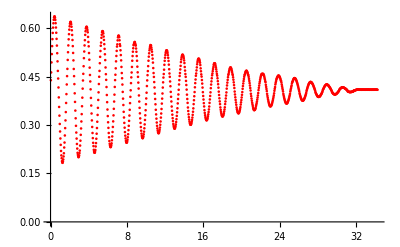

```mathematica
Experiment=ListPlot[Data2,PlotStyle->Red]
```

```mathematica
cart465data[[12]]
```

{0.3663,0.633315,0.156793,-3.1455}

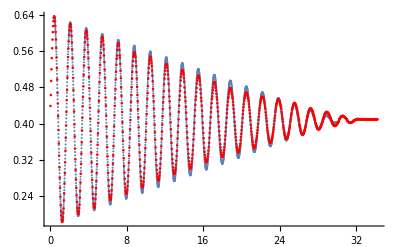

```mathematica
(* define constants and initial conditions *)
g = 9.8;
m = 0.465;
x= 0.633;
xeq=0.4064;
w=3.749;
keff=w^2 m;
vx=0.157;
ti = 0.3663;
tf = 30;
dt = .01;
c1=0.1;
c2=0.1;
c3=0.021;


(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-xeq);
(*Ff=-Sign[vx]*Abs[vx]*c1;*)
(*Ff2=-Sign[vx]*(Abs[vx])^2*c2;*)
Ff3=-Sign[vx]*c3;
ax=(Fs+Ff3)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];


(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment},PlotRange->All]
```

Take average of spring constants and equilibrium points

## Model of Cart with Mass of 715 g

```mathematica
Data2=Table[{cart715data[[n,1]],cart715data[[n,2]]},{n,1,844}];
```

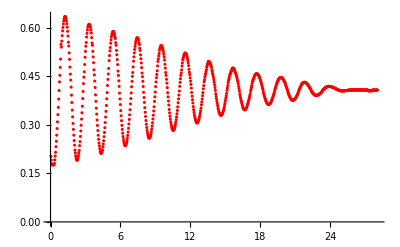

```mathematica
Experiment=ListPlot[Data2,PlotStyle->Red]
```

```mathematica
Data1[[8]]
```

{0.2331,0.217599,-0.447949,1.54965}

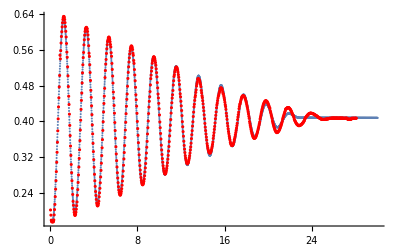

```mathematica
(* define constants and initial conditions *)
g = 9.8;
m = 0.715;
x= 0.176;
xeq=0.4077;
w=3.045;
keff=w^2 m;
vx=-0.009;
ti = 0.1998;
tf = 30;
dt = .01;
c1=0;
c2=0;
c3=0.035;


(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-xeq);
(*Ff=-Sign[vx]*Abs[vx]*c1;*)
(*Ff2=-Sign[vx]*(Abs[vx])^2*c2;*)
Ff3=-Sign[vx]*c3;
ax=(Fs+Ff3)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];


(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment},PlotRange->All]
```

## Model of Cart with mass 964 g

```mathematica
Data2=Table[{cart964data[[n,1]],cart964data[[n,2]]},{n,1,750}];
```

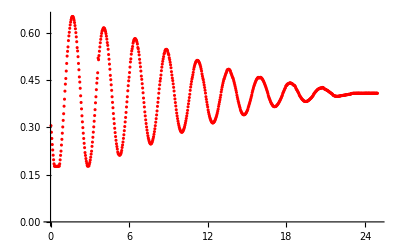

```mathematica
Experiment=ListPlot[Data2,PlotStyle->Red]
```

```mathematica
Data1[[17]]
```

{0.5328,0.177262,-0.000228896,-0.109025}

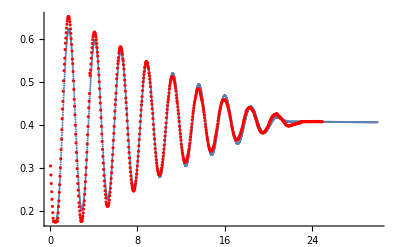

```mathematica
(* define constants and initial conditions *)
g = 9.8;
m = 0.964;
x= 0.177;
xeq=0.4060;
w=2.640;
keff=w^2 m;
vx=0.;
ti = 0.5328;
tf = 30;
dt = .01;
c1=0;
c2=0;
c3=0.043;


(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-xeq);
(*Ff=-Sign[vx]*Abs[vx]*c1;*)
(*Ff2=-Sign[vx]*(Abs[vx])^2*c2;*)
Ff3=-Sign[vx]*c3;
ax=(Fs+Ff3)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];


(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment},PlotRange->All]
;
```

## Model of Cart with mass 1.213 kg

```mathematica
Data2=Table[{cart1213data[[n,1]],cart1213data[[n,2]]},{n,1,679}];
```

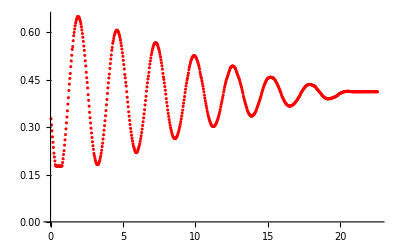

```mathematica
Experiment=ListPlot[Data2,PlotStyle->Red]
```

```mathematica
Data1[[10]]
```

{0.2997,0.192903,-0.334645,2.47856}

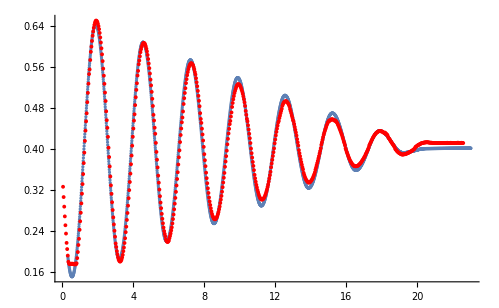

```mathematica
(* define constants and initial conditions *)
g = 9.8;
m = 1.213;
x= 0.192;
xeq=0.4058;
w=2.355;
keff=w^2 m;
vx=-0.335;
ti = 0.2997;
tf = 23;
dt = .01;
c1=0;
c2=0;
c3=0.0580;


(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-xeq);
(*Ff=-Sign[vx]*Abs[vx]*c1;*)
(*Ff2=-Sign[vx]*(Abs[vx])^2*c2;*)
Ff3=-Sign[vx]*c3;
ax=(Fs+Ff3)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];


(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment},PlotRange->All]
```

```mathematica
1
```

## Model of cart with mass of 1.463 kg

```mathematica
Data2=Table[{cart1463data[[n,1]],cart1463data[[n,2]]},{n,1,969}];
```

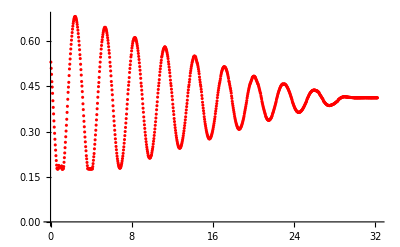

```mathematica
Experiment=ListPlot[Data2,PlotStyle->Red]
```

```mathematica
cart1463data[[37]]
```

{1.1988,0.175616,0.0128182,1.65084}

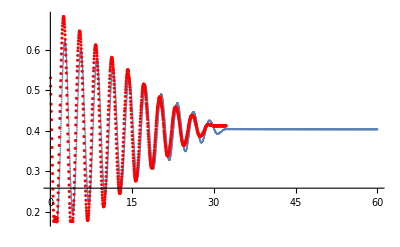

```mathematica
(* define constants and initial conditions *)
g = 9.8;
m = 1.463;
x= 0.176;
xeq=0.4036;
w=2.131;
keff=w^2 m;
vx=0.013;
ti = 1.1988;
tf = 60;
dt = .01;
c1=0;
c2=0;
c3=0.036;


(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-xeq);
(*Ff=-Sign[vx]*Abs[vx]*c1;*)
(*Ff2=-Sign[vx]*(Abs[vx])^2*c2;*)
Ff3=-Sign[vx]*c3;
ax=(Fs+Ff3)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];


(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment},PlotRange->All]
```